# H2 VQE on Superconducting Qubits

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];*)
```

Load the QuESTLink

```mathematica
(*Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];*)
```

Virtual quantum devices, loaded after questlink

```mathematica
(*Import["../../vqd.wl"]*)
```

frequency unit: MHz
time unit: μs

```mathematica
Options[SuperconductingHub]={
(* The number of qubits should match all assignments. Qubits are numbered from 0 to N-1 *)
qubitsNum->6,
(* The T1 time *)
T1-><|0->63,1->93,2->109,3->115,4->68,5->125|>,
(* The T2 time with Hahn echo applied *)
T2-><|0->113,1->149,2->185,3->161,4->122,5->200|>,
(* Excited population probability in the initialisation, also the thermal state *)
ExcitedInit-><|0->0.032,1->0.021,2->0.008,3->0.009,4->0.025,5->0.007|>,
(* Each qubit frequency in MHz   *)
QubitFreq-><|0->4500,1->4900,2->4700,3->5100,4->4900,5->5300|>,
(* Exchange coupling strength of the resonators. Use [Esc]o-o[Esc] for notation *)
ExchangeCoupling-><|0<->1->4,0<->2->1.5,1<->3->1.5,2<->3->4,2<->4->1.5,3<->5->1.5,4<->5->4|>,
(* Transmon Anharmonicity in MHz *)
Anharmonicity-><|0->296.7,1->298.6,2->297.4,3->298.3,4->297.2,5->299.1|>,
(* Fidelity of qubit readout *)
FidRead-><|0->0.9,1->0.92,2->0.96,3->0.97,4->0.93,5->0.97|>,
(* Measurement duration in μs. It is done without quantum amplifiers *)
DurMeas->5,
(* Duration of the Rx and Ry gates are the same regardless the angle. Rz is virtual and perfect. *)
DurRxRy->0.05,
(* Duration of the cross resonance ZX gate that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZX->0.5,
(* Duration of the sizzle gate is fixed regardless the angle that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZZ->0.5,
(* switches to turn/off some noise*)
StdPassiveNoise->True,
ZZPassiveNoise->True
};
```

## The exact solution

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit;daniel's format";
FormatHamiltonian[filename_]:=Module[{stringham,ham,nterms,nqubits},
stringham=Import[filename];
ham=ToExpression[stringham];
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
ham=Table[If[Length[term]<2,{term[[1]],Subscript[Id, nqubits-1]},term],{term,ham}];
nterms=Length@ham;
{Total@Apply[Times,ham,1],nterms,nqubits}
]
```

```mathematica
(* molecule distances *)
moldists=DeleteDuplicates@Flatten@{Range[0.35,1.,0.06],Range[1.,2.5,0.2],Range[2.5,5,0.25]}
```

{0.35,0.41,0.47,0.53,0.59,0.65,0.71,0.77,0.83,0.89,0.95,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.}

```mathematica
(* ground states of H2 *)
gsH2=Table[
	fname=ToString@StringForm["H2_hamiltonians/H2_``.txt", NumberForm[dist, {4, 2}]];
       {ham, nterms, nq} = FormatHamiltonian[fname];
 <|     "distance"->dist,
"hamfile"->fname,
"hamiltonian"->ham,
"groundstate"->Min@Eigenvalues@CalcPauliStringMatrix@ham
|>
,{dist,moldists}];
```

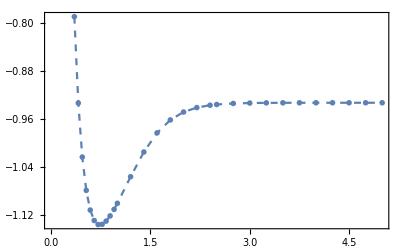

```mathematica
ListPlot[gsH2[[All,{"distance","groundstate"}]],PlotMarkers->{"OpenMarkers",6},PlotStyle->Dashed,Joined->True,Frame->True]
```

## VQE result

```mathematica
vqeH20<<"run1/vqeH20.mx";(* noiseless *)
vqeH21<<"run1/vqeH21.mx"; (* static noise *)
vqeH22<<"run1/vqeH22.mx"; (* realistic *)
```

```mathematica
data=Join[{Values@gsH2[[All,{"distance","groundstate"}]]},
Values@#[[All,{"distance","cost"}]]&/@{vqeH20,vqeH21,vqeH22}];
```

```mathematica
legends=SwatchLegend[{Gray,Red,Purple,Green},{"Exact","Noiseless","Realistic","Only static noise"}];
```

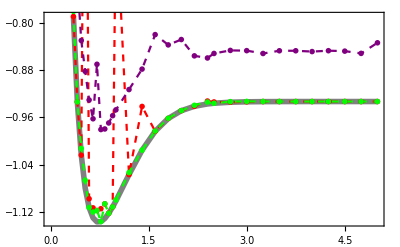

```mathematica
Show[
ListPlot[gsH2[[All,{"distance","groundstate"}]],Joined->True,PlotStyle->Directive[Gray,Thickness->0.01]],
ListPlot[Values@#[[All,{"distance","cost"}]]&/@{vqeH20,vqeH21,vqeH22},PlotMarkers->{"OpenMarkers",3},PlotStyle->{Directive[Red,Dashed],Directive[Purple,Dashed],Directive[Green,Dashed]},Joined->True],
Frame->True,FrameStyle->Directive[Black,Thick]
,Epilog->Inset[Legended[legends,Placed["",{1,0.5}]],Scaled[{0.8,0.25}]]
]
```

## VQE runs

### Noiseless setting: vqeH20

Table[
  {distance, hamfile, hamiltonian, groundstate} = Values@data;
  dev = SuperconductingHub[StdPassiveNoise -> False, ZZPassiveNoise -> False];
  conf = DefaultConfig[dev, hamiltonian];
  conf["virtualmeas"] = {};
  conf["initcirc"] = {};
  conf["groundstate"] = groundstate;
     res = VQEonVQD[conf];
  {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
  AppendTo[vqeH20, <|"distance" -> distance, "hamiltonian" -> hamiltonian, "runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
  DumpSave["vqeH20.mx", vqeH20];
  Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
 Print@ListPlot[Elist, ImageSize -> 300, PlotMarkers -> {"OpenMarkers"}, Joined -> True, PlotRange -> All, Frame -> True, FrameLabel -> {"iteration", "<E>"}];
  Print[DrawCircuit[ansatz, 6], ansatz /. θvars];
  , {data, gsH2}]

Compilation with automatically generated ansatz at Thu 23 Feb 2023 19:54:51 with grad NGAN

@cycle1:Thu 23 Feb 2023 19:57:15, fev:904, <E>: -0.7892692119051312 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 6, 26}[improved well, updated]

@cycle2:Thu 23 Feb 2023 19:59:27, fev:1371, <E>: -0.7892692119051312 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 6, 42}[worse, aborted]Slowing down

@cycle3:Thu 23 Feb 2023 20:02:48, fev:2046, <E>: -0.7892692119051312 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 6, 60}[worse, aborted]Slowing down

dist 0.35 ; runtime 8.33506 min ; ϵ=1.80499×10^-7

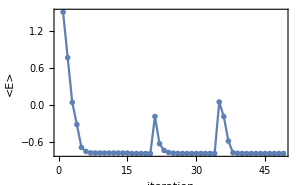

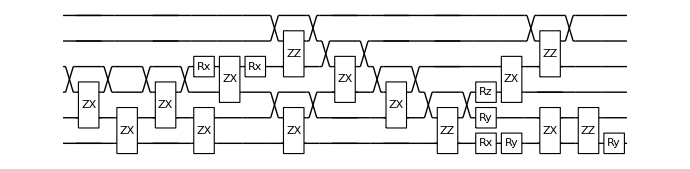
-Graphics-{ZX_(3,1),ZX_(1,0),ZX_(3,1),Rx_3[3.03379],ZX_(1,0),ZX_(3,2),Rx_3[3.14159],ZX_(2,0),ZZ_(3,5),ZX_(4,2),ZX_(3,1),ZZ_(0,2),Ry_1[3.14159],Rz_2[1.5708],Rx_0[-1.56975],ZX_(3,2),Ry_0[1.5708],ZZ_(3,5),ZX_(1,0),ZZ_(0,1),Ry_0[1.5708]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 20:03:12 with grad NGAN

@cycle1:Thu 23 Feb 2023 20:05:02, fev:728, <E>: -0.9237394660537377 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 7, 35}[improved well, updated]

@cycle2:Thu 23 Feb 2023 20:06:46, fev:1180, <E>: -0.9237394660537377 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 7, 54}[worse, aborted]Slowing down

@cycle3:Thu 23 Feb 2023 20:09:56, fev:2272, <E>: -0.9337388795677313 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 19, 92}[improved well, updated]

dist 0.41 ; runtime 10.4992 min ; ϵ=3.67017×10^-8

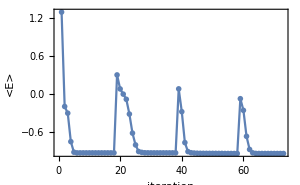

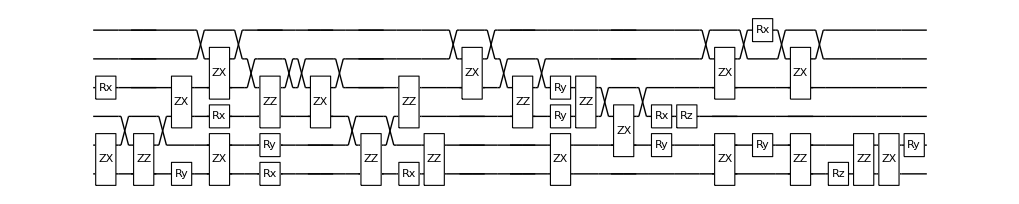
-Graphics-{Rx_3[1.49658],ZX_(1,0),ZZ_(0,2),ZX_(3,2),Ry_0[-1.5708],ZX_(5,3),Rx_2[0.0000266228],ZX_(1,0),ZZ_(2,4),Rx_0[-1.5708],Ry_1[-5.76743×10^-7],ZX_(4,2),ZZ_(0,2),Rx_0[-0.395792],ZZ_(2,3),ZZ_(0,1),ZX_(5,3),ZZ_(2,4),Ry_3[0.0955626],ZX_(1,0),Ry_2[-2.48322],ZZ_(2,3),ZX_(3,1),Rx_2[-0.908869],Ry_1[-2.36848],Rz_2[2.34501],ZX_(5,3),ZX_(1,0),Rx_5[3.14159],Ry_1[1.5708],ZX_(5,3),ZZ_(0,1),Rz_0[-1.5708],ZZ_(0,1),ZX_(1,0),Ry_1[-1.96659]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 20:13:42 with grad NGAN

@cycle1:Thu 23 Feb 2023 20:15:45, fev:819, <E>: -1.0238736102215125 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 3, 40}[improved well, updated]

dist 0.47 ; runtime 2.20652 min ; ϵ=3.00647×10^-8

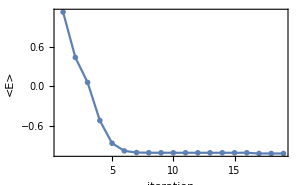

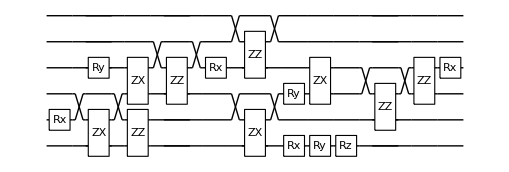
-Graphics-{Rx_1[3.00564],ZX_(2,0),Ry_3[-1.57081],ZZ_(0,1),ZX_(3,2),ZZ_(2,4),Rx_3[3.14159],ZX_(2,0),ZZ_(3,5),Ry_2[3.14159],Rx_0[-0.514376],Ry_0[-1.5708],ZX_(3,2),Rz_0[-1.05731],ZZ_(1,3),ZZ_(2,3),Rx_3[1.57078]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 20:15:54 with grad NGAN

dist 0.53 ; runtime 2.15545 min ; ϵ=9.84648×10^-8

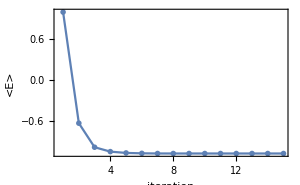

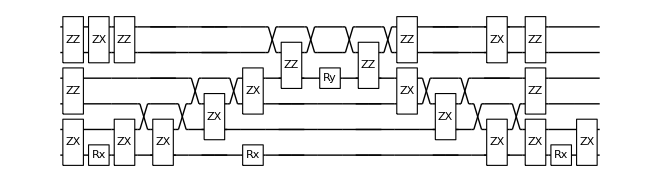
-Graphics-{ZZ_(2,3),ZZ_(4,5),ZX_(1,0),ZX_(5,4),Rx_0[-0.659739],ZX_(1,0),ZZ_(4,5),ZX_(2,0),ZX_(3,1),ZX_(3,2),Rx_0[-1.38148],ZZ_(3,5),Ry_3[1.56835],ZZ_(3,5),ZX_(3,2),ZZ_(4,5),ZX_(3,1),ZX_(2,0),ZX_(5,4),ZX_(1,0),ZZ_(2,3),ZZ_(4,5),Rx_0[2.04122],ZX_(1,0)}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 20:18:04 with grad NGAN

@cycle1:Thu 23 Feb 2023 20:20:02, fev:749, <E>: 0.5407655100476585 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 0, 37}[improved well, updated]

@cycle2:Thu 23 Feb 2023 20:21:56, fev:1481, <E>: -1.097631712996515 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 30, 0, 15, 49}[improved well, updated]

@cycle3:Thu 23 Feb 2023 20:23:02, fev:1912, <E>: -1.097631712996515 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 30, 0, 15, 61}[worse, aborted]Slowing down

@cycle4:Thu 23 Feb 2023 20:24:33, fev:2454, <E>: -1.097631712996515 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 30, 0, 15, 76}[worse, aborted]Slowing down

dist 0.59 ; runtime 6.50778 min ; ϵ=0.0148286

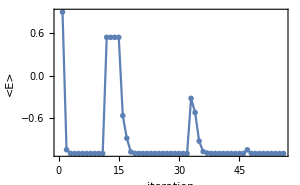

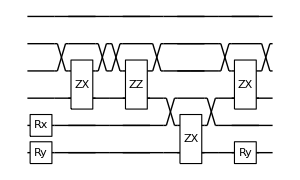
-Graphics-{Ry_0[1.5708],Rx_1[3.14159],ZX_(4,2),ZZ_(2,4),ZX_(2,0),ZX_(4,2),Ry_0[1.5708]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 20:24:34 with grad NGAN

@cycle1:Thu 23 Feb 2023 20:26:27, fev:692, <E>: -0.2257335493154132 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 6, 37}[improved well, updated]

@cycle2:Thu 23 Feb 2023 20:28:33, fev:1420, <E>: -0.49538980238721153 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 24, 0, 19, 53}[improved well, updated]

@cycle3:Thu 23 Feb 2023 20:30:09, fev:2076, <E>: -1.112996545669168 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 42, 0, 34, 70}[improved well, updated]

@cycle4:Thu 23 Feb 2023 20:30:59, fev:2446, <E>: -1.112996545669168 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 42, 0, 34, 89}[worse, aborted]Slowing down

@cycle5:Thu 23 Feb 2023 20:32:14, fev:2934, <E>: -1.112996545669168 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 42, 0, 34, 103}[worse, aborted]Slowing down

dist 0.65 ; runtime 7.6601 min ; ϵ=0.0169082

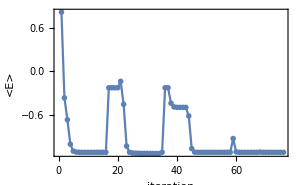

-Graphics-{Ry_1[-3.14159],Ry_0[-3.14159]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 20:32:14 with grad NGAN

@cycle1:Thu 23 Feb 2023 20:34:06, fev:643, <E>: -0.5263312223833952 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 8, 0, 6, 29}[improved well, updated]

@cycle2:Thu 23 Feb 2023 20:36:08, fev:1317, <E>: 0.2900239641537037 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 25, 0, 23, 40}[improved well, updated]

@cycle3:Thu 23 Feb 2023 20:38:10, fev:2012, <E>: -1.11750076958274 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 34, 0, 45, 58}[improved well, updated]

@cycle4:Thu 23 Feb 2023 20:38:59, fev:2373, <E>: -1.11750076958274 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 34, 0, 45, 73}[worse, aborted]Slowing down

@cycle5:Thu 23 Feb 2023 20:40:23, fev:2933, <E>: -1.11750076958274 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 34, 0, 45, 85}[worse, aborted]Slowing down

dist 0.71 ; runtime 8.1599 min ; ϵ=0.0192496

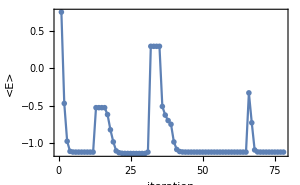

-Graphics-{Ry_0[-3.14139],Rx_1[3.14158]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 20:40:24 with grad NGAN

@cycle1:Thu 23 Feb 2023 20:42:23, fev:812, <E>: -0.38272044536821576 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 0, 47}[improved well, updated]

@cycle2:Thu 23 Feb 2023 20:44:34, fev:1515, <E>: -1.114456210573931 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 39, 0, 12, 58}[improved well, updated]

@cycle3:Thu 23 Feb 2023 20:45:45, fev:2158, <E>: -1.1144564576889415 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 48, 0, 16, 67}[improved well, updated]

@cycle4:Thu 23 Feb 2023 20:46:50, fev:2558, <E>: -1.1144564576889415 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 48, 0, 16, 76}[worse, aborted]Slowing down

@cycle5:Thu 23 Feb 2023 20:48:27, fev:3124, <E>: -1.1144564576889415 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 48, 0, 16, 88}[improved pathetically, aborted]Slowing down

@cycle6:Thu 23 Feb 2023 20:50:37, fev:3803, <E>: -1.1144564576889415 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 48, 0, 16, 111}[worse, aborted]Slowing down

dist 0.77 ; runtime 10.2556 min ; ϵ=0.0218727

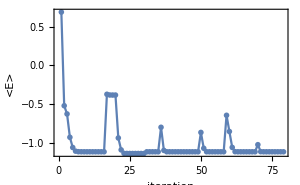

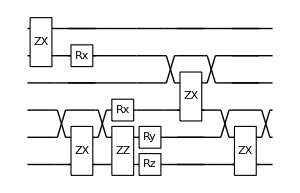
-Graphics-{ZX_(5,4),ZX_(2,0),Rx_4[1.57079],ZZ_(0,1),Rx_2[1.57079],Ry_1[-3.14159],Rz_0[-1.57057],ZX_(4,2),ZX_(2,0)}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 20:50:39 with grad NGAN

@cycle1:Thu 23 Feb 2023 20:52:38, fev:804, <E>: -0.5631217564131435 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 0, 27}[improved well, updated]

@cycle2:Thu 23 Feb 2023 20:55:07, fev:1701, <E>: -1.1061557335586343 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 27, 44}[improved well, updated]

@cycle3:Thu 23 Feb 2023 20:56:04, fev:2090, <E>: -1.1061557335586343 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 27, 56}[worse, aborted]Slowing down

@cycle4:Thu 23 Feb 2023 20:57:27, fev:2587, <E>: -1.1061557335586343 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 37, 0, 27, 80}[worse, aborted]Slowing down

dist 0.83 ; runtime 6.82231 min ; ϵ=0.0248019

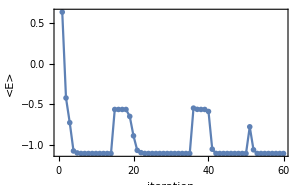

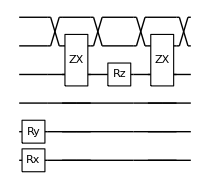
-Graphics-{Ry_1[-3.14159],Rx_0[3.14159],ZX_(5,3),Rz_3[-3.1408],ZX_(5,3)}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 20:57:28 with grad NGAN

@cycle1:Thu 23 Feb 2023 20:59:26, fev:796, <E>: -1.094183783545596 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 15, 42}[improved well, updated]

@cycle2:Thu 23 Feb 2023 21:01:06, fev:1256, <E>: -1.094183783545596 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 15, 58}[worse, aborted]Slowing down

@cycle3:Thu 23 Feb 2023 21:04:05, fev:2259, <E>: -1.122250725597693 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 42, 0, 28, 85}[improved well, updated]

dist 0.89 ; runtime 6.69716 min ; ϵ=8.64531×10^-8

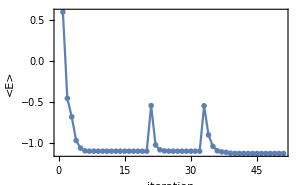

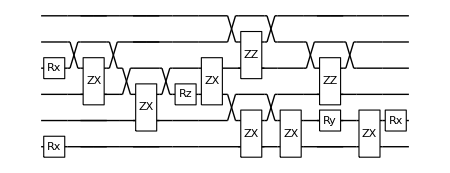
-Graphics-{Rx_0[1.57014],Rx_3[0.293091],ZX_(4,2),ZX_(3,1),Rz_2[3.14159],ZX_(3,2),ZX_(2,0),ZZ_(3,5),ZX_(1,0),ZZ_(2,4),Ry_1[3.14159],ZX_(1,0),Rx_1[1.5708]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 21:04:10 with grad NGAN

@cycle1:Thu 23 Feb 2023 21:06:12, fev:788, <E>: -1.0796369010946272 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 14, 23}[improved well, updated]

dist 0.95 ; runtime 3.94108 min ; ϵ=2.39076×10^-10

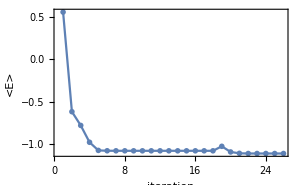

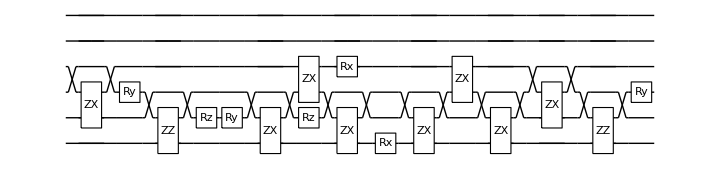
-Graphics-{ZX_(3,1),Ry_2[1.57079],ZZ_(0,2),Rz_1[-0.822583],Ry_1[3.14159],ZX_(2,0),Rz_1[-0.822583],ZX_(3,2),ZX_(2,0),Rx_3[0.324513],Rx_0[-3.14159],ZX_(2,0),ZX_(3,2),ZX_(2,0),ZX_(3,1),ZZ_(0,2),Ry_2[-1.57079]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 21:08:07 with grad NGAN

@cycle1:Thu 23 Feb 2023 21:10:00, fev:754, <E>: -1.0661086426264126 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 11, 39}[improved well, updated]

@cycle2:Thu 23 Feb 2023 21:11:42, fev:1209, <E>: -1.0661086426264126 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 11, 62}[improved pathetically, aborted]Slowing down

@cycle3:Thu 23 Feb 2023 21:15:24, fev:2559, <E>: -0.7458717868313818 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 20, 87}[improved well, updated]

dist 1. ; runtime 10.5348 min ; ϵ=7.10131×10^-9

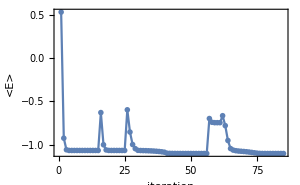

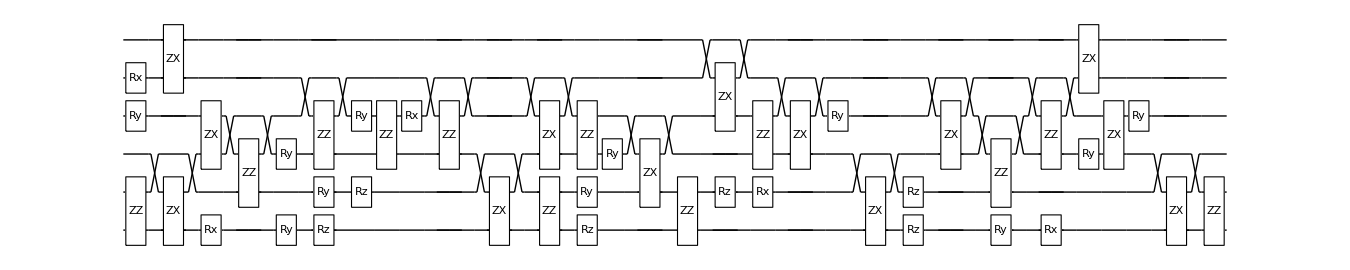
-Graphics-{ZZ_(0,1),Rx_4[1.5708],Ry_3[-1.57094],ZX_(2,0),ZX_(5,4),ZX_(3,2),Rx_0[-1.45828],ZZ_(1,3),Ry_2[0.000059953],Ry_0[-1.57079],ZZ_(2,4),Rz_0[-0.112569],Ry_1[1.57074],Ry_3[-3.14152],Rz_1[-1.57029],ZZ_(2,3),Rx_3[1.21562],ZZ_(2,4),ZX_(2,0),ZX_(4,2),ZZ_(0,1),ZZ_(2,3),Ry_1[-3.14159],Rz_0[1.57076],Ry_2[1.5708],ZX_(3,1),ZZ_(0,1),ZX_(5,3),Rz_1[-3.14159],ZZ_(2,3),Rx_1[-1.5708],ZX_(4,2),Ry_3[-1.5708],ZX_(2,0),Rz_1[0.113092],Rz_0[2.11508],ZX_(4,2),ZZ_(1,3),Ry_0[-0.0000203566],ZZ_(2,4),Rx_0[-1.57085],Ry_2[-0.00006017],ZX_(5,4),ZX_(3,2),Ry_3[-1.5708],ZX_(2,0),ZZ_(0,1)}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 21:18:39 with grad NGAN

@cycle1:Thu 23 Feb 2023 21:20:43, fev:849, <E>: -1.0051067054464813 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 11, 36}[improved well, updated]

@cycle2:Thu 23 Feb 2023 21:22:04, fev:1261, <E>: -1.0051067054464813 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 11, 86}[worse, aborted]Slowing down

dist 1.2 ; runtime 6.59957 min ; ϵ=1.76655×10^-10

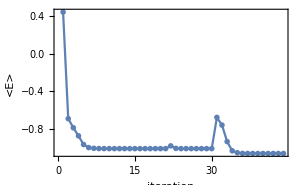

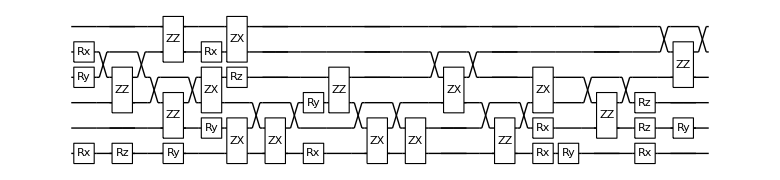
-Graphics-{Rx_4[-1.0893],Rx_0[-2.5593],Ry_3[0.482621],ZZ_(2,4),Rz_0[0.854557],ZZ_(1,3),ZZ_(4,5),Ry_0[-0.460971],ZX_(3,2),Ry_1[-0.258451],Rx_4[0.481497],Rz_3[0.270891],ZX_(1,0),ZX_(5,4),ZX_(2,0),Ry_2[1.5708],Rx_0[-0.369411],ZZ_(2,3),ZX_(2,0),ZX_(1,0),ZX_(4,2),ZZ_(0,2),Rx_1[-1.5708],ZX_(3,2),Rx_0[0.0629616],Ry_0[1.5708],ZZ_(1,3),Rz_2[1.36287],Rx_0[-3.14159],Rz_1[0.258451],ZZ_(3,5),Ry_1[-1.5708]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 21:25:15 with grad NGAN

@cycle1:Thu 23 Feb 2023 21:26:58, fev:567, <E>: -0.6091781036077067 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 0, 26}[improved well, updated]

@cycle2:Thu 23 Feb 2023 21:28:58, fev:1248, <E>: -0.941480654707796 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 34, 0, 13, 42}[improved well, updated]

@cycle3:Thu 23 Feb 2023 21:30:10, fev:1667, <E>: -0.941480654707796 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 34, 0, 13, 47}[worse, aborted]Slowing down

@cycle4:Thu 23 Feb 2023 21:31:52, fev:2215, <E>: -0.941480654707796 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 34, 0, 13, 60}[worse, aborted]Slowing down

dist 1.4 ; runtime 6.60603 min ; ϵ=0.0739876

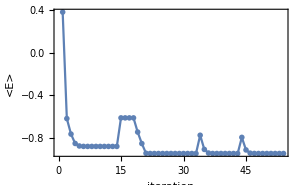

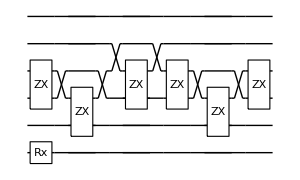
-Graphics-{Rx_0[-3.14159],ZX_(3,2),ZX_(3,1),ZX_(4,2),ZX_(3,2),ZX_(3,1),ZX_(3,2)}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 21:31:52 with grad NGAN

@cycle1:Thu 23 Feb 2023 21:34:06, fev:817, <E>: -0.9834727222296447 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 8, 28}[improved well, updated]

dist 1.6 ; runtime 2.42144 min ; ϵ=6.80353×10^-9

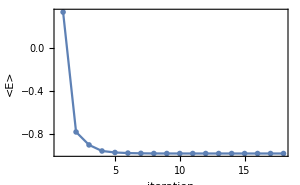

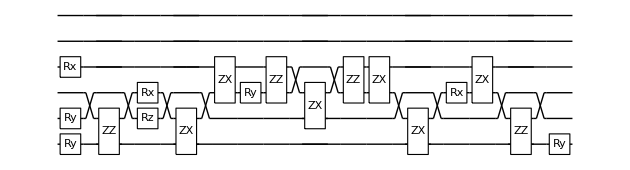
-Graphics-{Ry_0[-1.5708],Ry_1[-1.5708],Rx_3[-0.814458],ZZ_(0,2),Rz_1[1.5708],Rx_2[3.14151],ZX_(2,0),ZX_(3,2),Ry_2[-3.14139],ZZ_(2,3),ZX_(3,1),ZZ_(2,3),ZX_(3,2),ZX_(2,0),Rx_2[1.57093],ZX_(3,2),ZZ_(0,2),Ry_0[-1.5708]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 21:34:17 with grad NGAN

@cycle1:Thu 23 Feb 2023 21:36:33, fev:879, <E>: -0.9391959235863222 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 3, 29}[improved well, updated]

@cycle2:Thu 23 Feb 2023 21:38:47, fev:1381, <E>: -0.9391959235863222 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 3, 50}[worse, aborted]Slowing down

@cycle3:Thu 23 Feb 2023 21:43:16, fev:2711, <E>: -0.9414451303351471 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 33, 0, 25, 66}[improved well, updated]

@cycle4:Thu 23 Feb 2023 21:46:53, fev:3807, <E>: -0.9618168575056742 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 56, 0, 43, 92}[improved well, updated]

dist 1.8 ; runtime 12.673 min ; ϵ=9.52869×10^-8

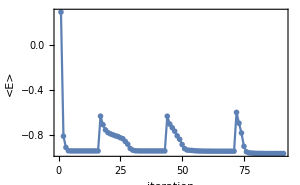

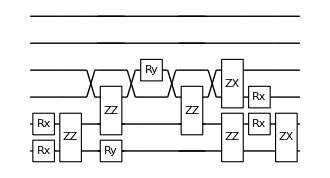
-Graphics-{Rx_0[-1.5708],Rx_1[-1.57119],ZZ_(0,1),ZZ_(1,3),Ry_0[-3.14159],Ry_3[0.984261],ZZ_(1,3),ZZ_(0,1),ZX_(3,2),Rx_1[1.57119],Rx_2[-1.5708],ZX_(1,0)}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 21:46:58 with grad NGAN

@cycle1:Thu 23 Feb 2023 21:48:49, fev:670, <E>: -0.9245373152651064 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 2, 32}[improved well, updated]

@cycle2:Thu 23 Feb 2023 21:50:54, fev:1474, <E>: -0.93721282846063 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 33, 0, 15, 56}[improved well, updated]

@cycle3:Thu 23 Feb 2023 21:52:45, fev:2258, <E>: -0.9486411056501268 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 48, 0, 23, 74}[improved well, updated]

dist 2. ; runtime 5.89843 min ; ϵ=6.52606×10^-9

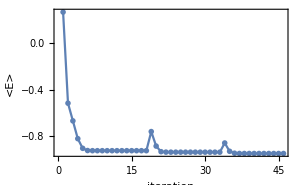

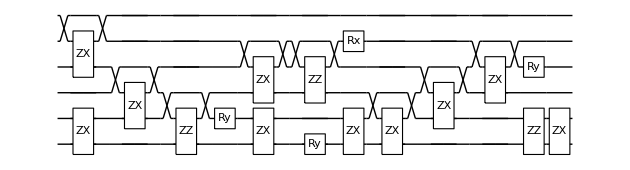
-Graphics-{ZX_(5,3),ZX_(1,0),ZX_(3,1),ZZ_(0,2),Ry_1[-1.57088],ZX_(4,2),ZX_(1,0),ZZ_(2,4),Ry_0[-2.00825],Rx_4[3.14159],ZX_(1,0),ZX_(2,0),ZX_(3,1),ZX_(4,2),Ry_3[1.5708],ZZ_(0,1),ZX_(1,0)}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 21:52:52 with grad NGAN

@cycle1:Thu 23 Feb 2023 21:54:55, fev:767, <E>: -0.9412240260691803 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 7, 15}[improved well, updated]

dist 2.2 ; runtime 2.12193 min ; ϵ=7.62408×10^-9

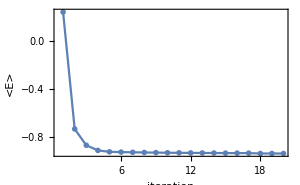

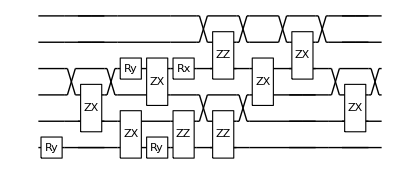
-Graphics-{Ry_0[0.318003],ZX_(3,1),Ry_3[1.57085],ZX_(1,0),ZX_(3,2),Ry_0[1.57085],Rx_3[-1.57079],ZZ_(0,1),ZZ_(3,5),ZZ_(0,2),ZX_(3,2),ZX_(5,3),ZX_(3,1)}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 21:54:59 with grad NGAN

@cycle1:Thu 23 Feb 2023 21:56:48, fev:606, <E>: -0.49242436231199777 nansatz: 1 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 1, 22}[improved well, updated]

@cycle2:Thu 23 Feb 2023 21:58:22, fev:1265, <E>: -0.9323150070247159 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 8, 64}[improved well, updated]

@cycle3:Thu 23 Feb 2023 21:59:28, fev:1665, <E>: -0.9323150070247159 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 8, 82}[worse, aborted]Slowing down

@cycle4:Thu 23 Feb 2023 22:00:59, fev:2154, <E>: -0.9323150070247159 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 8, 91}[improved pathetically, aborted]Slowing down

@cycle5:Thu 23 Feb 2023 22:03:05, fev:2770, <E>: -0.9323150070247159 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 8, 106}[improved pathetically, aborted]Slowing down

dist 2.4 ; runtime 8.14199 min ; ϵ=0.00493995

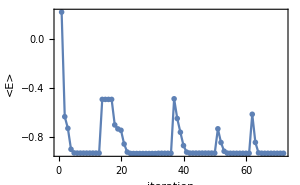

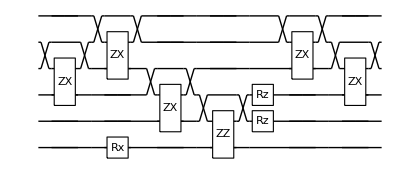
-Graphics-{ZX_(4,2),ZX_(5,3),Rx_0[-1.68604],ZX_(3,1),ZZ_(0,2),Rz_1[-1.57082],Rz_2[-1.5708],ZX_(5,3),ZX_(4,2)}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 22:03:08 with grad NGAN

@cycle1:Thu 23 Feb 2023 22:04:51, fev:555, <E>: -0.455423864746724 nansatz: 1 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 0, 33}[improved well, updated]

@cycle2:Thu 23 Feb 2023 22:06:37, fev:1253, <E>: -0.9316390827125116 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 11, 51}[improved well, updated]

@cycle3:Thu 23 Feb 2023 22:07:51, fev:1669, <E>: -0.9316390827125116 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 19, 0, 11, 59}[improved pathetically, aborted]Slowing down

@cycle4:Thu 23 Feb 2023 22:09:58, fev:2577, <E>: -0.932563156979092 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 18, 72}[improved well, updated]

@cycle5:Thu 23 Feb 2023 22:11:48, fev:3113, <E>: -0.932563156979092 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 18, 83}[worse, aborted]Slowing down

@cycle6:Thu 23 Feb 2023 22:15:13, fev:4273, <E>: -0.933863265922548 nansatz: 27 merged-smallθ-metric-bf-gmerged: {1, 32, 0, 18, 100}[improved well, updated]

@cycle7:Thu 23 Feb 2023 22:19:59, fev:5784, <E>: -0.9316388342954568 nansatz: 31 merged-smallθ-metric-bf-gmerged: {1, 45, 0, 23, 121}[improved well, updated]

@cycle8:Thu 23 Feb 2023 22:24:34, fev:7065, <E>: -0.6529890939332277 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 58, 0, 37, 130}[improved well, updated]

@cycle9:Thu 23 Feb 2023 22:28:43, fev:8109, <E>: -0.9316390816560871 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 80, 0, 64, 158}[improved well, updated]

@cycle10:Thu 23 Feb 2023 22:31:09, fev:8742, <E>: -0.9316390816560871 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 80, 0, 64, 166}[worse, aborted]Slowing down

@cycle11:Thu 23 Feb 2023 22:35:32, fev:10081, <E>: -0.9338469985076125 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 92, 0, 74, 175}[improved well, updated]

@cycle12:Thu 23 Feb 2023 22:39:39, fev:10937, <E>: -0.9338469985076125 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 92, 0, 74, 202}[worse, aborted]Slowing down

@cycle13:Thu 23 Feb 2023 22:44:59, fev:11982, <E>: -0.9338469985076125 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 92, 0, 74, 222}[worse, aborted]Slowing down

dist 2.5 ; runtime 42.0799 min ; ϵ=0.00220792

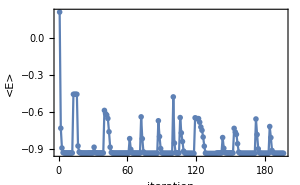

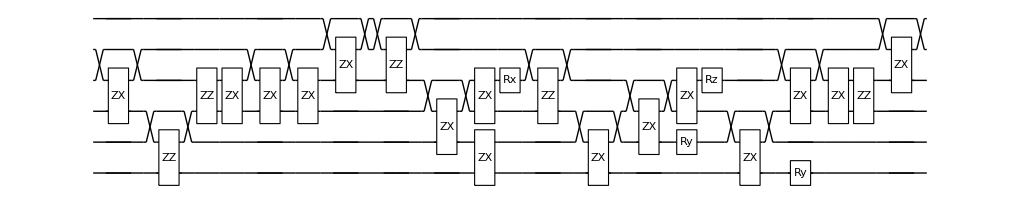
-Graphics-{ZX_(4,2),ZZ_(0,2),ZZ_(2,3),ZX_(3,2),ZX_(4,2),ZX_(3,2),ZX_(5,3),ZZ_(3,5),ZX_(3,1),ZX_(1,0),ZX_(3,2),Rx_3[-2.95135],ZZ_(2,4),ZX_(2,0),ZX_(3,1),ZX_(3,2),Ry_1[1.5708],Rz_3[1.5708],ZX_(2,0),ZX_(4,2),Ry_0[3.14159],ZX_(3,2),ZZ_(2,3),ZX_(5,3)}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 22:45:13 with grad NGAN

@cycle1:Thu 23 Feb 2023 22:46:58, fev:621, <E>: -0.9325609548749059 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 7, 31}[improved well, updated]

dist 2.75 ; runtime 4.51787 min ; ϵ=1.11991×10^-8

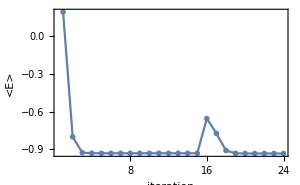

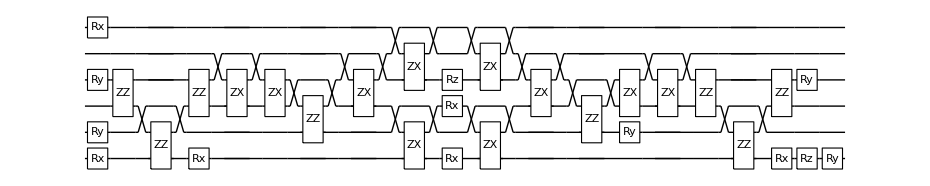
-Graphics-{Ry_3[0.465141],Ry_1[-1.5708],Rx_0[1.02428],Rx_5[3.14159],ZZ_(2,3),ZZ_(0,2),Rx_0[1.51169],ZZ_(2,3),ZX_(4,2),ZX_(3,2),ZZ_(1,3),ZX_(4,2),ZX_(5,3),ZX_(2,0),Rz_3[1.69145],Rx_2[3.1408],Rx_0[-3.08348],ZX_(2,0),ZX_(5,3),ZX_(4,2),ZZ_(1,3),ZX_(3,2),Ry_1[1.5708],ZX_(4,2),ZZ_(2,3),ZZ_(0,2),Rx_0[-1.5707],ZZ_(2,3),Rz_0[3.14154],Ry_3[0.465141],Ry_0[0.546508]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 22:49:44 with grad NGAN

@cycle1:Thu 23 Feb 2023 22:52:06, fev:900, <E>: -0.9336317495988786 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 2, 50}[improved well, updated]

dist 3. ; runtime 2.62837 min ; ϵ=9.49596×10^-8

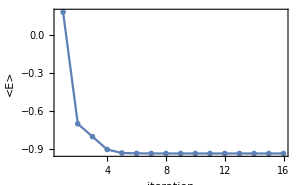

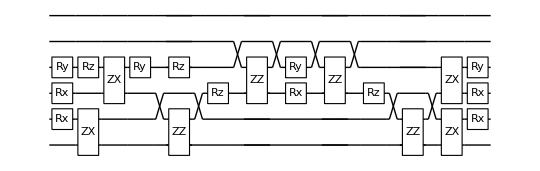
-Graphics-{Rx_2[0.794687],Ry_3[-1.5708],Rx_1[-1.5708],Rz_3[-0.857353],ZX_(1,0),ZX_(3,2),Ry_3[1.06814],ZZ_(0,2),Rz_3[0.559255],Rz_2[0.845041],ZZ_(2,4),Ry_3[-1.62876],Rx_2[-1.64655],ZZ_(2,4),Rz_2[1.5708],ZZ_(0,2),ZX_(3,2),ZX_(1,0),Rx_1[1.5708],Rx_2[-1.5708],Ry_3[-1.5708]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 22:52:21 with grad NGAN

@cycle1:Thu 23 Feb 2023 22:54:28, fev:894, <E>: -0.9332117769580147 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 14, 1, 8, 36}[improved well, updated]

@cycle2:Thu 23 Feb 2023 22:56:10, fev:1346, <E>: -0.9332117769580147 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 14, 1, 8, 58}[worse, aborted]Slowing down

@cycle3:Thu 23 Feb 2023 22:58:33, fev:1918, <E>: -0.9332117769580147 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 14, 1, 8, 94}[improved pathetically, aborted]Slowing down

@cycle4:Thu 23 Feb 2023 23:02:10, fev:2651, <E>: -0.9332117769580147 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 14, 1, 8, 134}[worse, aborted]Slowing down

dist 3.25 ; runtime 9.85662 min ; ϵ=0.000129504

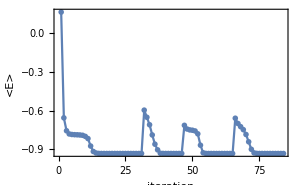

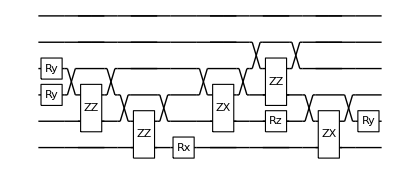
-Graphics-{Ry_2[-1.54817],Ry_3[1.54817],ZZ_(1,3),ZZ_(0,2),Rx_0[1.5708],ZX_(3,1),ZZ_(2,4),Rz_1[1.5708],ZX_(2,0),Ry_1[1.5708]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 23:02:13 with grad NGAN

@cycle1:Thu 23 Feb 2023 23:04:02, fev:679, <E>: -0.9331251959888716 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 8, 39}[improved well, updated]

@cycle2:Thu 23 Feb 2023 23:06:23, fev:1498, <E>: -0.9331820908022916 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 34, 0, 14, 52}[improved well, updated]

@cycle3:Thu 23 Feb 2023 23:08:14, fev:1961, <E>: -0.9331820908022916 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 34, 0, 14, 71}[worse, aborted]Slowing down

@cycle4:Thu 23 Feb 2023 23:10:44, fev:2521, <E>: -0.9331820908022916 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 34, 0, 14, 80}[worse, aborted]Slowing down

dist 3.5 ; runtime 8.70374 min ; ϵ=0.0000463147

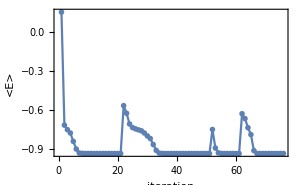

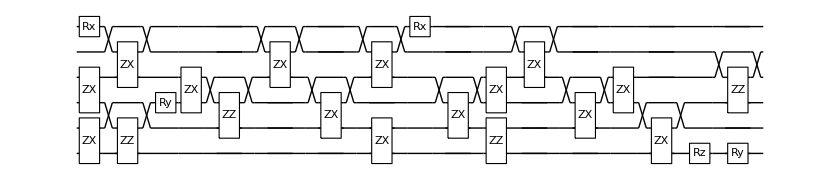
-Graphics-{ZX_(1,0),ZX_(3,2),Rx_5[1.5708],ZZ_(0,2),ZX_(5,3),Ry_2[-1.57001],ZX_(3,2),ZZ_(1,3),ZX_(5,3),ZX_(3,1),ZX_(5,3),ZX_(1,0),Rx_5[-1.59831],ZX_(3,1),ZZ_(0,1),ZX_(3,2),ZX_(5,3),ZX_(3,1),ZX_(3,2),ZX_(2,0),Rz_0[1.5708],ZZ_(2,4),Ry_0[1.5708]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 23:10:55 with grad NGAN

@cycle1:Thu 23 Feb 2023 23:12:46, fev:683, <E>: -0.93315425591313 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 0, 47}[improved well, updated]

dist 3.75 ; runtime 4.20282 min ; ϵ=1.32271×10^-10

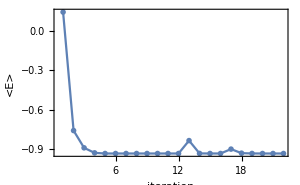

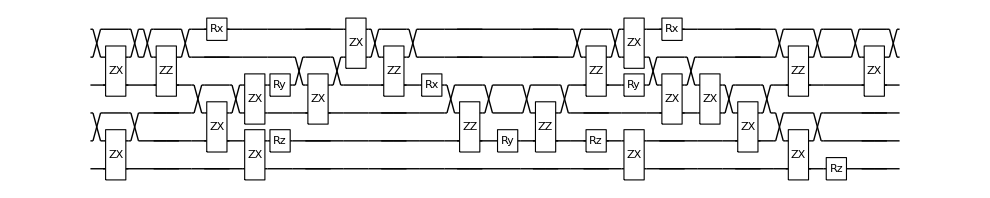
-Graphics-{ZX_(2,0),ZX_(5,3),ZZ_(3,5),ZX_(3,1),Rx_5[1.54014],ZX_(3,2),ZX_(1,0),Ry_3[0.203232],Rz_1[-1.61215],ZX_(4,2),ZX_(5,4),ZZ_(3,5),Rx_3[2.4244],ZZ_(1,3),Ry_1[3.14159],ZZ_(1,3),ZZ_(3,5),Rz_1[1.52945],Ry_3[1.78002],ZX_(1,0),ZX_(5,4),ZX_(4,2),Rx_5[1.54252],ZX_(3,2),ZX_(3,1),ZX_(2,0),ZZ_(3,5),Rz_0[3.14159],ZX_(5,3)}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 23:15:08 with grad NGAN

@cycle1:Thu 23 Feb 2023 23:17:25, fev:905, <E>: -0.6253743014646134 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 5, 30}[improved well, updated]

@cycle2:Thu 23 Feb 2023 23:19:43, fev:1710, <E>: -0.9331608219117489 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 17, 52}[improved well, updated]

@cycle3:Thu 23 Feb 2023 23:20:52, fev:2064, <E>: -0.9331608219117489 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 17, 60}[worse, aborted]Slowing down

@cycle4:Thu 23 Feb 2023 23:22:36, fev:2597, <E>: -0.9331608219117489 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 17, 71}[worse, aborted]Slowing down

dist 4. ; runtime 7.50794 min ; ϵ=0.0000105399

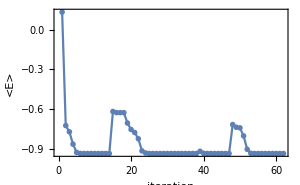

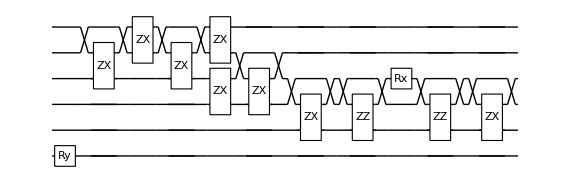
-Graphics-{Ry_0[3.1408],ZX_(5,3),ZX_(5,4),ZX_(5,3),ZX_(5,4),ZX_(3,2),ZX_(4,2),ZX_(3,1),ZZ_(1,3),Rx_3[3.14159],ZZ_(1,3),ZX_(3,1)}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 23:22:38 with grad NGAN

@cycle1:Thu 23 Feb 2023 23:24:36, fev:782, <E>: -0.9331628147704492 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 11, 54}[improved well, updated]

@cycle2:Thu 23 Feb 2023 23:26:15, fev:1236, <E>: -0.9331628147704492 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 11, 76}[improved pathetically, aborted]Slowing down

@cycle3:Thu 23 Feb 2023 23:28:41, fev:1807, <E>: -0.9331628147704492 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 11, 98}[improved pathetically, aborted]Slowing down

dist 4.25 ; runtime 6.07162 min ; ϵ=3.3707×10^-6

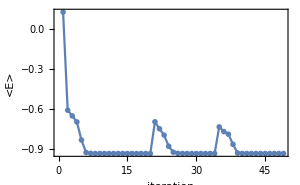

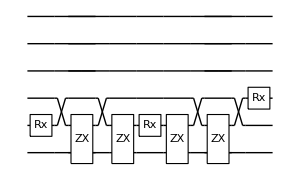
-Graphics-{Rx_1[3.14159],ZX_(2,0),ZX_(1,0),Rx_1[3.14159],ZX_(1,0),ZX_(2,0),Rx_2[3.14102]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 23:28:43 with grad NGAN

@cycle1:Thu 23 Feb 2023 23:30:38, fev:711, <E>: -0.9331634491112216 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 9, 40}[improved well, updated]

@cycle2:Thu 23 Feb 2023 23:32:17, fev:1141, <E>: -0.9331634491112216 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 9, 51}[improved pathetically, aborted]Slowing down

@cycle3:Thu 23 Feb 2023 23:34:43, fev:1724, <E>: -0.9331634491112216 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 9, 77}[worse, aborted]Slowing down

@cycle4:Thu 23 Feb 2023 23:38:16, fev:2443, <E>: -0.9331634491112216 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 9, 111}[worse, aborted]Slowing down

dist 4.5 ; runtime 9.61978 min ; ϵ=1.02098×10^-6

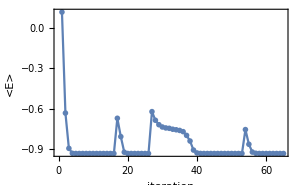

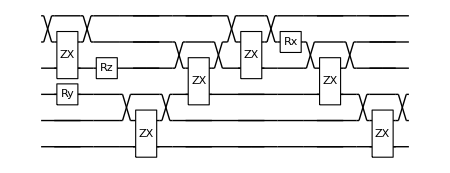
-Graphics-{ZX_(5,3),Ry_2[-3.14139],Rz_3[-3.14085],ZX_(2,0),ZX_(4,2),ZX_(5,3),Rx_4[3.14138],ZX_(4,2),ZX_(2,0)}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 23:38:20 with grad NGAN

@cycle1:Thu 23 Feb 2023 23:40:08, fev:630, <E>: -0.46676974648458625 nansatz: 1 merged-smallθ-metric-bf-gmerged: {0, 18, 0, 3, 24}[improved well, updated]

@cycle2:Thu 23 Feb 2023 23:41:43, fev:1255, <E>: -0.466769766392325 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 21, 43}[improved well, updated]

@cycle3:Thu 23 Feb 2023 23:43:38, fev:1988, <E>: -0.9331636134624604 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 43, 0, 42, 53}[improved well, updated]

@cycle4:Thu 23 Feb 2023 23:44:37, fev:2362, <E>: -0.9331636134624604 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 43, 0, 42, 70}[worse, aborted]Slowing down

@cycle5:Thu 23 Feb 2023 23:46:04, fev:2878, <E>: -0.9331636134624604 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 43, 0, 42, 79}[worse, aborted]Slowing down

dist 4.75 ; runtime 7.75656 min ; ϵ=3.12456×10^-7

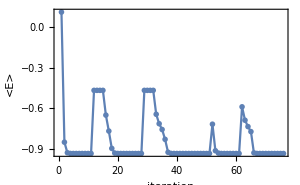

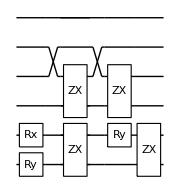
-Graphics-{Rx_1[-3.1411],Ry_0[-3.14159],ZX_(4,2),ZX_(1,0),ZX_(3,2),Ry_1[-3.14159],ZX_(1,0)}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 23:46:05 with grad NGAN

dist 5. ; runtime 1.80681 min ; ϵ=8.011×10^-8

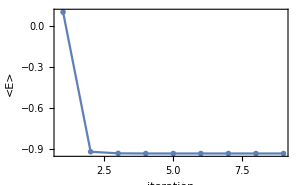

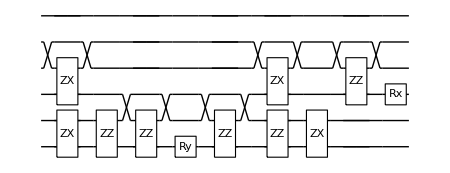
-Graphics-{ZX_(4,2),ZX_(1,0),ZZ_(0,1),ZZ_(0,2),Ry_0[-3.14155],ZZ_(0,2),ZX_(4,2),ZZ_(0,1),ZX_(1,0),ZZ_(2,4),Rx_2[-1.22701×10^-7]}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

### Realistic setting: vqeH21

Table[
  {distance, hamfile, hamiltonian, groundstate} = Values@data;
  dev = SuperconductingHub[];
  conf = DefaultConfig[dev, hamiltonian];
  conf["groundstate"] = groundstate;
     res = VQEonVQD[conf];
  {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
  AppendTo[vqeH21, <|"distance" -> distance, "hamiltonian" -> hamiltonian, "runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
  DumpSave["vqeH21.mx", vqeH21];
  Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
 Print@ListPlot[Elist, ImageSize -> 300, PlotMarkers -> {"OpenMarkers"}, Joined -> True, PlotRange -> All, Frame -> True, FrameLabel -> {"iteration", "<E>"}];
  Print[DrawCircuit[ansatz, 6], ansatz /. θvars];
  , {data, gsH2}]

Compilation with automatically generated ansatz at Thu 23 Feb 2023 23:47:54 with grad NGAN

@cycle1:Thu 23 Feb 2023 23:50:54, fev:620, <E>: -0.5729987480595186 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 3, 43}[improved well, updated]

@cycle2:Thu 23 Feb 2023 23:53:24, fev:1051, <E>: -0.5729987480595186 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 3, 71}[worse, aborted]Slowing down

@cycle3:Thu 23 Feb 2023 23:57:54, fev:1714, <E>: -0.5729987480595186 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 3, 99}[worse, aborted]Slowing down

dist 0.35 ; runtime 10.1196 min ; ϵ=0.216271

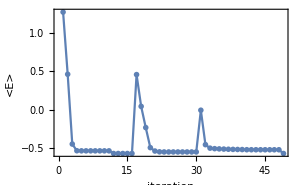

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Ry_0[3.14159],Rx_1[3.14147],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Thu 23 Feb 2023 23:58:01 with grad NGAN

@cycle1:Fri 24 Feb 2023 00:01:05, fev:804, <E>: -0.729344135039647 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 17, 1, 8, 26}[improved well, updated]

@cycle2:Fri 24 Feb 2023 00:03:52, fev:1274, <E>: -0.729344135039647 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 17, 1, 8, 48}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 00:07:42, fev:1846, <E>: -0.729344135039647 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 17, 1, 8, 88}[worse, aborted]Slowing down

dist 0.41 ; runtime 9.69335 min ; ϵ=0.204395

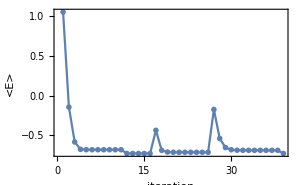

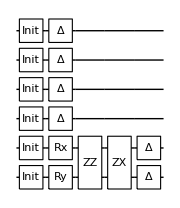
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Ry_0[-1.57069],Rx_1[3.14159],ZZ_(0,1),ZX_(1,0),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 00:07:43 with grad NGAN

@cycle1:Fri 24 Feb 2023 00:10:56, fev:788, <E>: -0.8298951919443845 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 7, 30}[improved well, updated]

@cycle2:Fri 24 Feb 2023 00:13:49, fev:1279, <E>: -0.8298951919443845 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 7, 41}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 00:18:23, fev:1897, <E>: -0.8298951919443845 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 7, 64}[worse, aborted]Slowing down

dist 0.47 ; runtime 10.7154 min ; ϵ=0.193978

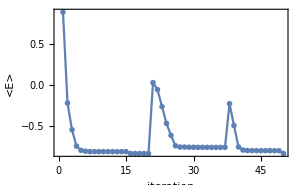

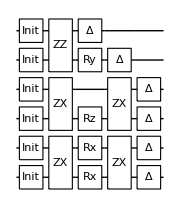
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(3,2),ZX_(1,0),ZZ_(4,5),Rz_2[3.0097],Rx_0[3.14134],Ry_4[-0.0338916],Rx_1[3.14063],ZX_(1,0),ZX_(3,2),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 00:18:26 with grad NGAN

@cycle1:Fri 24 Feb 2023 00:21:23, fev:711, <E>: -0.8669049617970396 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 0, 45}[improved well, updated]

@cycle2:Fri 24 Feb 2023 00:24:12, fev:1181, <E>: -0.8669049617970396 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 0, 69}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 00:29:23, fev:1797, <E>: -0.8669049617970396 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 0, 101}[worse, aborted]Slowing down

dist 0.53 ; runtime 11.0128 min ; ϵ=0.19745

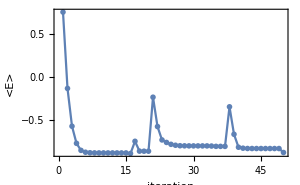

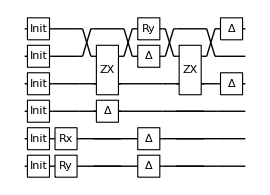
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Ry_0[-3.14086],Rx_1[-3.14159],ZX_(5,3),Ry_5[-3.14159],ZX_(5,3),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 00:29:27 with grad NGAN

@cycle1:Fri 24 Feb 2023 00:32:31, fev:744, <E>: -0.9177527285789624 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 6, 33}[improved well, updated]

@cycle2:Fri 24 Feb 2023 00:35:42, fev:1232, <E>: -0.9177527285789624 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 6, 44}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 00:41:48, fev:2347, <E>: -0.9305296435817947 nansatz: 36 merged-smallθ-metric-bf-gmerged: {1, 24, 0, 12, 71}[improved well, updated]

@cycle4:Fri 24 Feb 2023 00:49:37, fev:3007, <E>: -0.9305296435817947 nansatz: 36 merged-smallθ-metric-bf-gmerged: {1, 24, 0, 12, 101}[worse, aborted]Slowing down

@cycle5:Fri 24 Feb 2023 01:00:07, fev:3825, <E>: -0.9305296435817947 nansatz: 36 merged-smallθ-metric-bf-gmerged: {1, 24, 0, 12, 131}[worse, aborted]Slowing down

dist 0.59 ; runtime 31.2051 min ; ϵ=0.181931

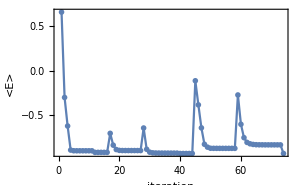

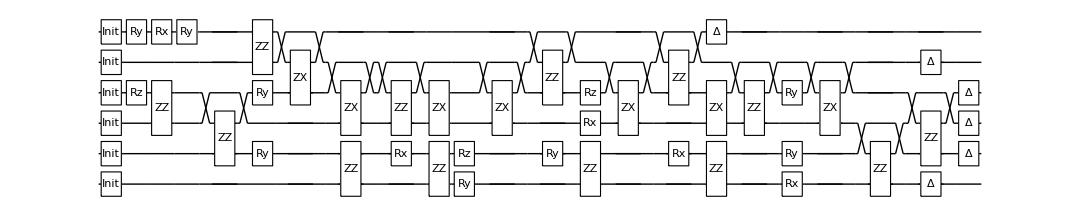
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Rz_3[1.42369],Ry_5[1.57134],Rx_5[1.37391],ZZ_(2,3),Ry_5[-1.57156],ZZ_(1,3),Ry_1[-0.167064],Ry_3[1.4712],ZZ_(4,5),ZX_(5,3),ZX_(4,2),ZZ_(0,1),ZZ_(2,4),Rx_1[-0.0829459],ZZ_(0,1),ZX_(3,2),Ry_0[-3.14159],Rz_1[-0.00185616],ZX_(4,2),ZZ_(3,5),Ry_1[3.01143],Rz_3[0.127135],Rx_2[0.00458725],ZZ_(0,1),ZX_(4,2),ZZ_(3,5),Rx_1[0.0763071],ZX_(3,2),ZZ_(0,1),ZZ_(2,4),Ry_3[-1.56597],Ry_1[0.0305255],Rx_0[-6.0863×10^-6],ZX_(4,2),ZZ_(0,2),ZZ_(1,3),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 01:00:39 with grad NGAN

@cycle1:Fri 24 Feb 2023 01:03:59, fev:824, <E>: -0.9534987187389553 nansatz: 13 merged-smallθ-metric-bf-gmerged: {4, 9, 0, 0, 33}[improved well, updated]

@cycle2:Fri 24 Feb 2023 01:07:16, fev:1284, <E>: -0.9534987187389553 nansatz: 13 merged-smallθ-metric-bf-gmerged: {4, 9, 0, 0, 54}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 01:11:53, fev:1880, <E>: -0.9534987187389553 nansatz: 13 merged-smallθ-metric-bf-gmerged: {4, 9, 0, 0, 83}[worse, aborted]Slowing down

dist 0.65 ; runtime 11.2522 min ; ϵ=0.167571

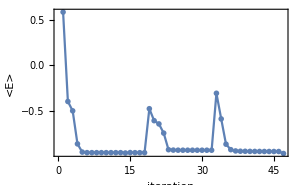

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Rx_1[-3.14159],Rx_0[3.14148],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 01:11:54 with grad NGAN

@cycle1:Fri 24 Feb 2023 01:14:53, fev:751, <E>: -0.44186841092007223 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 0, 30}[improved well, updated]

@cycle2:Fri 24 Feb 2023 01:18:26, fev:1381, <E>: -0.4688225698309069 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 39, 0, 0, 54}[improved well, updated]

@cycle3:Fri 24 Feb 2023 01:21:38, fev:2030, <E>: -0.4220352908851308 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 57, 0, 0, 79}[improved well, updated]

@cycle4:Fri 24 Feb 2023 01:25:06, fev:2710, <E>: -0.3917748269683351 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 72, 0, 0, 90}[improved well, updated]

@cycle5:Fri 24 Feb 2023 01:30:21, fev:3404, <E>: -0.8701479564703096 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 88, 0, 17, 107}[improved well, updated]

@cycle6:Fri 24 Feb 2023 01:34:05, fev:3863, <E>: -0.8701479564703096 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 88, 0, 17, 116}[worse, aborted]Slowing down

@cycle7:Fri 24 Feb 2023 01:38:56, fev:4405, <E>: -0.8701479564703096 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 88, 0, 17, 131}[worse, aborted]Slowing down

dist 0.71 ; runtime 27.0305 min ; ϵ=0.266602

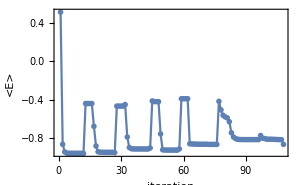

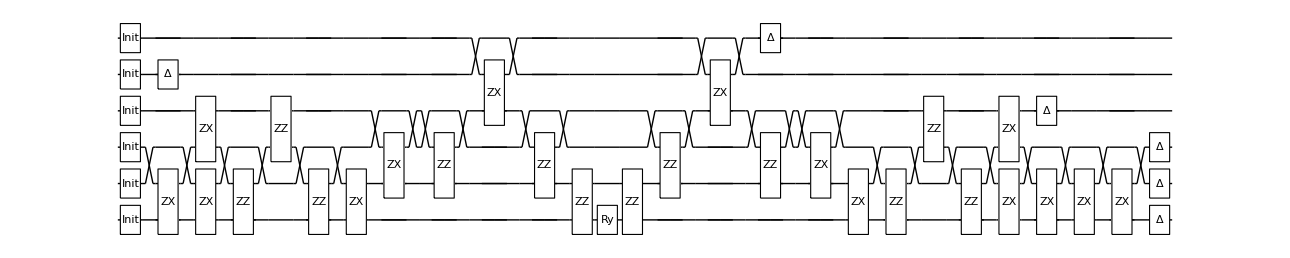
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(2,0),ZX_(1,0),ZX_(3,2),ZZ_(0,2),ZZ_(2,3),ZZ_(0,2),ZX_(1,0),ZX_(3,1),ZZ_(1,3),ZX_(5,3),ZZ_(1,3),ZZ_(0,1),Ry_0[-3.1402],ZZ_(0,1),ZZ_(1,3),ZX_(5,3),ZZ_(1,3),ZX_(3,1),ZX_(1,0),ZZ_(0,2),ZZ_(2,3),ZZ_(0,2),ZX_(1,0),ZX_(3,2),ZX_(2,0),ZX_(1,0),ZX_(2,0),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 01:38:56 with grad NGAN

@cycle1:Fri 24 Feb 2023 01:41:51, fev:762, <E>: -0.45337848690214055 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 0, 24}[improved well, updated]

@cycle2:Fri 24 Feb 2023 01:45:21, fev:1393, <E>: -0.976533890751897 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 8, 38}[improved well, updated]

@cycle3:Fri 24 Feb 2023 01:47:00, fev:1883, <E>: -0.9805512068892319 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 12, 50}[improved well, updated]

@cycle4:Fri 24 Feb 2023 01:48:19, fev:2293, <E>: -0.9805512068892319 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 12, 57}[worse, aborted]Slowing down

@cycle5:Fri 24 Feb 2023 01:50:18, fev:2802, <E>: -0.9805512068892319 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 12, 80}[worse, aborted]Slowing down

dist 0.77 ; runtime 11.3599 min ; ϵ=0.155778

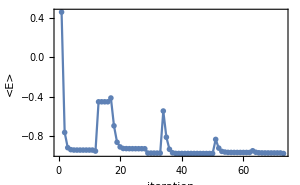

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Ry_0[-3.14091],Rx_1[-3.1415],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 01:50:18 with grad NGAN

@cycle1:Fri 24 Feb 2023 01:53:33, fev:739, <E>: -0.5283493808034194 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 9, 0, 0, 33}[improved well, updated]

@cycle2:Fri 24 Feb 2023 01:57:12, fev:1419, <E>: -0.5001604990148476 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 30, 0, 14, 59}[improved well, updated]

@cycle3:Fri 24 Feb 2023 02:00:48, fev:2139, <E>: -0.46756039840873365 nansatz: 19 merged-smallθ-metric-bf-gmerged: {2, 48, 0, 14, 74}[improved well, updated]

@cycle4:Fri 24 Feb 2023 02:05:54, fev:2988, <E>: -0.5234350682027928 nansatz: 4 merged-smallθ-metric-bf-gmerged: {2, 67, 1, 40, 93}[improved well, updated]

@cycle5:Fri 24 Feb 2023 02:08:53, fev:3679, <E>: -0.97956862970235 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 79, 1, 59, 118}[improved well, updated]

@cycle6:Fri 24 Feb 2023 02:10:16, fev:4090, <E>: -0.97956862970235 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 79, 1, 59, 131}[worse, aborted]Slowing down

@cycle7:Fri 24 Feb 2023 02:12:27, fev:4631, <E>: -0.97956862970235 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 79, 1, 59, 148}[worse, aborted]Slowing down

dist 0.83 ; runtime 22.1558 min ; ϵ=0.151389

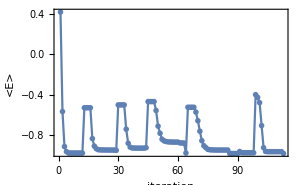

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Rx_1[3.14159],Ry_0[3.14159],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 02:12:27 with grad NGAN

@cycle1:Fri 24 Feb 2023 02:15:58, fev:884, <E>: -0.969425943578819 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 2, 37}[improved well, updated]

@cycle2:Fri 24 Feb 2023 02:19:01, fev:1312, <E>: -0.969425943578819 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 2, 50}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 02:24:42, fev:1911, <E>: -0.969425943578819 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 2, 63}[worse, aborted]Slowing down

dist 0.89 ; runtime 12.3959 min ; ϵ=0.152825

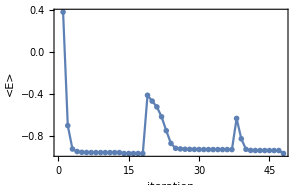

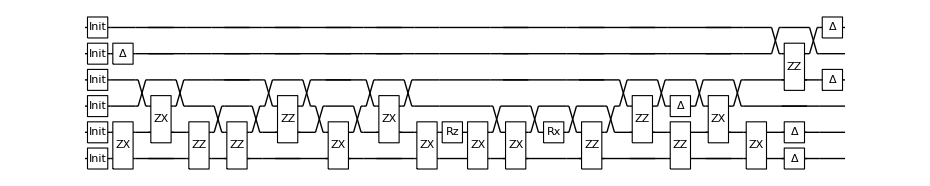
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(1,0),ZX_(3,1),ZZ_(0,1),ZZ_(0,2),ZZ_(1,3),ZX_(2,0),ZX_(3,1),ZX_(1,0),Rz_1[0.0522654],ZX_(1,0),ZX_(2,0),Rx_1[-1.56887],ZZ_(0,2),ZZ_(1,3),ZZ_(0,1),ZX_(3,1),ZX_(1,0),ZZ_(3,5),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 02:24:51 with grad NGAN

@cycle1:Fri 24 Feb 2023 02:27:50, fev:694, <E>: -0.5494026673228892 nansatz: 1 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 6, 42}[improved well, updated]

@cycle2:Fri 24 Feb 2023 02:30:28, fev:1328, <E>: -0.479903894195509 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 6, 74}[improved well, updated]

@cycle3:Fri 24 Feb 2023 02:33:46, fev:2066, <E>: -0.9207108184121038 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 43, 0, 23, 85}[improved well, updated]

@cycle4:Fri 24 Feb 2023 02:35:51, fev:2500, <E>: -0.9207108184121038 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 43, 0, 23, 96}[worse, aborted]Slowing down

@cycle5:Fri 24 Feb 2023 02:39:28, fev:3299, <E>: -0.5804971655368865 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 57, 0, 27, 115}[improved well, updated]

@cycle6:Fri 24 Feb 2023 02:46:42, fev:4401, <E>: -0.46559163274890025 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 82, 0, 27, 144}[improved well, updated]

@cycle7:Fri 24 Feb 2023 02:55:11, fev:5473, <E>: -0.5078472303344874 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 107, 0, 53, 166}[improved well, updated]

@cycle8:Fri 24 Feb 2023 03:00:34, fev:6451, <E>: -0.9570936459204306 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 130, 0, 72, 185}[improved well, updated]

@cycle9:Fri 24 Feb 2023 03:03:05, fev:6939, <E>: -0.9570936459204306 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 130, 0, 72, 203}[worse, aborted]Slowing down

@cycle10:Fri 24 Feb 2023 03:06:29, fev:7610, <E>: -0.9570936459204306 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 130, 0, 72, 227}[worse, aborted]Slowing down

dist 0.95 ; runtime 41.6641 min ; ϵ=0.154246

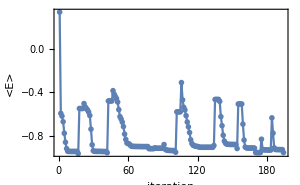

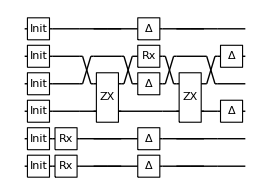
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Rx_0[-3.14159],Rx_1[3.14159],ZX_(4,2),Rx_4[3.14122],ZX_(4,2),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 03:06:31 with grad NGAN

@cycle1:Fri 24 Feb 2023 03:10:05, fev:847, <E>: -0.9472110994522213 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 2, 20}[improved well, updated]

@cycle2:Fri 24 Feb 2023 03:14:35, fev:1355, <E>: -0.9472110994522213 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 2, 38}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 03:21:00, fev:1982, <E>: -0.9472110994522213 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 2, 63}[worse, aborted]Slowing down

dist 1. ; runtime 14.7142 min ; ϵ=0.153939

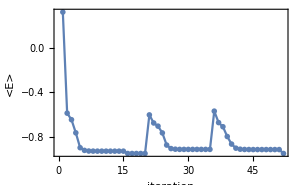

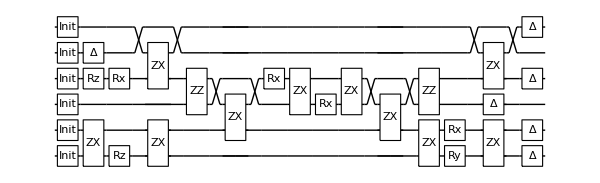
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Rz_3[0.836969],ZX_(1,0),Rx_3[-0.0171061],Rz_0[3.04194],ZX_(5,3),ZX_(1,0),ZZ_(2,3),ZX_(3,1),Rx_3[-0.519133],ZX_(3,2),Rx_2[3.14146],ZX_(3,2),ZX_(3,1),ZX_(1,0),ZZ_(2,3),Ry_0[-0.00516744],Rx_1[-0.0014817],ZX_(5,3),ZX_(1,0),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 03:21:14 with grad NGAN

@cycle1:Fri 24 Feb 2023 03:24:12, fev:720, <E>: -0.9129182348718453 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 14, 1, 9, 35}[improved well, updated]

@cycle2:Fri 24 Feb 2023 03:26:49, fev:1181, <E>: -0.9129182348718453 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 14, 1, 9, 51}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 03:30:34, fev:1763, <E>: -0.9129182348718453 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 14, 1, 9, 83}[worse, aborted]Slowing down

dist 1.2 ; runtime 9.33253 min ; ϵ=0.143823

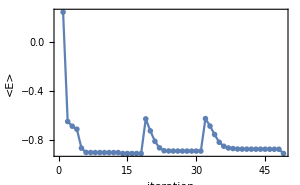

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Ry_0[3.14159],Rx_1[-3.14109],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 03:30:34 with grad NGAN

@cycle1:Fri 24 Feb 2023 03:34:42, fev:1089, <E>: -0.8621170944179876 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 6, 34}[improved well, updated]

@cycle2:Fri 24 Feb 2023 03:40:33, fev:2122, <E>: -0.7486646257071168 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 21, 0, 15, 58}[improved well, updated]

@cycle3:Fri 24 Feb 2023 03:46:13, fev:3116, <E>: -0.7517138052814027 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 44, 0, 29, 72}[improved well, updated]

@cycle4:Fri 24 Feb 2023 03:51:44, fev:4240, <E>: -0.8783205478141627 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 58, 0, 52, 87}[improved well, updated]

@cycle5:Fri 24 Feb 2023 03:55:07, fev:4714, <E>: -0.8783205478141627 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 58, 0, 52, 106}[worse, aborted]Slowing down

@cycle6:Fri 24 Feb 2023 04:00:14, fev:5338, <E>: -0.8783205478141627 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 58, 0, 52, 125}[worse, aborted]Slowing down

dist 1.4 ; runtime 29.801 min ; ϵ=0.137148

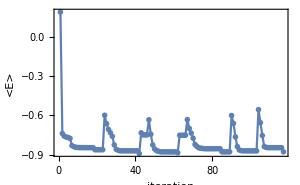

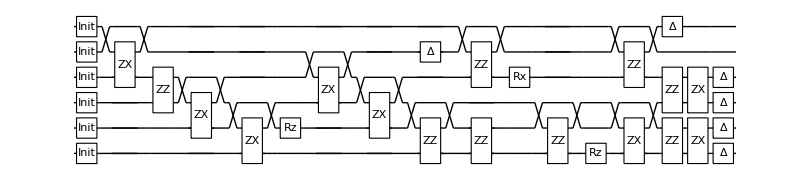
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(5,3),ZZ_(2,3),ZX_(3,1),ZX_(2,0),Rz_1[-0.410429],ZX_(4,2),ZX_(3,1),ZZ_(0,2),ZZ_(3,5),ZZ_(0,1),Rx_3[-1.64311],ZZ_(0,2),Rz_0[-3.13412],ZZ_(3,5),ZX_(2,0),ZZ_(2,3),ZZ_(0,1),ZX_(3,2),ZX_(1,0),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 04:00:22 with grad NGAN

@cycle1:Fri 24 Feb 2023 04:03:24, fev:653, <E>: -0.5319283791758003 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 4, 21}[improved well, updated]

@cycle2:Fri 24 Feb 2023 04:06:59, fev:1615, <E>: -0.8015872452968188 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 15, 35}[improved well, updated]

@cycle3:Fri 24 Feb 2023 04:10:12, fev:2620, <E>: -0.819975694053388 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 33, 0, 28, 49}[improved well, updated]

@cycle4:Fri 24 Feb 2023 04:12:33, fev:3059, <E>: -0.819975694053388 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 33, 0, 28, 56}[worse, aborted]Slowing down

@cycle5:Fri 24 Feb 2023 04:16:07, fev:3610, <E>: -0.819975694053388 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 33, 0, 28, 71}[worse, aborted]Slowing down

dist 1.6 ; runtime 15.904 min ; ϵ=0.163497

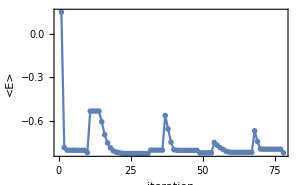

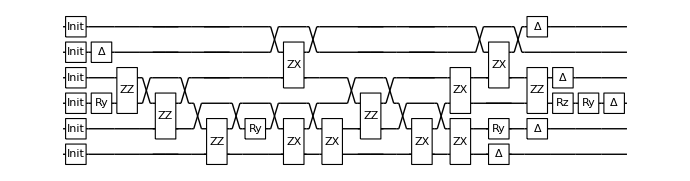
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Ry_2[1.55072],ZZ_(2,3),ZZ_(1,3),ZZ_(0,2),Ry_1[-3.14143],ZX_(2,0),ZX_(5,3),ZX_(1,0),ZZ_(1,3),ZX_(2,0),ZX_(3,2),ZX_(1,0),ZX_(5,3),Ry_1[1.3424×10^-7],ZZ_(2,3),Rz_2[1.63019],Ry_2[-1.43769],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 04:16:17 with grad NGAN

@cycle1:Fri 24 Feb 2023 04:19:01, fev:659, <E>: -0.6374625993502803 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 0, 42}[improved well, updated]

@cycle2:Fri 24 Feb 2023 04:22:04, fev:1337, <E>: -0.8361176174186269 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 33, 0, 19, 61}[improved well, updated]

@cycle3:Fri 24 Feb 2023 04:23:51, fev:1787, <E>: -0.8361176174186269 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 33, 0, 19, 70}[worse, aborted]Slowing down

@cycle4:Fri 24 Feb 2023 04:26:49, fev:2607, <E>: -0.8373682742587323 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 40, 0, 21, 85}[improved well, updated]

@cycle5:Fri 24 Feb 2023 04:30:37, fev:3174, <E>: -0.8373682742587323 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 40, 0, 21, 103}[worse, aborted]Slowing down

@cycle6:Fri 24 Feb 2023 04:36:26, fev:3897, <E>: -0.8373682742587323 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 40, 0, 21, 121}[worse, aborted]Slowing down

dist 1.8 ; runtime 20.3344 min ; ϵ=0.124449

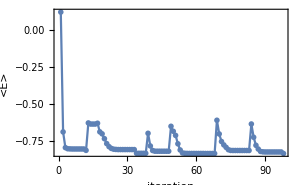

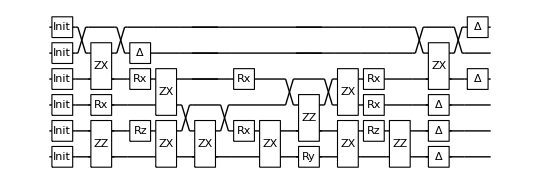
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(5,3),Rx_2[1.56991],ZZ_(0,1),Rx_3[1.5708],Rz_1[-0.695156],ZX_(3,2),ZX_(1,0),ZX_(2,0),Rx_1[3.14159],Rx_3[-3.14159],ZX_(1,0),ZZ_(1,3),Ry_0[-0.554075],ZX_(1,0),ZX_(3,2),Rz_1[1.279],Rx_2[-1.5708],Rx_3[1.5708],ZZ_(0,1),ZX_(5,3),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 04:36:37 with grad NGAN

@cycle1:Fri 24 Feb 2023 04:39:24, fev:645, <E>: -0.8283065953616933 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 2, 34}[improved well, updated]

@cycle2:Fri 24 Feb 2023 04:42:30, fev:1113, <E>: -0.8283065953616933 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 2, 52}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 04:47:04, fev:1675, <E>: -0.8283065953616933 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 2, 74}[worse, aborted]Slowing down

dist 2. ; runtime 10.4994 min ; ϵ=0.120335

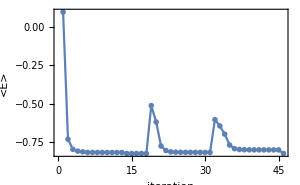

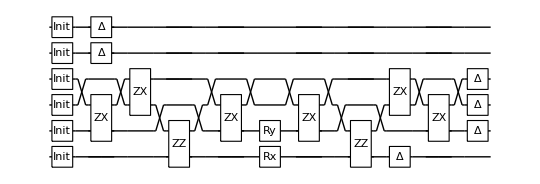
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(3,1),ZX_(3,2),ZZ_(0,2),ZX_(3,1),Ry_1[0.277386],Rx_0[-3.14158],ZX_(3,1),ZZ_(0,2),ZX_(3,2),ZX_(3,1),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 04:47:07 with grad NGAN

@cycle1:Fri 24 Feb 2023 04:50:37, fev:868, <E>: -0.8558858456004886 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 6, 29}[improved well, updated]

@cycle2:Fri 24 Feb 2023 04:54:15, fev:1323, <E>: -0.8558858456004886 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 6, 51}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 04:59:45, fev:1914, <E>: -0.8558858456004886 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 6, 77}[worse, aborted]Slowing down

dist 2.2 ; runtime 12.8243 min ; ϵ=0.0853382

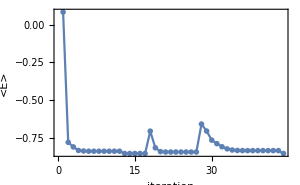

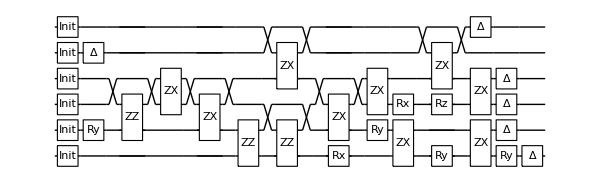
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Ry_1[1.1054],ZZ_(1,3),ZX_(3,2),ZX_(3,1),ZZ_(0,1),ZX_(5,3),ZZ_(0,2),ZX_(3,1),Rx_0[-1.57422],ZX_(3,2),Ry_1[-1.57152],ZX_(1,0),Rx_2[2.38216],ZX_(5,3),Ry_0[1.57112],Rz_2[-1.58929],ZX_(1,0),ZX_(3,2),Ry_0[1.5726],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 04:59:57 with grad NGAN

@cycle1:Fri 24 Feb 2023 05:02:58, fev:754, <E>: -0.8517054400301157 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 14, 2, 10, 30}[improved well, updated]

@cycle2:Fri 24 Feb 2023 05:06:08, fev:1441, <E>: -0.8594977486045267 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 30, 2, 24, 58}[improved well, updated]

@cycle3:Fri 24 Feb 2023 05:09:05, fev:1884, <E>: -0.8594977486045267 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 30, 2, 24, 80}[worse, aborted]Slowing down

@cycle4:Fri 24 Feb 2023 05:13:46, fev:2457, <E>: -0.8594977486045267 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 30, 2, 24, 97}[worse, aborted]Slowing down

dist 2.4 ; runtime 13.908 min ; ϵ=0.0777572

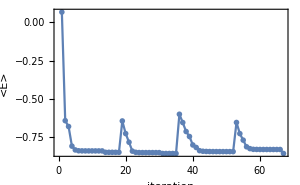

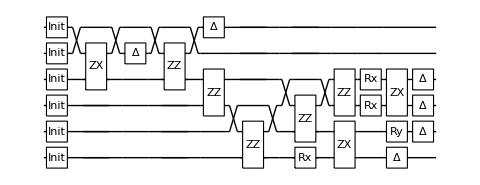
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(5,3),ZZ_(3,5),ZZ_(2,3),ZZ_(0,2),ZZ_(1,3),Rx_0[-1.57073],ZZ_(2,3),ZX_(1,0),Rx_3[1.57084],Rx_2[1.57051],ZX_(3,2),Ry_1[-3.1415],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 05:13:51 with grad NGAN

@cycle1:Fri 24 Feb 2023 05:16:56, fev:754, <E>: -0.47927797559509056 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 9, 0, 7, 34}[improved well, updated]

@cycle2:Fri 24 Feb 2023 05:20:07, fev:1467, <E>: -0.5698383452221982 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 31, 0, 14, 49}[improved well, updated]

@cycle3:Fri 24 Feb 2023 05:23:31, fev:2134, <E>: -0.4773556332520933 nansatz: 4 merged-smallθ-metric-bf-gmerged: {2, 52, 0, 31, 69}[improved well, updated]

@cycle4:Fri 24 Feb 2023 05:26:22, fev:2751, <E>: -0.4683114971837115 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 80, 0, 39, 90}[improved well, updated]

@cycle5:Fri 24 Feb 2023 05:28:53, fev:3379, <E>: -0.8430882482877878 nansatz: 8 merged-smallθ-metric-bf-gmerged: {2, 98, 0, 47, 111}[improved well, updated]

@cycle6:Fri 24 Feb 2023 05:30:28, fev:3737, <E>: -0.8430882482877878 nansatz: 8 merged-smallθ-metric-bf-gmerged: {2, 98, 0, 47, 128}[worse, aborted]Slowing down

@cycle7:Fri 24 Feb 2023 05:33:04, fev:4477, <E>: -0.8518323502232317 nansatz: 5 merged-smallθ-metric-bf-gmerged: {2, 110, 0, 53, 152}[improved well, updated]

@cycle8:Fri 24 Feb 2023 05:35:29, fev:5018, <E>: -0.8518323502232317 nansatz: 5 merged-smallθ-metric-bf-gmerged: {2, 110, 0, 53, 164}[worse, aborted]Slowing down

@cycle9:Fri 24 Feb 2023 05:39:05, fev:5681, <E>: -0.8518323502232317 nansatz: 5 merged-smallθ-metric-bf-gmerged: {2, 110, 0, 53, 193}[worse, aborted]Slowing down

dist 2.5 ; runtime 25.2557 min ; ϵ=0.0842226

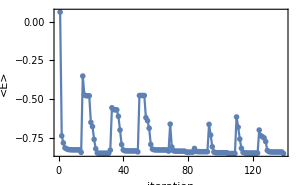

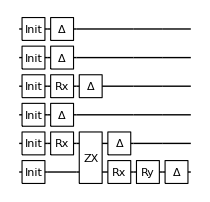
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Rx_1[3.14091],Rx_3[-3.14159],ZX_(1,0),Rx_0[-1.5708],Ry_0[3.14159],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 05:39:07 with grad NGAN

@cycle1:Fri 24 Feb 2023 05:42:04, fev:728, <E>: -0.4897907022159152 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 0, 43}[improved well, updated]

@cycle2:Fri 24 Feb 2023 05:45:34, fev:1298, <E>: -0.48936610404113556 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 8, 57}[improved well, updated]

@cycle3:Fri 24 Feb 2023 05:47:55, fev:1824, <E>: -0.8466875060192102 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 51, 0, 11, 81}[improved well, updated]

@cycle4:Fri 24 Feb 2023 05:49:10, fev:2193, <E>: -0.8466875060192102 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 51, 0, 11, 96}[worse, aborted]Slowing down

@cycle5:Fri 24 Feb 2023 05:51:23, fev:2693, <E>: -0.8466875060192102 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 51, 0, 11, 114}[worse, aborted]Slowing down

dist 2.75 ; runtime 12.2787 min ; ϵ=0.0876615

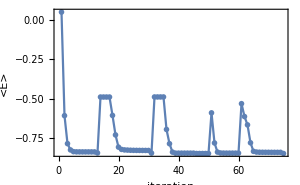

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Ry_0[-3.14159],Rx_2[3.1408],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 05:51:23 with grad NGAN

@cycle1:Fri 24 Feb 2023 05:54:17, fev:595, <E>: -0.8471017630693106 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 3, 26}[improved well, updated]

@cycle2:Fri 24 Feb 2023 05:56:26, fev:990, <E>: -0.8471017630693106 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 3, 58}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 06:00:17, fev:1549, <E>: -0.8471017630693106 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 3, 87}[worse, aborted]Slowing down

dist 3. ; runtime 8.89189 min ; ϵ=0.0865301

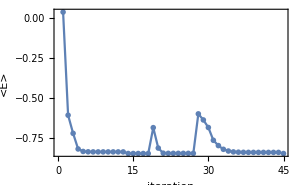

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Ry_0[-3.14072],Ry_2[-3.14159],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 06:00:17 with grad NGAN

@cycle1:Fri 24 Feb 2023 06:03:53, fev:867, <E>: -0.4970061184625715 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 5, 29}[improved well, updated]

@cycle2:Fri 24 Feb 2023 06:06:40, fev:1468, <E>: -0.8519048003483247 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 17, 61}[improved well, updated]

@cycle3:Fri 24 Feb 2023 06:07:54, fev:1835, <E>: -0.8519048003483247 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 17, 78}[worse, aborted]Slowing down

@cycle4:Fri 24 Feb 2023 06:10:07, fev:2340, <E>: -0.8519048003483247 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 17, 94}[worse, aborted]Slowing down

dist 3.25 ; runtime 9.82884 min ; ϵ=0.0814365

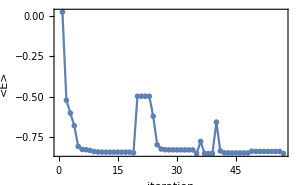

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Rx_3[-3.14159],Rx_1[-3.14252],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 06:10:07 with grad NGAN

@cycle1:Fri 24 Feb 2023 06:13:21, fev:822, <E>: -0.847294579988309 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 4, 37}[improved well, updated]

@cycle2:Fri 24 Feb 2023 06:16:09, fev:1266, <E>: -0.847294579988309 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 4, 54}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 06:20:31, fev:1825, <E>: -0.847294579988309 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 4, 80}[worse, aborted]Slowing down

dist 3.5 ; runtime 10.4663 min ; ϵ=0.0859338

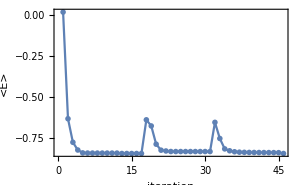

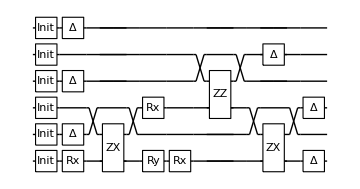
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Rx_0[-3.14158],ZX_(2,0),Ry_0[-2.4625],Rx_2[3.141],Rx_0[9.34061×10^-6],ZZ_(2,4),ZX_(2,0),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 06:20:35 with grad NGAN

@cycle1:Fri 24 Feb 2023 06:23:32, fev:731, <E>: -0.8472849303642285 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 12, 25}[improved well, updated]

@cycle2:Fri 24 Feb 2023 06:26:03, fev:1137, <E>: -0.8472849303642285 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 12, 37}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 06:29:48, fev:1671, <E>: -0.8472849303642285 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 12, 60}[worse, aborted]Slowing down

dist 3.75 ; runtime 9.22722 min ; ϵ=0.0859015

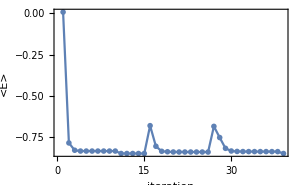

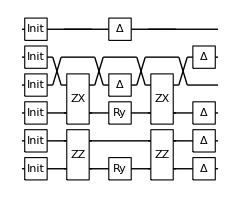
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(4,2),ZZ_(0,1),Ry_2[-1.30192],Ry_0[-3.14134],ZX_(4,2),ZZ_(0,1),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 06:29:49 with grad NGAN

@cycle1:Fri 24 Feb 2023 06:33:15, fev:891, <E>: -0.8486739351873396 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 2, 33}[improved well, updated]

@cycle2:Fri 24 Feb 2023 06:37:30, fev:1334, <E>: -0.8486739351873396 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 2, 60}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 06:43:53, fev:1916, <E>: -0.8486739351873396 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 2, 80}[worse, aborted]Slowing down

dist 4. ; runtime 14.5308 min ; ϵ=0.0844974

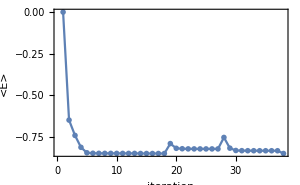

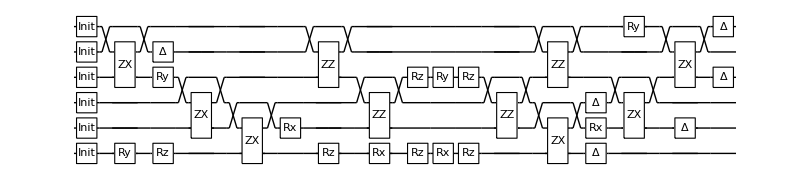
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(5,3),Ry_0[0.00984245],Ry_3[-0.473638],Rz_0[-1.37826],ZX_(3,1),ZX_(2,0),Rx_1[-0.325115],ZZ_(3,5),Rz_0[-0.292938],ZZ_(1,3),Rx_0[-0.572582],Rz_3[-0.0986844],Rz_0[-1.90752],Ry_3[-0.0000757981],Rx_0[-0.757045],Rz_3[0.0986863],Rz_0[-0.730412],ZZ_(1,3),ZX_(2,0),ZZ_(3,5),Rx_1[2.81628],ZX_(3,1),Ry_5[2.37947×10^-6],ZX_(5,3),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 06:44:21 with grad NGAN

@cycle1:Fri 24 Feb 2023 06:47:19, fev:708, <E>: -0.8471985818617174 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 3, 32}[improved well, updated]

@cycle2:Fri 24 Feb 2023 06:50:28, fev:1146, <E>: -0.8471985818617174 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 3, 63}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 06:54:38, fev:1666, <E>: -0.8471985818617174 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 3, 87}[worse, aborted]Slowing down

dist 4.25 ; runtime 10.3458 min ; ϵ=0.0859676

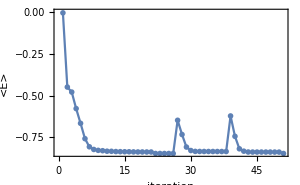

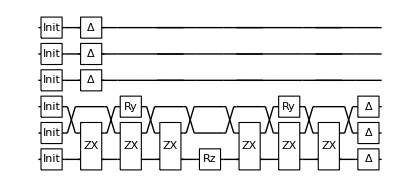
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(2,0),Ry_2[0.00101575],ZX_(1,0),ZX_(2,0),Rz_0[3.14163],ZX_(2,0),ZX_(1,0),Ry_2[-3.14141],ZX_(2,0),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 06:54:41 with grad NGAN

@cycle1:Fri 24 Feb 2023 06:57:40, fev:712, <E>: -0.4983211001039934 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 0, 26}[improved well, updated]

@cycle2:Fri 24 Feb 2023 07:01:07, fev:1364, <E>: -0.4444912341837287 nansatz: 1 merged-smallθ-metric-bf-gmerged: {1, 32, 0, 19, 37}[improved well, updated]

@cycle3:Fri 24 Feb 2023 07:03:11, fev:1817, <E>: -0.4444912345343811 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 45, 0, 19, 61}[improved well, updated]

@cycle4:Fri 24 Feb 2023 07:05:37, fev:2345, <E>: -0.5002961575011662 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 63, 0, 22, 91}[improved well, updated]

@cycle5:Fri 24 Feb 2023 07:08:52, fev:2979, <E>: -0.8343860358342484 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 79, 0, 40, 117}[improved well, updated]

@cycle6:Fri 24 Feb 2023 07:10:14, fev:3361, <E>: -0.8343860358342484 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 79, 0, 40, 125}[worse, aborted]Slowing down

@cycle7:Fri 24 Feb 2023 07:12:42, fev:4119, <E>: -0.8479109374465447 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 90, 0, 48, 141}[improved well, updated]

@cycle8:Fri 24 Feb 2023 07:14:57, fev:4634, <E>: -0.8479109374465447 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 90, 0, 48, 160}[worse, aborted]Slowing down

@cycle9:Fri 24 Feb 2023 07:18:22, fev:5291, <E>: -0.8479109374465447 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 90, 0, 48, 185}[worse, aborted]Slowing down

dist 4.5 ; runtime 23.7031 min ; ϵ=0.0852535

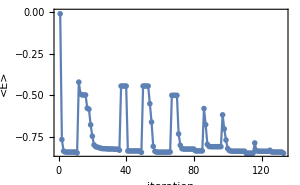

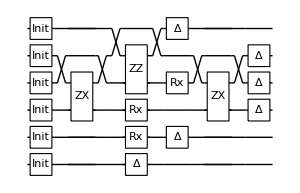
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(4,2),ZZ_(3,5),Rx_1[-3.14159],Rx_2[-3.14159],Rx_3[-3.14159],ZX_(4,2),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 07:18:24 with grad NGAN

@cycle1:Fri 24 Feb 2023 07:21:04, fev:590, <E>: -0.851698085840148 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 0, 24}[improved well, updated]

@cycle2:Fri 24 Feb 2023 07:23:11, fev:974, <E>: -0.851698085840148 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 0, 47}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 07:26:47, fev:1509, <E>: -0.851698085840148 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 0, 80}[worse, aborted]Slowing down

dist 4.75 ; runtime 8.39254 min ; ϵ=0.0814658

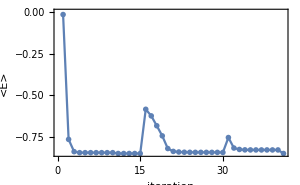

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Rx_1[3.14159],Ry_3[-3.14159],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 07:26:47 with grad NGAN

@cycle1:Fri 24 Feb 2023 07:29:46, fev:665, <E>: -0.45811923024908974 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 8, 32}[improved well, updated]

@cycle2:Fri 24 Feb 2023 07:32:10, fev:1263, <E>: -0.5768025418218696 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 8, 60}[improved well, updated]

@cycle3:Fri 24 Feb 2023 07:35:35, fev:1975, <E>: -0.6326183596338644 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 44, 0, 21, 70}[improved well, updated]

@cycle4:Fri 24 Feb 2023 07:39:02, fev:2674, <E>: -0.8338051497641072 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 65, 0, 32, 78}[improved well, updated]

@cycle5:Fri 24 Feb 2023 07:41:11, fev:3103, <E>: -0.8338051497641072 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 65, 0, 32, 89}[worse, aborted]Slowing down

@cycle6:Fri 24 Feb 2023 07:44:07, fev:3607, <E>: -0.8338051497641072 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 65, 0, 32, 98}[worse, aborted]Slowing down

dist 5. ; runtime 17.3257 min ; ϵ=0.0993586

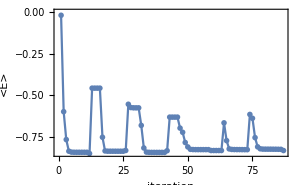

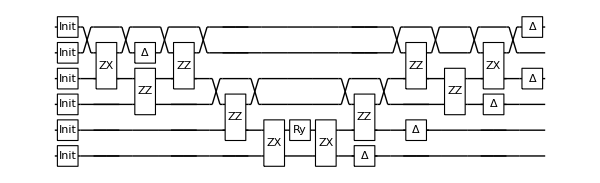
-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(5,3),ZZ_(2,3),ZZ_(3,5),ZZ_(1,3),ZX_(1,0),Ry_1[3.1409],ZX_(1,0),ZZ_(1,3),ZZ_(3,5),ZZ_(2,3),ZX_(5,3),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

### Static noise only: vqeH22

Table[
  {distance, hamfile, hamiltonian, groundstate} = Values@data;
  dev = SuperconductingHub[StdPassiveNoise -> False];
  conf = DefaultConfig[dev, hamiltonian];
  conf["groundstate"] = groundstate;
   conf["virtualmeas"] = {};
  conf["initcirc"] = {};
     res = VQEonVQD[conf];
  {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
  AppendTo[vqeH22, <|"distance" -> distance, "hamiltonian" -> hamiltonian, "runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
  DumpSave["vqeH22.mx", vqeH22];
  Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
 Print@ListPlot[Elist, ImageSize -> 300, PlotMarkers -> {"OpenMarkers"}, Joined -> True, PlotRange -> All, Frame -> True, FrameLabel -> {"iteration", "<E>"}];
  Print[DrawCircuit[ansatz, 6], ansatz /. θvars];
  , {data, gsH2}]

Compilation with automatically generated ansatz at Fri 24 Feb 2023 07:44:07 with grad NGAN

@cycle1:Fri 24 Feb 2023 07:46:24, fev:821, <E>: -0.006642680834102771 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 0, 35}[improved well, updated]

@cycle2:Fri 24 Feb 2023 07:49:16, fev:1711, <E>: -0.7769431306228154 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 34, 0, 20, 47}[improved well, updated]

@cycle3:Fri 24 Feb 2023 07:50:44, fev:2302, <E>: -0.7804549020527972 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 45, 0, 31, 61}[improved well, updated]

@cycle4:Fri 24 Feb 2023 07:51:45, fev:2696, <E>: -0.7804549020527972 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 45, 0, 31, 70}[worse, aborted]Slowing down

@cycle5:Fri 24 Feb 2023 07:53:15, fev:3267, <E>: -0.7804549020527972 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 45, 0, 31, 84}[worse, aborted]Slowing down

dist 0.35 ; runtime 9.16983 min ; ϵ=0.00881449

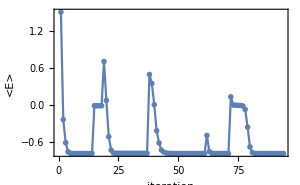

-Graphics-{Rx_0[-3.14158],Rx_1[3.14159]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 07:53:17 with grad NGAN

@cycle1:Fri 24 Feb 2023 07:55:34, fev:826, <E>: -0.9237394549980855 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 12, 26}[improved well, updated]

@cycle2:Fri 24 Feb 2023 07:58:50, fev:1910, <E>: -0.9330698917542782 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 29, 49}[improved well, updated]

@cycle3:Fri 24 Feb 2023 08:00:57, fev:2727, <E>: -0.9337390444483209 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 38, 0, 37, 60}[improved well, updated]

@cycle4:Fri 24 Feb 2023 08:02:38, fev:3201, <E>: -0.9337390444483209 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 38, 0, 37, 70}[worse, aborted]Slowing down

@cycle5:Fri 24 Feb 2023 08:04:59, fev:3819, <E>: -0.9337390444483209 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 38, 0, 37, 88}[worse, aborted]Slowing down

dist 0.41 ; runtime 11.8819 min ; ϵ=1.44412×10^-7

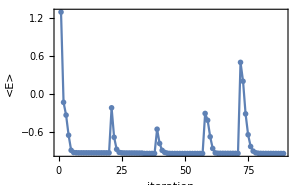

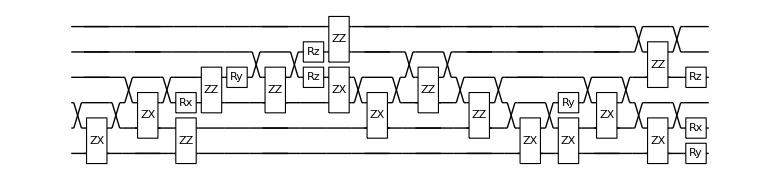
-Graphics-{ZX_(2,0),ZX_(3,1),Rx_2[-1.5708],ZZ_(0,1),ZZ_(2,3),Ry_3[-0.121655],ZZ_(2,4),Rz_4[-0.427847],Rz_3[0.0541669],ZX_(3,2),ZZ_(4,5),ZX_(3,1),ZZ_(2,4),ZZ_(1,3),ZX_(2,0),Ry_2[3.14159],ZX_(1,0),ZX_(3,1),ZX_(2,0),ZZ_(3,5),Rx_1[-3.14159],Ry_0[3.14159],Rz_3[1.54409]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 08:05:10 with grad NGAN

@cycle1:Fri 24 Feb 2023 08:07:53, fev:1124, <E>: -0.3046069315801825 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 6, 47}[improved well, updated]

@cycle2:Fri 24 Feb 2023 08:10:31, fev:1907, <E>: -0.3057963299471972 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 35, 0, 21, 77}[improved well, updated]

@cycle3:Fri 24 Feb 2023 08:12:41, fev:2650, <E>: -0.30579622204862844 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 49, 0, 26, 107}[improved well, updated]

@cycle4:Fri 24 Feb 2023 08:14:48, fev:3341, <E>: 0.021944416857733573 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 73, 0, 36, 131}[improved well, updated]

@cycle5:Fri 24 Feb 2023 08:16:54, fev:4026, <E>: -0.30573331902329826 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 95, 0, 42, 151}[improved well, updated]

@cycle6:Fri 24 Feb 2023 08:18:51, fev:4672, <E>: -1.0124847977498264 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 117, 0, 50, 172}[improved well, updated]

@cycle7:Fri 24 Feb 2023 08:19:46, fev:5038, <E>: -1.0124847977498264 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 117, 0, 50, 194}[worse, aborted]Slowing down

@cycle8:Fri 24 Feb 2023 08:21:14, fev:5572, <E>: -1.0124847977498264 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 117, 0, 50, 210}[worse, aborted]Slowing down

dist 0.47 ; runtime 16.0575 min ; ϵ=0.0113888

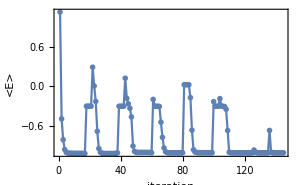

-Graphics-{Rx_1[3.14159],Rx_0[3.14159]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 08:21:14 with grad NGAN

@cycle1:Fri 24 Feb 2023 08:23:29, fev:910, <E>: -0.12603948496854958 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 14, 29}[improved well, updated]

@cycle2:Fri 24 Feb 2023 08:25:36, fev:1600, <E>: -1.066564860469592 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 33, 0, 25, 51}[improved well, updated]

@cycle3:Fri 24 Feb 2023 08:26:42, fev:2013, <E>: -1.066564860469592 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 33, 0, 25, 65}[worse, aborted]Slowing down

@cycle4:Fri 24 Feb 2023 08:28:15, fev:2550, <E>: -1.066564860469592 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 33, 0, 25, 77}[worse, aborted]Slowing down

dist 0.53 ; runtime 7.01893 min ; ϵ=0.0129939

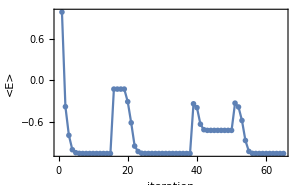

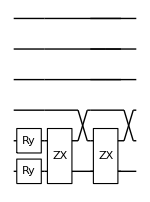
-Graphics-{Ry_0[-3.14159],Ry_1[3.1409],ZX_(1,0),ZX_(2,0)}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 08:28:15 with grad NGAN

@cycle1:Fri 24 Feb 2023 08:30:58, fev:956, <E>: -1.110219135737461 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 10, 39}[improved well, updated]

@cycle2:Fri 24 Feb 2023 08:33:28, fev:1460, <E>: -1.110219135737461 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 10, 61}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 08:38:45, fev:2873, <E>: -0.451965248169161 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 16, 80}[improved well, updated]

dist 0.59 ; runtime 16.2133 min ; ϵ=4.6×10^-10

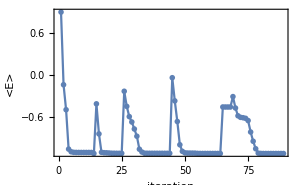

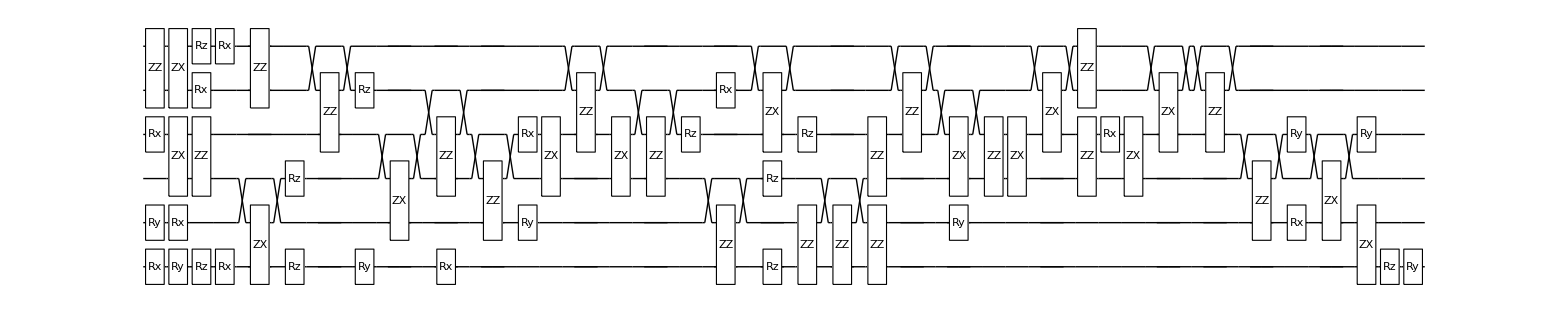
-Graphics-{ZZ_(4,5),Rx_0[0.164139],Rx_3[0.0000148617],Ry_1[-0.864149],Ry_0[-1.5708],ZX_(5,4),ZX_(3,2),Rx_1[-0.327134],Rz_0[-0.164137],Rz_5[-0.0257838],Rx_4[-1.5708],ZZ_(2,3),Rx_0[-0.83458],Rx_5[4.94425×10^-7],ZX_(2,0),ZZ_(4,5),Rz_0[0.095001],Rz_2[0.0537239],ZZ_(3,5),Rz_4[-0.279853],Ry_0[-1.57079],ZX_(3,1),ZZ_(2,4),Rx_0[0.0950031],ZZ_(1,3),Rx_3[-1.5708],Ry_1[2.93443],ZX_(3,2),ZZ_(3,5),ZX_(3,2),ZZ_(2,4),Rz_3[1.57079],ZZ_(0,2),Rx_4[-5.70832×10^-11],ZX_(5,3),Rz_0[-0.611104],Rz_2[-1.4253],Rz_3[-0.0199806],ZZ_(0,1),ZZ_(0,2),ZZ_(2,3),ZZ_(0,1),ZZ_(3,5),ZX_(4,2),Ry_1[-0.0632485],ZZ_(2,3),ZX_(3,2),ZX_(5,3),ZZ_(4,5),ZZ_(2,3),Rx_3[-1.7408],ZX_(3,2),ZX_(5,3),ZZ_(3,5),ZZ_(1,3),Ry_3[1.5708],Rx_1[1.57079],ZX_(3,1),ZX_(1,0),Ry_3[1.87961],Rz_0[-1.57083],Ry_0[-1.57074]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 08:44:28 with grad NGAN

@cycle1:Fri 24 Feb 2023 08:47:43, fev:1258, <E>: -0.4019847774560834 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 0, 31}[improved well, updated]

@cycle2:Fri 24 Feb 2023 08:51:20, fev:2312, <E>: -0.39854760878855916 nansatz: 36 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 0, 43}[improved well, updated]

@cycle3:Fri 24 Feb 2023 08:55:45, fev:3747, <E>: -0.223723634704582 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 48, 0, 27, 62}[improved well, updated]

@cycle4:Fri 24 Feb 2023 08:58:34, fev:4607, <E>: -0.4953910824341007 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 65, 0, 55, 77}[improved well, updated]

@cycle5:Fri 24 Feb 2023 09:00:54, fev:5384, <E>: -0.47467623066828046 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 78, 0, 55, 96}[improved well, updated]

@cycle6:Fri 24 Feb 2023 09:03:46, fev:6288, <E>: -0.4964083096482706 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 89, 0, 79, 101}[improved well, updated]

@cycle7:Fri 24 Feb 2023 09:07:01, fev:7432, <E>: -1.1051044711003943 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 107, 0, 87, 115}[improved well, updated]

@cycle8:Fri 24 Feb 2023 09:09:25, fev:8315, <E>: -1.1128749644852534 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 118, 0, 90, 119}[improved well, updated]

@cycle9:Fri 24 Feb 2023 09:11:09, fev:8781, <E>: -1.1128749644852534 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 118, 0, 90, 127}[worse, aborted]Slowing down

@cycle10:Fri 24 Feb 2023 09:15:12, fev:10244, <E>: -1.120098722470747 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 128, 0, 104, 139}[improved well, updated]

@cycle11:Fri 24 Feb 2023 09:17:26, fev:10844, <E>: -1.120098722470747 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 128, 0, 104, 153}[worse, aborted]Slowing down

@cycle12:Fri 24 Feb 2023 09:20:29, fev:11629, <E>: -1.120098722470747 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 128, 0, 104, 166}[worse, aborted]Slowing down

dist 0.65 ; runtime 36.1955 min ; ϵ=0.00980606

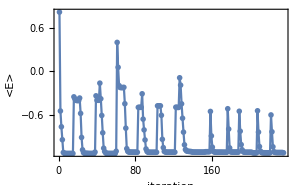

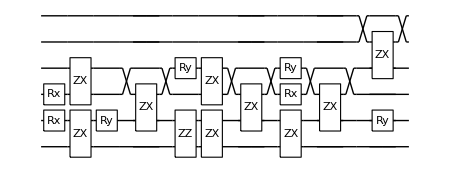
-Graphics-{Rx_2[3.0034],Rx_1[1.27404×10^-11],ZX_(1,0),ZX_(3,2),Ry_1[1.50392×10^-12],ZX_(3,1),ZZ_(0,1),Ry_3[-3.14067],ZX_(3,2),ZX_(1,0),ZX_(3,1),Rx_2[-3.00344],Ry_3[1.57081],ZX_(1,0),ZX_(3,1),ZX_(5,3),Ry_1[-1.5708]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 09:20:40 with grad NGAN

@cycle1:Fri 24 Feb 2023 09:22:43, fev:767, <E>: -0.5263262959115422 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 12, 42}[improved well, updated]

@cycle2:Fri 24 Feb 2023 09:24:45, fev:1538, <E>: -1.117500774420377 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 28, 56}[improved well, updated]

@cycle3:Fri 24 Feb 2023 09:25:48, fev:1946, <E>: -1.117500774420377 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 28, 67}[worse, aborted]Slowing down

@cycle4:Fri 24 Feb 2023 09:27:26, fev:2517, <E>: -1.117500774420377 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 28, 79}[worse, aborted]Slowing down

dist 0.71 ; runtime 6.77982 min ; ϵ=0.0192496

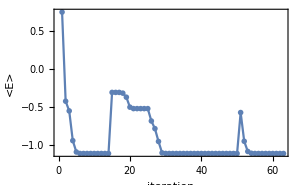

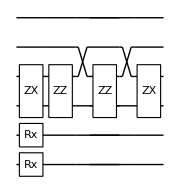
-Graphics-{Rx_1[3.14155],Rx_0[-3.14068],ZX_(3,2),ZZ_(2,3),ZZ_(2,4),ZX_(3,2)}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 09:27:27 with grad NGAN

@cycle1:Fri 24 Feb 2023 09:30:10, fev:1086, <E>: -1.1361473968846831 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 7, 32}[improved well, updated]

@cycle2:Fri 24 Feb 2023 09:32:34, fev:1578, <E>: -1.1361473968846831 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 7, 46}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 09:36:18, fev:2238, <E>: -1.1361473968846831 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 7, 65}[worse, aborted]Slowing down

dist 0.77 ; runtime 9.06256 min ; ϵ=0.000181738

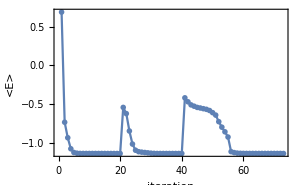

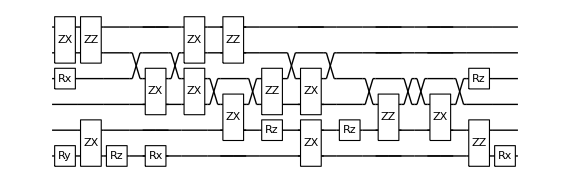
-Graphics-{Ry_0[-0.000061194],Rx_3[0.237667],ZX_(5,4),ZX_(1,0),ZZ_(4,5),Rz_0[1.43893],ZX_(4,2),Rx_0[-1.25762],ZX_(3,2),ZX_(5,4),ZX_(3,1),ZZ_(4,5),ZZ_(2,3),Rz_1[1.55801],ZX_(4,2),ZX_(1,0),Rz_1[1.58455],ZZ_(1,3),ZX_(3,1),ZZ_(0,1),Rz_3[0.109546],Rx_0[1.5708]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 09:36:31 with grad NGAN

@cycle1:Fri 24 Feb 2023 09:38:21, fev:593, <E>: -0.5631217030602382 nansatz: 1 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 0, 36}[improved well, updated]

@cycle2:Fri 24 Feb 2023 09:40:11, fev:1273, <E>: -1.1061557396025585 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 12, 60}[improved well, updated]

@cycle3:Fri 24 Feb 2023 09:41:20, fev:1711, <E>: -1.1061557396025585 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 12, 76}[worse, aborted]Slowing down

@cycle4:Fri 24 Feb 2023 09:42:55, fev:2255, <E>: -1.1061557396025585 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 12, 95}[worse, aborted]Slowing down

dist 0.83 ; runtime 6.42018 min ; ϵ=0.0248019

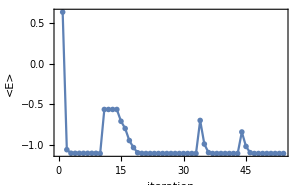

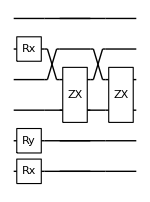
-Graphics-{Rx_0[3.14159],Rx_4[-3.14158],Ry_1[3.14159],ZX_(4,2),ZX_(3,2)}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 09:42:56 with grad NGAN

@cycle1:Fri 24 Feb 2023 09:45:37, fev:989, <E>: -0.6754370746840209 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 8, 24}[improved well, updated]

@cycle2:Fri 24 Feb 2023 09:48:32, fev:1890, <E>: -0.5579454070668826 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 34, 39}[improved well, updated]

@cycle3:Fri 24 Feb 2023 09:50:59, fev:2805, <E>: -1.0940836317716558 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 38, 0, 52, 56}[improved well, updated]

@cycle4:Fri 24 Feb 2023 09:52:32, fev:3281, <E>: -1.0940836317716558 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 38, 0, 52, 69}[worse, aborted]Slowing down

@cycle5:Fri 24 Feb 2023 09:55:10, fev:4265, <E>: -1.0941837781495336 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 46, 1, 65, 89}[improved well, updated]

@cycle6:Fri 24 Feb 2023 09:57:51, fev:5384, <E>: -1.1222302825915942 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 54, 2, 77, 105}[improved well, updated]

dist 0.89 ; runtime 17.8864 min ; ϵ=3.4442×10^-8

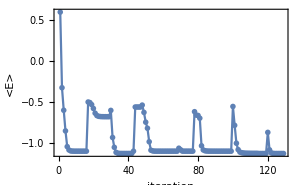

-Graphics-{Ry_1[1.55617],Rx_3[-2.50094×10^-6],ZZ_(0,1),ZZ_(3,5),ZX_(3,2),Rz_2[1.74698],ZX_(3,1),Rx_3[0.000187595],ZX_(3,2),Ry_2[-1.79334],ZZ_(0,2),Rx_2[0.434804],ZZ_(0,1),ZX_(4,2),Ry_1[2.81098],ZZ_(2,4),ZZ_(0,2),ZX_(3,2),Rx_2[-0.847828],ZX_(4,2),Ry_2[1.57067],ZX_(2,0),ZZ_(0,1),ZX_(3,2),ZX_(2,0),Ry_3[-1.5704],ZX_(3,2),Rx_3[1.57056],Ry_2[1.57092]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 10:00:49 with grad NGAN

@cycle1:Fri 24 Feb 2023 10:03:37, fev:1114, <E>: -1.0796368742007416 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 7, 42}[improved well, updated]

@cycle2:Fri 24 Feb 2023 10:07:00, fev:2223, <E>: -1.1057380911983847 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 33, 0, 26, 62}[improved well, updated]

@cycle3:Fri 24 Feb 2023 10:08:38, fev:2715, <E>: -1.1057380911983847 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 33, 0, 26, 72}[worse, aborted]Slowing down

@cycle4:Fri 24 Feb 2023 10:11:41, fev:3798, <E>: -1.1112557106644674 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 46, 0, 28, 94}[improved well, updated]

@cycle5:Fri 24 Feb 2023 10:15:26, fev:5150, <E>: -1.111337218078483 nansatz: 24 merged-smallθ-metric-bf-gmerged: {2, 55, 0, 35, 106}[improved well, updated]

@cycle6:Fri 24 Feb 2023 10:18:09, fev:5812, <E>: -1.111337218078483 nansatz: 24 merged-smallθ-metric-bf-gmerged: {2, 55, 0, 35, 121}[worse, aborted]Slowing down

@cycle7:Fri 24 Feb 2023 10:21:30, fev:6569, <E>: -1.111337218078483 nansatz: 24 merged-smallθ-metric-bf-gmerged: {2, 55, 0, 35, 139}[worse, aborted]Slowing down

dist 0.95 ; runtime 21.1386 min ; ϵ=2.19966×10^-6

-Graphics-

-Graphics-{Rx_1[0.017704],Rx_2[-1.5708],ZZ_(0,1),ZX_(1,0),Ry_0[-1.70263],ZX_(2,0),Rx_2[-1.57184],ZX_(1,0),ZZ_(0,1),Rz_2[-1.54055],Rx_1[2.81752],ZZ_(2,3),ZX_(1,0),Ry_3[1.57077],ZX_(3,1),ZX_(2,0),Ry_1[-1.57151],ZZ_(2,4),Rx_0[-2.9308],ZX_(3,1),ZX_(5,3),Rx_1[3.14159],ZX_(3,2),Rz_1[1.57102]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 10:21:58 with grad NGAN

@cycle1:Fri 24 Feb 2023 10:24:15, fev:866, <E>: -1.0661086493179364 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 14, 1, 14, 43}[improved well, updated]

@cycle2:Fri 24 Feb 2023 10:25:55, fev:1325, <E>: -1.0661086493179364 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 14, 1, 14, 69}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 10:29:13, fev:2448, <E>: -1.0869494214488575 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 31, 1, 20, 104}[improved well, updated]

@cycle4:Fri 24 Feb 2023 10:32:54, fev:3647, <E>: -0.6087096743606595 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 49, 1, 28, 121}[improved well, updated]

@cycle5:Fri 24 Feb 2023 10:37:21, fev:4677, <E>: -1.0661085884247372 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 75, 1, 49, 147}[improved well, updated]

@cycle6:Fri 24 Feb 2023 10:40:55, fev:5825, <E>: -1.0997004844987115 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 91, 1, 63, 185}[improved well, updated]

@cycle7:Fri 24 Feb 2023 10:43:01, fev:6433, <E>: -1.0997004844987115 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 91, 1, 63, 192}[worse, aborted]Slowing down

@cycle8:Fri 24 Feb 2023 10:45:42, fev:7153, <E>: -1.0997004844987115 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 91, 1, 63, 220}[worse, aborted]Slowing down

dist 1. ; runtime 23.8492 min ; ϵ=0.00144985

-Graphics-

-Graphics-{Ry_3[0.346039],ZX_(3,2),ZX_(2,0),ZZ_(1,3),Ry_0[-1.48119],ZZ_(0,1),ZX_(3,1),ZZ_(0,2),ZX_(5,3),Rx_1[1.57137],ZX_(4,2),Rz_3[3.05228],ZX_(1,0),ZX_(5,3)}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 10:45:49 with grad NGAN

@cycle1:Fri 24 Feb 2023 10:48:55, fev:1109, <E>: -1.0051066338691628 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 3, 39}[improved well, updated]

@cycle2:Fri 24 Feb 2023 10:53:51, fev:2501, <E>: -0.8280240251268632 nansatz: 33 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 3, 66}[improved well, updated]

@cycle3:Fri 24 Feb 2023 10:58:36, fev:3805, <E>: -0.820267903298986 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 47, 0, 22, 75}[improved well, updated]

@cycle4:Fri 24 Feb 2023 11:03:20, fev:5246, <E>: -1.0442163410709844 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 66, 0, 35, 85}[improved well, updated]

@cycle5:Fri 24 Feb 2023 11:07:10, fev:6334, <E>: -1.052261818251899 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 78, 0, 41, 93}[improved well, updated]

@cycle6:Fri 24 Feb 2023 11:11:13, fev:7416, <E>: -1.0533002672763638 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 93, 0, 45, 99}[improved well, updated]

@cycle7:Fri 24 Feb 2023 11:13:48, fev:7943, <E>: -1.0533002672763638 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 93, 0, 45, 109}[worse, aborted]Slowing down

@cycle8:Fri 24 Feb 2023 11:17:09, fev:8567, <E>: -1.0533002672763638 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 93, 0, 45, 122}[worse, aborted]Slowing down

dist 1.2 ; runtime 33.8373 min ; ϵ=0.00344048

-Graphics-

-Graphics-{Rx_1[1.52178],ZZ_(0,2),Rx_2[-0.00354426],ZX_(4,2),ZX_(3,2),ZX_(5,3),ZX_(4,2),ZX_(3,1),ZX_(2,0),Ry_3[-1.56154],Rx_2[-1.57161],ZZ_(0,1),ZX_(3,1),ZX_(1,0),ZX_(3,1),ZX_(3,2),ZX_(5,3),ZZ_(0,2),ZX_(3,2),ZX_(1,0),ZZ_(2,3),Rz_2[1.44837],ZX_(3,1),ZX_(4,2),ZX_(1,0),Ry_3[-3.1346],ZZ_(0,1),ZX_(2,0),ZX_(4,2),Rz_0[1.67427]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 11:19:39 with grad NGAN

@cycle1:Fri 24 Feb 2023 11:23:14, fev:1338, <E>: -1.0154682230737022 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 10, 26}[improved well, updated]

dist 1.4 ; runtime 3.94541 min ; ϵ=2.62145×10^-8

-Graphics-

-Graphics-{Rx_2[-1.5708],ZX_(5,3),Ry_1[-1.81934],Rz_2[0.221307],Rx_3[-1.43444],ZX_(3,1),Rx_3[0.63928],ZZ_(1,3),Ry_3[0.128711],Rx_1[-0.159617],Rz_3[-1.25879],ZX_(3,2),ZZ_(1,3),ZX_(1,0),Rx_1[-1.57085],ZZ_(0,2),ZX_(1,0),ZZ_(2,4),Ry_1[-1.5708]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 11:23:36 with grad NGAN

@cycle1:Fri 24 Feb 2023 11:25:39, fev:725, <E>: -0.8817322394475738 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 11, 31}[improved well, updated]

@cycle2:Fri 24 Feb 2023 11:27:32, fev:1364, <E>: -0.546436060333448 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 11, 60}[improved well, updated]

@cycle3:Fri 24 Feb 2023 11:29:47, fev:2110, <E>: -0.9784738586123243 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 44, 0, 21, 74}[improved well, updated]

@cycle4:Fri 24 Feb 2023 11:31:45, fev:2853, <E>: -0.9781642244306805 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 52, 0, 21, 85}[improved well, updated]

@cycle5:Fri 24 Feb 2023 11:34:09, fev:3638, <E>: -0.9810055076527814 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 58, 0, 29, 89}[improved well, updated]

@cycle6:Fri 24 Feb 2023 11:36:38, fev:4503, <E>: -0.983027475248595 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 68, 0, 34, 93}[improved well, updated]

@cycle7:Fri 24 Feb 2023 11:38:30, fev:4976, <E>: -0.983027475248595 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 68, 0, 34, 102}[worse, aborted]Slowing down

@cycle8:Fri 24 Feb 2023 11:41:00, fev:5581, <E>: -0.983027475248595 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 68, 0, 34, 114}[worse, aborted]Slowing down

dist 1.6 ; runtime 17.6911 min ; ϵ=0.000445254

-Graphics-

-Graphics-{ZX_(2,0),Ry_1[1.5708],ZX_(5,3),ZZ_(0,1),Rx_1[1.57086],ZX_(2,0),ZX_(3,1),ZX_(4,2),ZZ_(0,2),ZZ_(0,1),ZZ_(1,3),ZX_(1,0),Rx_0[2.25135],ZZ_(1,3),ZX_(1,0),ZZ_(2,3),ZZ_(0,1),ZZ_(0,2),ZX_(3,1),ZX_(4,2),ZX_(5,3),Rx_1[-1.5706],ZX_(2,0),ZZ_(3,5),ZZ_(0,1),Ry_1[1.5708],ZX_(2,0)}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 11:41:18 with grad NGAN

@cycle1:Fri 24 Feb 2023 11:44:24, fev:1134, <E>: -0.9164781044315209 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 7, 46}[improved well, updated]

@cycle2:Fri 24 Feb 2023 11:48:08, fev:2187, <E>: -0.6820281786897293 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 20, 64}[improved well, updated]

@cycle3:Fri 24 Feb 2023 11:51:16, fev:3104, <E>: -0.9014085792622606 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 49, 0, 36, 86}[improved well, updated]

@cycle4:Fri 24 Feb 2023 11:55:08, fev:4335, <E>: -0.9344291030083103 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 62, 0, 49, 97}[improved well, updated]

@cycle5:Fri 24 Feb 2023 11:58:42, fev:5443, <E>: -0.9359188708210812 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 76, 0, 58, 109}[improved well, updated]

@cycle6:Fri 24 Feb 2023 12:03:36, fev:7080, <E>: -0.9107680465822935 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 86, 0, 79, 131}[improved well, updated]

@cycle7:Fri 24 Feb 2023 12:08:28, fev:8584, <E>: -0.9570097625565183 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 104, 0, 95, 145}[improved well, updated]

@cycle8:Fri 24 Feb 2023 12:11:30, fev:9573, <E>: -0.9594483477659004 nansatz: 33 merged-smallθ-metric-bf-gmerged: {0, 113, 0, 102, 151}[improved well, updated]

@cycle9:Fri 24 Feb 2023 12:15:49, fev:11105, <E>: -0.9615292102752121 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 124, 0, 113, 164}[improved well, updated]

@cycle10:Fri 24 Feb 2023 12:17:46, fev:11594, <E>: -0.9615292102752121 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 124, 0, 113, 175}[worse, aborted]Slowing down

@cycle11:Fri 24 Feb 2023 12:20:15, fev:12166, <E>: -0.9615292102752121 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 124, 0, 113, 187}[worse, aborted]Slowing down

dist 1.8 ; runtime 39.2796 min ; ϵ=0.000287743

-Graphics-

-Graphics-{Rx_4[-1.5714],Rx_1[1.5708],ZX_(5,3),ZX_(4,2),ZX_(3,1),Rz_1[1.57128],ZZ_(2,3),ZX_(1,0),Rx_3[0.586099],Rz_0[1.56658],ZX_(3,1),ZX_(2,0),Ry_3[-1.4112],ZZ_(1,3),ZX_(4,2),ZZ_(0,1),ZZ_(0,2),ZZ_(2,3),Rx_0[1.5708],ZX_(5,3),ZX_(4,2),ZX_(3,1),ZX_(5,4),Ry_4[-1.17268],ZZ_(2,3),ZX_(4,2),ZZ_(2,4)}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 12:20:35 with grad NGAN

@cycle1:Fri 24 Feb 2023 12:22:44, fev:743, <E>: -0.9245372975674986 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 7, 31}[improved well, updated]

@cycle2:Fri 24 Feb 2023 12:24:10, fev:1134, <E>: -0.9245372975674986 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 7, 62}[improved pathetically, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 12:26:37, fev:1747, <E>: -0.9245372975674986 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 7, 87}[worse, aborted]Slowing down

@cycle4:Fri 24 Feb 2023 12:31:20, fev:2999, <E>: -0.9243984115496701 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 30, 0, 18, 130}[improved well, updated]

@cycle5:Fri 24 Feb 2023 12:38:06, fev:4392, <E>: -0.9485614052027413 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 59, 0, 41, 161}[improved well, updated]

@cycle6:Fri 24 Feb 2023 12:40:58, fev:5065, <E>: -0.9485614052027413 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 59, 0, 41, 170}[worse, aborted]Slowing down

@cycle7:Fri 24 Feb 2023 12:45:14, fev:5945, <E>: -0.9485614052027413 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 59, 0, 41, 187}[worse, aborted]Slowing down

dist 2. ; runtime 25.7698 min ; ϵ=0.000079707

-Graphics-

-Graphics-{ZX_(2,0),Rx_4[-3.14159],ZX_(5,3),ZX_(1,0),Rz_3[-2.11451],ZX_(2,0),ZX_(5,3),Rx_1[-1.5708],Rz_3[1.59776],ZX_(4,2),ZX_(1,0),ZX_(3,2),ZX_(2,0),ZX_(1,0),ZX_(3,1)}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 12:46:21 with grad NGAN

@cycle1:Fri 24 Feb 2023 12:49:08, fev:982, <E>: -0.9287736218055763 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 3, 31}[improved well, updated]

@cycle2:Fri 24 Feb 2023 12:53:38, fev:2334, <E>: -0.9305406923452075 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 23, 0, 19, 51}[improved well, updated]

@cycle3:Fri 24 Feb 2023 12:56:04, fev:2820, <E>: -0.9305406923452075 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 23, 0, 19, 76}[worse, aborted]Slowing down

@cycle4:Fri 24 Feb 2023 13:01:18, fev:4349, <E>: -0.9395460266728256 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 45, 0, 37, 104}[improved well, updated]

@cycle5:Fri 24 Feb 2023 13:03:35, fev:4936, <E>: -0.9395460266728256 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 45, 0, 37, 115}[worse, aborted]Slowing down

@cycle6:Fri 24 Feb 2023 13:06:28, fev:5644, <E>: -0.9395460266728256 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 45, 0, 37, 129}[worse, aborted]Slowing down

dist 2.2 ; runtime 20.5229 min ; ϵ=0.00167801

-Graphics-

-Graphics-{ZX_(4,2),Rx_0[-1.5708],ZX_(3,1),Rx_4[3.14159],ZX_(3,2),ZX_(1,0),Ry_2[1.59745],Ry_4[3.14159],Rx_3[1.25122],ZX_(3,1),ZX_(4,2),ZX_(1,0),Rx_1[3.14159],ZZ_(0,2),ZX_(3,1),Ry_0[3.14159],ZX_(4,2),Rx_0[-3.14159],ZZ_(2,4)}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 13:06:52 with grad NGAN

@cycle1:Fri 24 Feb 2023 13:08:50, fev:664, <E>: -0.7158683246130404 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 0, 24}[improved well, updated]

@cycle2:Fri 24 Feb 2023 13:10:46, fev:1331, <E>: -0.9340618188096677 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 2, 39}[improved well, updated]

@cycle3:Fri 24 Feb 2023 13:12:13, fev:1729, <E>: -0.9340618188096677 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 2, 48}[worse, aborted]Slowing down

@cycle4:Fri 24 Feb 2023 13:14:14, fev:2278, <E>: -0.9340618188096677 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 2, 59}[worse, aborted]Slowing down

dist 2.4 ; runtime 7.43144 min ; ϵ=0.00319313

-Graphics-

-Graphics-{ZX_(4,2),Rx_5[3.14159],ZZ_(0,2),ZZ_(2,3),ZX_(5,3),ZZ_(0,2),ZX_(3,1),ZZ_(0,1),Rx_0[-1.80127],ZZ_(0,1),ZX_(3,1),ZZ_(0,2),ZX_(5,3),ZZ_(2,3),ZZ_(0,2),ZX_(4,2)}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 13:14:18 with grad NGAN

@cycle1:Fri 24 Feb 2023 13:16:30, fev:816, <E>: -0.6494288345213033 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 10, 31}[improved well, updated]

@cycle2:Fri 24 Feb 2023 13:18:56, fev:1543, <E>: -0.4454127601021426 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 24, 46}[improved well, updated]

@cycle3:Fri 24 Feb 2023 13:21:52, fev:2479, <E>: -0.5400797582860033 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 41, 0, 38, 65}[improved well, updated]

@cycle4:Fri 24 Feb 2023 13:25:00, fev:3510, <E>: -0.9300211051615704 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 57, 0, 56, 82}[improved well, updated]

@cycle5:Fri 24 Feb 2023 13:26:58, fev:4223, <E>: -0.9316390636491465 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 69, 0, 69, 89}[improved well, updated]

@cycle6:Fri 24 Feb 2023 13:28:55, fev:5004, <E>: -0.9358767528156243 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 76, 0, 78, 100}[improved well, updated]

@cycle7:Fri 24 Feb 2023 13:30:50, fev:5736, <E>: -0.9360509501377761 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 89, 0, 84, 110}[improved well, updated]

dist 2.5 ; runtime 17.9602 min ; ϵ=3.74262×10^-10

-Graphics-

-Graphics-{ZX_(2,0),ZZ_(0,1),Rz_0[-3.03128],ZX_(3,1),ZZ_(2,3),Rx_1[1.57077],Ry_0[1.39945],ZX_(4,2),ZZ_(2,3),Ry_2[-1.57079],ZZ_(2,3),ZX_(5,3),ZZ_(2,3),ZX_(3,1),ZX_(5,3),ZX_(1,0),ZZ_(0,2),ZX_(3,1),ZX_(2,0),ZX_(5,3),ZX_(3,2),ZZ_(2,3),ZZ_(0,2),ZX_(5,3),Rx_2[-1.5708],ZZ_(3,5)}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 13:32:16 with grad NGAN

@cycle1:Fri 24 Feb 2023 13:34:25, fev:805, <E>: -0.9325609478821303 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 20, 28}[improved well, updated]

@cycle2:Fri 24 Feb 2023 13:36:18, fev:1259, <E>: -0.9325609478821303 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 20, 46}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 13:41:18, fev:2917, <E>: -0.6444695867713207 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 46, 72}[improved well, updated]

@cycle4:Fri 24 Feb 2023 13:45:42, fev:4042, <E>: -0.9292154666669037 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 43, 0, 67, 92}[improved well, updated]

@cycle5:Fri 24 Feb 2023 13:51:39, fev:5858, <E>: -0.9333627474297084 nansatz: 25 merged-smallθ-metric-bf-gmerged: {1, 59, 0, 83, 120}[improved well, updated]

@cycle6:Fri 24 Feb 2023 13:55:04, fev:6482, <E>: -0.9333627474297084 nansatz: 25 merged-smallθ-metric-bf-gmerged: {1, 59, 0, 83, 140}[worse, aborted]Slowing down

@cycle7:Fri 24 Feb 2023 13:59:35, fev:7246, <E>: -0.9333627474297084 nansatz: 25 merged-smallθ-metric-bf-gmerged: {1, 59, 0, 83, 167}[worse, aborted]Slowing down

dist 2.75 ; runtime 27.7475 min ; ϵ=0.00098624

-Graphics-

-Graphics-{ZX_(1,0),Ry_1[1.57065],ZZ_(0,1),Rz_0[-1.46045],ZX_(3,1),ZX_(3,2),ZX_(2,0),Ry_2[-1.43897],ZZ_(0,2),ZZ_(2,3),ZX_(2,0),ZZ_(2,3),Rx_0[-1.57072],Rx_3[-0.114052],ZZ_(0,1),ZZ_(2,3),Ry_2[-1.83904],ZX_(5,3),ZX_(3,2),ZX_(5,3),ZX_(2,0),ZZ_(0,2),ZZ_(2,3),ZZ_(2,4),Ry_2[-1.5708]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 14:00:01 with grad NGAN

@cycle1:Fri 24 Feb 2023 14:02:13, fev:806, <E>: -0.6560481366597167 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 10, 42}[improved well, updated]

@cycle2:Fri 24 Feb 2023 14:04:16, fev:1508, <E>: -0.9329364933045465 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 32, 69}[improved well, updated]

@cycle3:Fri 24 Feb 2023 14:05:16, fev:1862, <E>: -0.9329364933045465 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 32, 92}[worse, aborted]Slowing down

@cycle4:Fri 24 Feb 2023 14:06:42, fev:2349, <E>: -0.9329364933045465 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 32, 96}[worse, aborted]Slowing down

dist 3. ; runtime 6.67915 min ; ϵ=0.000695351

-Graphics-

-Graphics-{ZX_(1,0),ZX_(2,0),ZX_(4,2),ZX_(3,2)}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 14:06:42 with grad NGAN

@cycle1:Fri 24 Feb 2023 14:08:47, fev:687, <E>: -0.46098959217059154 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 18, 0, 11, 21}[improved well, updated]

@cycle2:Fri 24 Feb 2023 14:10:37, fev:1343, <E>: -0.9330821512222496 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 30, 47}[improved well, updated]

@cycle3:Fri 24 Feb 2023 14:11:34, fev:1723, <E>: -0.9330821512222496 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 30, 66}[worse, aborted]Slowing down

@cycle4:Fri 24 Feb 2023 14:12:56, fev:2232, <E>: -0.9330821512222496 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 30, 86}[worse, aborted]Slowing down

dist 3.25 ; runtime 6.22902 min ; ϵ=0.000259129

-Graphics-

-Graphics-{Rx_0[3.14159],Ry_2[3.14158]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 14:12:56 with grad NGAN

@cycle1:Fri 24 Feb 2023 14:15:17, fev:918, <E>: -0.933135776368085 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 17, 35}[improved well, updated]

@cycle2:Fri 24 Feb 2023 14:16:48, fev:1342, <E>: -0.933135776368085 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 17, 59}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 14:19:11, fev:1940, <E>: -0.933135776368085 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 17, 79}[worse, aborted]Slowing down

dist 3.5 ; runtime 6.25056 min ; ϵ=0.0000926292

-Graphics-

-Graphics-{Ry_0[3.14159],Rx_2[-3.14159]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 14:19:11 with grad NGAN

@cycle1:Fri 24 Feb 2023 14:21:51, fev:997, <E>: -0.93318638041507 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 9, 29}[improved well, updated]

dist 3.75 ; runtime 2.87905 min ; ϵ=9.11488×10^-9

-Graphics-

-Graphics-{Ry_4[-1.5865],Ry_3[1.5708],Ry_1[3.14159],ZX_(4,2),ZZ_(2,3),Rz_4[-1.62563],ZX_(5,3),Ry_4[1.59879],ZX_(3,2),Rz_2[1.5708],ZZ_(1,3),ZX_(5,3),Ry_2[1.5708],Rx_1[-1.5708],ZX_(2,0),ZX_(3,1),ZX_(1,0),Rx_2[1.5708],ZZ_(0,2),ZZ_(2,4),ZX_(4,2)}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 14:22:04 with grad NGAN

@cycle1:Fri 24 Feb 2023 14:24:14, fev:868, <E>: -0.9331608261603798 nansatz: 4 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 8, 38}[improved well, updated]

@cycle2:Fri 24 Feb 2023 14:25:49, fev:1313, <E>: -0.9331608261603798 nansatz: 4 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 8, 65}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 14:28:23, fev:1872, <E>: -0.9331608261603798 nansatz: 4 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 8, 96}[worse, aborted]Slowing down

dist 4. ; runtime 6.34828 min ; ϵ=0.0000105357

-Graphics-

-Graphics-{Ry_3[3.14159],Ry_0[-3.14066],Rx_2[3.14159],Rx_3[3.14159]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 14:28:25 with grad NGAN

@cycle1:Fri 24 Feb 2023 14:30:33, fev:772, <E>: -0.9331628187258905 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 14, 18}[improved well, updated]

@cycle2:Fri 24 Feb 2023 14:32:18, fev:1259, <E>: -0.9331628187258905 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 14, 30}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 14:34:54, fev:1872, <E>: -0.9331628187258905 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 14, 50}[worse, aborted]Slowing down

dist 4.25 ; runtime 6.49793 min ; ϵ=3.36675×10^-6

-Graphics-

-Graphics-{Rx_0[-1.57028],ZX_(3,2),ZX_(1,0),ZX_(4,2),Rx_0[-3.14108]}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 14:34:55 with grad NGAN

@cycle1:Fri 24 Feb 2023 14:37:19, fev:926, <E>: -0.933163633823821 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 7, 32}[improved well, updated]

@cycle2:Fri 24 Feb 2023 14:39:26, fev:1408, <E>: -0.933163633823821 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 7, 50}[worse, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 14:42:24, fev:2006, <E>: -0.933163633823821 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 7, 69}[worse, aborted]Slowing down

dist 4.5 ; runtime 7.58933 min ; ϵ=8.36267×10^-7

-Graphics-

-Graphics-{ZX_(5,3),Rz_3[1.37455],ZZ_(2,3),Ry_2[-1.56945],ZZ_(1,3),Rz_3[-1.34714],ZZ_(0,1),ZZ_(3,5),ZX_(1,0),Rx_1[1.5708],ZX_(2,0),ZX_(3,1),Rz_2[0.055842],Ry_1[-1.5708],ZX_(5,3)}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 14:42:30 with grad NGAN

@cycle1:Fri 24 Feb 2023 14:44:41, fev:841, <E>: -0.933163608220909 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 9, 1, 14, 16}[improved well, updated]

@cycle2:Fri 24 Feb 2023 14:46:30, fev:1295, <E>: -0.933163608220909 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 9, 1, 14, 30}[improved pathetically, aborted]Slowing down

@cycle3:Fri 24 Feb 2023 14:49:03, fev:1883, <E>: -0.933163608220909 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 9, 1, 14, 69}[improved pathetically, aborted]Slowing down

dist 4.75 ; runtime 6.55464 min ; ϵ=3.17698×10^-7

-Graphics-

-Graphics-{ZX_(1,0),Rx_3[-3.14114],Ry_1[-3.14159],ZZ_(2,3),ZZ_(0,1),ZZ_(0,2),ZX_(1,0)}

Compilation with automatically generated ansatz at Fri 24 Feb 2023 14:49:04 with grad NGAN

dist 5. ; runtime 2.43513 min ; ϵ=7.99371×10^-8

-Graphics-

-Graphics-{Ry_1[-0.157873],Rz_0[-0.83737],Rz_3[1.43889],ZX_(2,0),Rx_1[-0.855255],ZZ_(0,2),Rz_1[-0.810112],Rx_2[7.85421],Rx_1[0.769629],ZZ_(0,2),Ry_1[-0.446156],Rx_2[6.01941],ZZ_(0,2),Rx_2[-14.137],ZZ_(0,2),ZX_(2,0)}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

## VQE rerun

```mathematica
vqeH20<<"run1/vqeH20.mx";(* noiseless *)
vqeH21<<"run1/vqeH21.mx"; (* static noise *)
vqeH22<<"run1/vqeH22.mx"; (* realistic *)
```

```mathematica
fail0=Table[With[{ϵ=res["cost"]-res["groundstate"]},If[ϵ>=10^-4,res,Sequence@@{}]],{res,vqeH20}];
fail1=Table[With[{ϵ=res["cost"]-res["groundstate"]},If[ϵ>=10^-4,res,Sequence@@{}]],{res,vqeH21}];
fail2=Table[With[{ϵ=res["cost"]-res["groundstate"]},If[ϵ>=10^-4,res,Sequence@@{}]],{res,vqeH22}];
```

### Noiseless setting

```mathematica
Table[
{distance,hamiltonian,runtime,ansatz,θvars,groundstate,cost,fev} = Values@data;
 dev = SuperconductingHub[StdPassiveNoise->False, ZZPassiveNoise->False];
 conf = DefaultConfig[dev, hamiltonian];
 conf["virtualmeas"]={};
 conf["initcirc"]={};
 conf["groundstate"] = groundstate;
    res = VQEonVQD[conf];
 {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
 AppendTo[vqeH20, <|"distance"->distance,"hamiltonian"->hamiltonian,"runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
 DumpSave["run2/vqeH20.mx", vqeH20];
 Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
Print@ListPlot[Elist, ImageSize -> 300,PlotMarkers->{"OpenMarkers"},Joined->True,PlotRange->All,Frame->True,FrameLabel->{"iteration","<E>"}];
 Print[DrawCircuit[ansatz/.CustomGatesDraw, 6],ansatz/.θvars];
 , {data, fail0}]
```

Compilation with automatically generated ansatz at Mon 27 Feb 2023 15:09:58 with grad NGAN

@cycle1:Mon 27 Feb 2023 15:12:36, fev:978, <E>: -1.0665649092312344 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 7, 47}[improved well, updated]

@cycle2:Mon 27 Feb 2023 15:15:18, fev:2076, <E>: -1.0795587261395474 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 38, 0, 14, 72}[improved well, updated]

dist 0.53 ; runtime 5.40829 min ; ϵ=2.02251×10^-8

-Graphics-

-Graphics-{Ry_3[0.151511],ZX_(4,2),ZZ_(1,3),ZZ_(2,3),ZZ_(1,3),Ry_2[1.5708],ZX_(3,1),ZX_(2,0),Rx_1[1.5708],Rx_2[-3.14159],Ry_0[-1.5708],Rx_0[-1.5708]}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 15:15:23 with grad NGAN

@cycle1:Mon 27 Feb 2023 15:18:22, fev:1104, <E>: -1.1124602510305737 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 11, 24}[improved well, updated]

dist 0.59 ; runtime 3.10317 min ; ϵ=5.30656×10^-8

-Graphics-

-Graphics-{ZX_(1,0),ZX_(2,0),Ry_1[-1.5708],ZX_(3,2),ZZ_(0,2),ZZ_(1,3),Rx_3[0.170962],ZZ_(0,1),ZZ_(3,5),ZZ_(1,3),Ry_1[1.56919],ZZ_(2,3),ZZ_(0,1),ZZ_(2,4),Rx_0[-1.5708],ZZ_(1,3),Ry_2[-1.5708],ZX_(3,1),ZX_(2,0)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 15:18:29 with grad NGAN

@cycle1:Mon 27 Feb 2023 15:21:37, fev:1300, <E>: -1.1129964546971816 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 15, 36}[improved well, updated]

dist 0.65 ; runtime 5.40133 min ; ϵ=5.99324×10^-10

-Graphics-

-Graphics-{Rx_2[8.67241×10^-7],Rx_0[1.10545],Ry_4[-0.998724],Ry_1[-1.5708],Ry_5[-3.14159],ZZ_(1,3),Rz_4[0.572858],ZX_(2,0),Rx_4[-0.812496],Ry_0[-1.34532],Rx_2[1.5708],Ry_4[-0.490873],Rx_0[1.15189],ZX_(3,2),Rz_4[0.0832348],Ry_0[-0.51347],Ry_3[1.5708],ZX_(1,0),ZX_(4,2),Rx_0[-2.80748],ZX_(3,2),ZX_(3,1),ZX_(4,2),Ry_4[-1.27963],ZX_(1,0),ZX_(4,2),Ry_0[1.29527],ZZ_(2,4),Rx_0[-0.76022],Rz_2[1.5708],Ry_0[0.371953],ZX_(3,2),ZX_(5,3),ZX_(4,2),ZX_(3,2),Ry_3[2.95042],ZX_(4,2),ZX_(3,2),Rx_2[-1.5708],ZZ_(1,3),Rz_2[-1.36396],Ry_1[-1.5708],ZX_(2,0),Rz_2[-0.206758],Rx_0[-0.845858]}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 15:23:53 with grad NGAN

@cycle1:Mon 27 Feb 2023 15:26:24, fev:887, <E>: -1.1175007653071298 nansatz: 9 merged-smallθ-metric-bf-gmerged: {3, 15, 0, 6, 38}[improved well, updated]

@cycle2:Mon 27 Feb 2023 15:29:29, fev:1973, <E>: -0.526331196226778 nansatz: 25 merged-smallθ-metric-bf-gmerged: {3, 32, 0, 15, 50}[improved well, updated]

@cycle3:Mon 27 Feb 2023 15:33:04, fev:3020, <E>: -0.5263312212066198 nansatz: 3 merged-smallθ-metric-bf-gmerged: {3, 54, 0, 49, 87}[improved well, updated]

@cycle4:Mon 27 Feb 2023 15:35:23, fev:3931, <E>: -1.1175007694779775 nansatz: 6 merged-smallθ-metric-bf-gmerged: {3, 66, 0, 73, 113}[improved well, updated]

@cycle5:Mon 27 Feb 2023 15:38:33, fev:5142, <E>: -1.1367503655304982 nansatz: 26 merged-smallθ-metric-bf-gmerged: {3, 82, 0, 84, 140}[improved well, updated]

dist 0.71 ; runtime 14.8487 min ; ϵ=3.17527×10^-8

-Graphics-

-Graphics-{Ry_0[1.5708],ZX_(3,2),ZZ_(0,2),ZZ_(0,1),ZX_(4,2),Rx_0[-0.212882],ZX_(3,1),ZZ_(0,2),ZX_(4,2),ZX_(5,4),ZX_(3,2),ZX_(5,3),ZX_(2,0),Rz_3[1.5708],ZX_(5,4),ZZ_(1,3),ZX_(1,0),ZX_(2,0),ZX_(3,1),Rz_2[-3.1416],Rz_0[-1.5708],Rx_1[3.14159],ZX_(5,3),Rx_0[1.5708],ZX_(4,2),ZZ_(3,5)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 15:38:44 with grad NGAN

@cycle1:Mon 27 Feb 2023 15:41:29, fev:1047, <E>: -0.4734249415130998 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 0, 32}[improved well, updated]

@cycle2:Mon 27 Feb 2023 15:45:06, fev:2252, <E>: -0.3827226158465871 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 38, 0, 30, 56}[improved well, updated]

@cycle3:Mon 27 Feb 2023 15:48:17, fev:3340, <E>: -0.5656263714722708 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 57, 0, 39, 81}[improved well, updated]

@cycle4:Mon 27 Feb 2023 15:52:27, fev:4770, <E>: -0.5655051402308188 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 77, 0, 60, 104}[improved well, updated]

@cycle5:Mon 27 Feb 2023 15:55:56, fev:6048, <E>: -1.114456458234351 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 99, 0, 74, 118}[improved well, updated]

@cycle6:Mon 27 Feb 2023 15:57:45, fev:6610, <E>: -1.114456458234351 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 99, 0, 74, 128}[worse, aborted]Slowing down

@cycle7:Mon 27 Feb 2023 16:00:36, fev:7462, <E>: -1.114456458234351 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 99, 0, 74, 141}[worse, aborted]Slowing down

dist 0.77 ; runtime 22.0001 min ; ϵ=0.0218727

-Graphics-

-Graphics-{ZX_(5,3),ZX_(4,2),ZX_(3,1),ZX_(5,3),ZZ_(0,1),ZX_(3,1),ZX_(2,0),Rx_1[-1.5708],ZX_(4,2),ZX_(1,0),Rz_2[-1.57159],ZX_(3,1),ZX_(2,0),ZZ_(3,5),ZX_(3,1),ZX_(3,2),ZZ_(0,2),ZZ_(1,3),ZZ_(2,4),ZX_(5,3),Rx_1[3.14159],ZZ_(2,3),ZX_(4,2)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 16:00:44 with grad NGAN

@cycle1:Mon 27 Feb 2023 16:03:43, fev:1210, <E>: -0.5203922784095603 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 0, 29}[improved well, updated]

dist 0.83 ; runtime 8.40999 min ; ϵ=1.04621×10^-8

-Graphics-

-Graphics-{ZX_(2,0),ZX_(4,2),ZZ_(0,1),ZX_(2,0),ZX_(3,1),ZZ_(2,4),Rx_3[-2.80024],Rz_0[2.25409],ZX_(4,2),ZX_(5,4),ZZ_(2,4),Rx_5[-2.13813],Ry_4[1.57079],Ry_2[-1.5708],ZZ_(0,2),ZX_(3,2),ZZ_(0,1),ZZ_(3,5),Rx_1[-0.448797],Ry_5[-0.858077],ZZ_(2,3),ZZ_(3,5),Rx_2[-1.5708],ZX_(3,1),ZX_(2,0),Rz_1[-1.5708],ZZ_(2,4),Ry_1[-1.3363],ZZ_(2,3),Rx_3[2.84591],ZX_(2,0),ZX_(3,2),ZZ_(2,3),ZX_(3,2),ZZ_(0,2),ZZ_(3,5),ZZ_(0,1),ZX_(3,1),ZZ_(2,3),ZX_(4,2),ZX_(3,1),Rz_1[1.5708],ZX_(2,0),ZX_(3,1)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 16:09:09 with grad NGAN

dist 1. ; runtime 3.43432 min ; ϵ=8.26738×10^-10

-Graphics-

-Graphics-{ZX_(5,4),Rx_2[-0.460907],Rx_0[1.5708],ZX_(5,3),Rz_4[-1.67975],Rz_2[-1.36586],ZX_(4,2),ZZ_(1,3),Rz_2[-0.847405],Rz_3[1.26623],ZX_(4,2),ZX_(5,3),Rz_2[0.230533],Rx_2[-0.134284],ZZ_(2,4),Ry_2[0.323092],Rx_4[1.5708],ZX_(4,2),Rx_2[-0.756154],Rx_4[-0.454624],ZZ_(2,3),ZX_(2,0),Ry_3[-0.180232],ZX_(1,0),Rx_1[0.249789],ZX_(3,1),Rx_1[1.32102],ZX_(3,2),ZX_(4,2),ZX_(1,0),Rz_2[-0.51814]}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 16:12:35 with grad NGAN

@cycle1:Mon 27 Feb 2023 16:15:05, fev:948, <E>: -0.9414806546994275 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 8, 35}[improved well, updated]

dist 1.4 ; runtime 5.46181 min ; ϵ=6.45375×10^-9

-Graphics-

-Graphics-{Ry_5[-0.358654],ZX_(2,0),Ry_3[-1.61472],Rz_5[1.57025],Rx_0[3.14159],ZX_(4,2),Rz_3[0.465139],Rx_5[-0.358652],Ry_3[0.34995],ZZ_(1,3),Rx_3[1.41312],ZZ_(0,1),Ry_1[3.14159],ZZ_(2,3),Rz_0[-1.5708],Ry_3[1.57079],ZX_(3,1),Ry_3[1.63166],ZZ_(0,1),ZX_(3,2),Rx_2[-0.847474],ZX_(3,2),ZX_(5,3),ZZ_(2,3),ZZ_(1,3),Rz_2[-1.5708],ZX_(3,2),ZZ_(0,1),Ry_2[-1.5708],Rx_1[1.5708],ZX_(4,2),ZX_(3,2),ZX_(5,3),ZX_(2,0),Ry_3[1.50993],ZZ_(3,5)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 16:18:03 with grad NGAN

@cycle1:Mon 27 Feb 2023 16:20:26, fev:903, <E>: -0.6528564136299377 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 7, 41}[improved well, updated]

@cycle2:Mon 27 Feb 2023 16:23:39, fev:1972, <E>: -0.934158890699973 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 32, 56}[improved well, updated]

@cycle3:Mon 27 Feb 2023 16:25:05, fev:2525, <E>: -0.934158890699973 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 32, 65}[improved pathetically, aborted]Slowing down

@cycle4:Mon 27 Feb 2023 16:27:19, fev:3284, <E>: -0.934158890699973 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 32, 81}[improved pathetically, aborted]Slowing down

dist 2.4 ; runtime 9.3217 min ; ϵ=0.00309606

-Graphics-

-Graphics-{Ry_3[1.5708],ZX_(1,0),Rx_2[1.45534],Rx_1[-1.68629],ZX_(2,0),ZZ_(2,3),ZZ_(1,3),ZZ_(2,3),ZX_(5,3),Rz_2[-1.5708]}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 16:27:22 with grad NGAN

@cycle1:Mon 27 Feb 2023 16:30:19, fev:1173, <E>: -0.9360548212539054 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 9, 36}[improved well, updated]

dist 2.5 ; runtime 3.12464 min ; ϵ=9.87017×10^-8

-Graphics-

-Graphics-{Rx_1[1.5708],ZX_(4,2),Rz_1[-1.57136],ZX_(2,0),ZZ_(2,3),Rx_3[-1.38081],ZX_(2,0),Ry_0[-1.5708],Ry_2[-1.56414],ZX_(3,1),ZZ_(0,1),Rz_0[1.5708],ZZ_(0,2),ZX_(3,2),ZX_(4,2),Rz_3[1.5708],ZX_(3,1),ZX_(1,0),ZX_(3,1),Rx_0[-1.5708]}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 16:30:30 with grad NGAN

@cycle1:Mon 27 Feb 2023 16:33:21, fev:1089, <E>: -0.9333412167693573 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 5, 32}[improved well, updated]

dist 3.25 ; runtime 3.12946 min ; ϵ=6.39381×10^-8

-Graphics-

-Graphics-{ZX_(3,1),Rx_2[0.0454746],ZZ_(0,1),ZX_(5,3),ZX_(1,0),ZZ_(1,3),ZX_(2,0),Rz_3[1.5708],Ry_0[1.57017],Rx_1[1.57066],ZX_(3,2),Rz_1[-3.14159],ZX_(2,0),ZZ_(3,5),ZX_(4,2),ZX_(3,2),ZZ_(1,3),ZZ_(0,2),ZX_(3,1),ZZ_(2,4),ZZ_(0,1),ZX_(5,3),Rx_4[-3.14159],Rx_2[-1.5708],ZX_(1,0),ZZ_(2,4),Rx_1[1.5708],ZX_(4,2),ZX_(1,0),Rx_1[-1.5702]}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
trial1[[All,"cost"]]-trial1[[All,"groundstate"]]//Sort
```

{1.76655×10^-10,2.39076×10^-10,6.52606×10^-9,6.80353×10^-9,7.62408×10^-9,1.11991×10^-8,3.00647×10^-8,3.67017×10^-8,8.011×10^-8,8.64531×10^-8,9.49596×10^-8,9.52889×10^-8,1.74851×10^-7,2.41325×10^-7,3.12456×10^-7,1.0211×10^-6,3.3707×10^-6,0.0000105399,0.0000463151,0.000129504,0.00220792,0.00493995,0.0148286,0.0169082,0.0192496,0.0218727,0.0248019,0.0739876,0.492544,0.92718}

```mathematica
trial2[[All,"cost"]]-trial2[[All,"groundstate"]]//Sort
```

{5.99324×10^-10,8.26738×10^-10,6.45375×10^-9,1.04621×10^-8,2.02251×10^-8,3.20004×10^-8,5.30656×10^-8,6.39381×10^-8,9.7129×10^-8,0.000129514,0.000129519}

```mathematica
trial2[[All,"distance"]]//Sort
```

{0.53,0.59,0.65,0.71,0.83,1.,1.4,2.5,3.25,3.25,3.25}

```mathematica
(* ground states of H2 *)
gsH2=Table[
	fname=ToString@StringForm["H2_hamiltonians/H2_``.txt", NumberForm[dist, {4, 2}]];
       {ham, nterms, nq} = FormatHamiltonian[fname];
 <|     "distance"->dist,
"hamfile"->fname,
"hamiltonian"->ham,
"groundstate"->Min@Eigenvalues@CalcPauliStringMatrix@ham
|>
,{dist,moldists}];
```

```mathematica
trial3=Table[
fname=ToString@StringForm["H2_hamiltonians/H2_``.txt", NumberForm[distance, {4, 2}]];
       {ham, nterms, nq} = FormatHamiltonian[fname];
 dev = SuperconductingHub[StdPassiveNoise->False, ZZPassiveNoise->False];
groundstate=Min@Eigenvalues@CalcPauliStringMatrix@ham;
 conf = DefaultConfig[dev, hamiltonian];
 conf["virtualmeas"]={};
 conf["initcirc"]={};
 conf["groundstate"] = groundstate;
    res = VQEonVQD[conf];
 {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
res= <|"distance"->distance,"hamiltonian"->hamiltonian,"runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>;
 Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
Print@ListPlot[Elist, ImageSize -> 300,PlotMarkers->{"OpenMarkers"},Joined->True,PlotRange->All,Frame->True,FrameLabel->{"iteration","<E>"}];
 Print[DrawCircuit[ansatz/.CustomGatesDraw, 6],ansatz/.θvars];
res
 , {distance,{0.77,2.40}}];
```

Compilation with automatically generated ansatz at Tue 28 Feb 2023 17:37:01 with grad NGAN

@cycle1:Tue 28 Feb 2023 17:41:44, fev:1667, <E>: -0.9332116622294067 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 6, 37}[improved well, updated]

@cycle2:Tue 28 Feb 2023 17:47:44, fev:3078, <E>: -0.9330821512316062 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 28, 62}[improved well, updated]

@cycle3:Tue 28 Feb 2023 17:53:32, fev:4460, <E>: -0.616543148883069 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 44, 0, 57, 79}[improved well, updated]

@cycle4:Tue 28 Feb 2023 17:57:44, fev:5648, <E>: -0.47204949992093015 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 68, 0, 74, 95}[improved well, updated]

@cycle5:Tue 28 Feb 2023 18:01:48, fev:6866, <E>: -0.4869145013642139 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 81, 0, 74, 118}[improved well, updated]

@cycle6:Tue 28 Feb 2023 18:08:00, fev:8216, <E>: -0.9330821211184712 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 102, 0, 92, 139}[improved well, updated]

@cycle7:Tue 28 Feb 2023 18:12:56, fev:9478, <E>: -0.9330821360124929 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 120, 0, 115, 158}[improved well, updated]

$Aborted

k=0;
Table[
res=vqeH20[[i]];
For[j=1,j<=Length@trial2,j++,
If[Abs[res["distance"]-trial2[[j]]["distance"]]<10^-6,
Print[res["cost"]-res["groundstate"]," --- ","ϵ=",trial2[[j]]["cost"]-trial2[[j]]["groundstate"]," -- ",res["distance"]];
k++;
vqeH20[[i]]=trial2[[j]];
Break[]
]
]
,{i,Length@vqeH20}]
k

0.92718 --- ϵ=2.02251×10^-8 -- 0.53

0.0148286 --- ϵ=5.30656×10^-8 -- 0.59

0.0169082 --- ϵ=5.99324×10^-10 -- 0.65

0.0192496 --- ϵ=3.20004×10^-8 -- 0.71

0.0248019 --- ϵ=1.04621×10^-8 -- 0.83

0.492544 --- ϵ=8.26738×10^-10 -- 1.

0.0739876 --- ϵ=6.45375×10^-9 -- 1.4

0.00220792 --- ϵ=9.7129×10^-8 -- 2.5

0.000129504 --- ϵ=6.39381×10^-8 -- 3.25

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

9

```mathematica
vqeH20[[All,{"distance","cost"}]]
```

{<|distance→0.35,cost→-0.789269|>,<|distance→0.41,cost→-0.933739|>,<|distance→0.47,cost→-1.02387|>,<|distance→0.53,cost→-1.07956|>,<|distance→0.59,cost→-1.11246|>,<|distance→0.65,cost→-1.1299|>,<|distance→0.71,cost→-1.13675|>,<|distance→0.77,cost→-0.933082|>,<|distance→0.83,cost→-1.13096|>,<|distance→0.89,cost→-1.12225|>,<|distance→0.95,cost→-1.11134|>,<|distance→1.,cost→-1.10115|>,<|distance→1.2,cost→-1.05674|>,<|distance→1.4,cost→-1.01547|>,<|distance→1.6,cost→-0.983473|>,<|distance→1.8,cost→-0.961817|>,<|distance→2.,cost→-0.948641|>,<|distance→2.2,cost→-0.941224|>,<|distance→2.4,cost→-0.933212|>,<|distance→2.5,cost→-0.936055|>,<|distance→2.75,cost→-0.934349|>,<|distance→3.,cost→-0.933632|>,<|distance→3.25,cost→-0.933341|>,<|distance→3.5,cost→-0.933182|>,<|distance→3.75,cost→-0.933186|>,<|distance→4.,cost→-0.933161|>,<|distance→4.25,cost→-0.933163|>,<|distance→4.5,cost→-0.933163|>,<|distance→4.75,cost→-0.933164|>,<|distance→5.,cost→-0.933164|>}

```mathematica
ListPlot@%
```

-Graphics-

```mathematica
ListPlot[vqeH20[[All,{"distance","groundstate"}]]]
```

-Graphics-

### Realistic setting

```mathematica
vqeH21={};
```

```mathematica
Table[
{distance,hamiltonian,runtime,ansatz,θvars,groundstate,cost,fev} = Values@data;
 dev = SuperconductingHub[];
 conf = DefaultConfig[dev, hamiltonian];
 conf["groundstate"] = groundstate;
    res = VQEonVQD[conf];
 {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
 AppendTo[vqeH21, <|"distance"->distance,"hamiltonian"->hamiltonian,"runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
 DumpSave["run2/vqeH21.mx", vqeH21];
 Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
Print@ListPlot[Elist, ImageSize -> 300,PlotMarkers->{"OpenMarkers"},Joined->True,PlotRange->All,Frame->True,FrameLabel->{"iteration","<E>"}];
 Print[DrawCircuit[ansatz/.CustomGatesDraw, 6],ansatz/.θvars];
 , {data, fail1}]
```

Values::invrl: The argument Null is not a valid Association or a list of rules.

Set::shape: Lists {distance,hamiltonian,runtime,ansatz,θvars,groundstate,cost,fev} and Values[Null] are not the same shape.

Compilation with automatically generated ansatz at Tue 28 Feb 2023 03:31:22 with grad NGAN

@cycle1:Tue 28 Feb 2023 03:38:48, fev:1554, <E>: -0.8390105403977561 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 8, 32}[improved well, updated]

@cycle2:Tue 28 Feb 2023 03:47:07, fev:2433, <E>: -0.8390105403977561 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 8, 55}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 03:59:26, fev:3478, <E>: -0.8390105403977561 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 8, 78}[worse, aborted]Slowing down

dist 5. ; runtime 30.3873 min ; ϵ=0.0941532

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(2,0),ZX_(3,2),ZX_(1,0),ZX_(4,2),Rx_0[-1.63975],ZX_(5,4),ZZ_(2,4),ZZ_(3,5),ZX_(2,0),ZZ_(4,5),ZX_(3,1),Rx_4[-1.5708],ZX_(1,0),ZZ_(3,5),Rz_1[-3.11567],Rz_0[-1.56233],ZX_(4,2),Ry_1[1.56126],ZZ_(2,3),ZX_(1,0),ZZ_(3,5),Ry_2[-1.57103],Rx_1[-1.28007],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Values::invrl: The argument Null is not a valid Association or a list of rules.

Set::shape: Lists {distance,hamiltonian,runtime,ansatz,θvars,groundstate,cost,fev} and Values[Null] are not the same shape.

Compilation with automatically generated ansatz at Tue 28 Feb 2023 04:01:45 with grad NGAN

@cycle1:Tue 28 Feb 2023 04:06:35, fev:1008, <E>: -0.8478782581326072 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 0, 46}[improved well, updated]

@cycle2:Tue 28 Feb 2023 04:12:32, fev:1787, <E>: -0.8478782581326072 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 0, 59}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 04:22:09, fev:2782, <E>: -0.8478782581326072 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 0, 83}[worse, aborted]Slowing down

dist 5. ; runtime 20.4929 min ; ϵ=0.0852855

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(3,1),ZZ_(0,1),ZZ_(1,3),Rx_0[1.57079],ZX_(3,1),Ry_0[-1.42066],Rx_3[3.1414],Rx_0[-1.57079],ZX_(3,1),ZZ_(1,3),ZZ_(0,1),ZX_(3,1),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Values::invrl: The argument Null is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

Set::shape: Lists {distance,hamiltonian,runtime,ansatz,θvars,groundstate,cost,fev} and Values[Null] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Compilation with automatically generated ansatz at Tue 28 Feb 2023 04:22:15 with grad NGAN

@cycle1:Tue 28 Feb 2023 04:28:12, fev:1247, <E>: -0.5851390609076936 nansatz: 33 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 0, 20}[improved well, updated]

@cycle2:Tue 28 Feb 2023 04:37:03, fev:2361, <E>: -0.8169889470522625 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 34, 0, 14, 37}[improved well, updated]

@cycle3:Tue 28 Feb 2023 04:40:12, fev:3012, <E>: -0.8169889470522625 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 34, 0, 14, 45}[worse, aborted]Slowing down

@cycle4:Tue 28 Feb 2023 04:44:41, fev:3821, <E>: -0.8169889470522625 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 34, 0, 14, 67}[worse, aborted]Slowing down

dist 5. ; runtime 22.4729 min ; ϵ=0.116175

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Ry_0[1.57079],ZX_(3,2),ZZ_(0,1),ZZ_(0,2),Ry_0[-1.5708],ZX_(4,2),ZX_(2,0),ZX_(4,2),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 04:44:43 with grad NGAN

@cycle1:Tue 28 Feb 2023 04:50:38, fev:1341, <E>: -0.8509254454528532 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 14, 23}[improved well, updated]

@cycle2:Tue 28 Feb 2023 04:56:36, fev:2107, <E>: -0.8509254454528532 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 14, 36}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 05:06:42, fev:3201, <E>: -0.8509254454528532 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 14, 50}[worse, aborted]Slowing down

dist 5. ; runtime 22.0763 min ; ϵ=0.0822383

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Rx_4[-3.06897],Rx_0[8.53932×10^-11],ZZ_(0,1),ZX_(4,2),Ry_1[3.01392],Rx_2[-1.5708],Ry_4[3.14159],ZX_(3,2),Rx_1[1.58168],ZX_(4,2),Rx_3[-3.14149],ZZ_(2,4),ZX_(3,1),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 05:06:48 with grad NGAN

@cycle1:Tue 28 Feb 2023 05:12:41, fev:1214, <E>: -0.831139230846188 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 10, 18}[improved well, updated]

@cycle2:Tue 28 Feb 2023 05:19:11, fev:1968, <E>: -0.831139230846188 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 10, 26}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 05:29:50, fev:2973, <E>: -0.831139230846188 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 10, 42}[worse, aborted]Slowing down

dist 5. ; runtime 23.1489 min ; ϵ=0.102025

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(3,2),ZZ_(0,2),ZX_(1,0),ZZ_(2,4),Rz_1[-0.799067],ZZ_(2,3),ZX_(1,0),ZX_(5,3),ZZ_(2,3),ZZ_(2,4),Ry_3[1.57055],ZX_(5,3),ZX_(4,2),ZZ_(4,5),ZX_(3,2),Rx_2[-0.000225615],Rx_3[1.57079],ZX_(4,2),ZZ_(3,5),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 05:29:57 with grad NGAN

@cycle1:Tue 28 Feb 2023 05:36:29, fev:1645, <E>: -0.8467118560319119 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 10, 20}[improved well, updated]

@cycle2:Tue 28 Feb 2023 05:43:33, fev:2443, <E>: -0.8467118560319119 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 10, 34}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 05:54:19, fev:3476, <E>: -0.8467118560319119 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 10, 53}[worse, aborted]Slowing down

dist 5. ; runtime 24.5241 min ; ϵ=0.0864519

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZZ_(1,3),ZX_(4,2),Rx_3[-3.14159],Rx_2[3.14159],ZZ_(2,3),ZZ_(0,2),ZX_(1,0),ZZ_(2,3),Rx_1[-3.141],Ry_0[0.621145],ZX_(4,2),ZX_(1,0),Ry_2[7.78207×10^-16],ZZ_(0,2),ZZ_(1,3),ZX_(4,2),Ry_1[2.74611×10^-9],ZZ_(3,5),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 05:54:28 with grad NGAN

@cycle1:Tue 28 Feb 2023 06:01:02, fev:1527, <E>: -0.8545531684583495 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 11, 1, 19, 11}[improved well, updated]

@cycle2:Tue 28 Feb 2023 06:07:35, fev:2357, <E>: -0.8545531684583495 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 11, 1, 19, 23}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 06:18:21, fev:3460, <E>: -0.8545531684583495 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 11, 1, 19, 46}[worse, aborted]Slowing down

dist 5. ; runtime 23.9899 min ; ϵ=0.0786106

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(3,1),ZX_(2,0),Rx_1[-1.5708],Ry_0[-1.56961],ZZ_(2,3),Rx_0[-3.14159],Ry_3[-1.57137],ZZ_(0,1),ZZ_(3,5),Ry_0[1.57079],ZX_(5,3),ZX_(2,0),ZX_(3,1),Rx_0[-1.5708],Rx_1[-1.5708],ZZ_(2,3),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 06:18:28 with grad NGAN

@cycle1:Tue 28 Feb 2023 06:24:30, fev:1141, <E>: -0.5936011275161879 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 0, 24}[improved well, updated]

@cycle2:Tue 28 Feb 2023 06:31:09, fev:2269, <E>: -0.831522963898455 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 25, 37}[improved well, updated]

@cycle3:Tue 28 Feb 2023 06:34:56, fev:3202, <E>: -0.8577227010523825 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 32, 45}[improved well, updated]

@cycle4:Tue 28 Feb 2023 06:38:55, fev:3966, <E>: -0.8577227010523825 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 32, 51}[worse, aborted]Slowing down

@cycle5:Tue 28 Feb 2023 06:44:18, fev:4894, <E>: -0.8577227010523825 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 32, 64}[worse, aborted]Slowing down

dist 5. ; runtime 25.9301 min ; ϵ=0.0754411

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(2,0),Rx_3[-1.57077],ZZ_(0,1),ZZ_(0,2),ZZ_(1,3),ZX_(3,2),Ry_3[-1.57088],ZX_(2,0),ZZ_(3,5),ZZ_(0,1),Ry_1[1.57094],ZZ_(0,1),Rx_1[-1.57103],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 06:44:24 with grad NGAN

@cycle1:Tue 28 Feb 2023 06:50:57, fev:1423, <E>: -0.845790982906234 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 9, 28}[improved well, updated]

@cycle2:Tue 28 Feb 2023 06:56:47, fev:2165, <E>: -0.845790982906234 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 9, 41}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 07:07:21, fev:3229, <E>: -0.845790982906234 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 9, 58}[worse, aborted]Slowing down

dist 5. ; runtime 23.0694 min ; ϵ=0.0873728

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Rx_0[-1.5708],ZX_(4,2),ZX_(1,0),ZZ_(2,4),Rx_1[-1.57153],ZZ_(2,3),Ry_1[1.55905],Rx_2[-1.5708],ZX_(3,1),ZX_(2,0),ZZ_(1,3),ZZ_(0,2),ZZ_(0,1),ZZ_(2,4),Rz_0[1.5708],ZZ_(0,1),ZX_(1,0),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 07:07:28 with grad NGAN

@cycle1:Tue 28 Feb 2023 07:14:11, fev:1482, <E>: -0.8497476911386534 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 6, 18}[improved well, updated]

@cycle2:Tue 28 Feb 2023 07:21:09, fev:2305, <E>: -0.8497476911386534 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 6, 30}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 07:32:19, fev:3357, <E>: -0.8497476911386534 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 6, 55}[worse, aborted]Slowing down

dist 5. ; runtime 25.0844 min ; ϵ=0.081687

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(5,4),ZZ_(1,3),ZX_(1,0),Rz_5[-1.66493],ZX_(3,2),ZZ_(0,2),ZZ_(4,5),Ry_0[1.57023],Rz_5[-0.468521],ZX_(2,0),ZX_(5,4),ZX_(3,2),ZX_(1,0),Ry_2[0.132788],Ry_3[3.14159],Ry_1[3.14159],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 07:32:33 with grad NGAN

@cycle1:Tue 28 Feb 2023 07:37:59, fev:1044, <E>: -0.8514851163602842 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 4, 22}[improved well, updated]

@cycle2:Tue 28 Feb 2023 07:43:24, fev:1841, <E>: -0.8514851163602842 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 4, 37}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 07:51:21, fev:2831, <E>: -0.8514851163602842 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 4, 61}[worse, aborted]Slowing down

dist 5. ; runtime 18.8315 min ; ϵ=0.0816786

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(4,2),ZX_(3,1),Rx_2[-3.14139],Ry_1[2.06498],ZX_(4,2),ZX_(3,1),Ry_3[3.14101],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 07:51:23 with grad NGAN

@cycle1:Tue 28 Feb 2023 07:58:05, fev:1385, <E>: -0.5819686254047151 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 0, 21}[improved well, updated]

@cycle2:Tue 28 Feb 2023 08:08:05, fev:2747, <E>: -0.845103828156172 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 30, 0, 30, 36}[improved well, updated]

@cycle3:Tue 28 Feb 2023 08:11:19, fev:3378, <E>: -0.845103828156172 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 30, 0, 30, 50}[worse, aborted]Slowing down

@cycle4:Tue 28 Feb 2023 08:16:37, fev:4326, <E>: -0.845103828156172 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 30, 0, 30, 64}[worse, aborted]Slowing down

dist 5. ; runtime 25.2798 min ; ϵ=0.0880599

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Rx_3[3.14101],ZX_(2,0),ZZ_(0,1),Rx_1[1.57052],ZZ_(0,1),ZX_(3,1),ZZ_(0,2),Rz_1[1.57131],ZX_(1,0),ZX_(3,1),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 08:16:40 with grad NGAN

@cycle1:Tue 28 Feb 2023 08:23:23, fev:1454, <E>: -0.8503101876410569 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 14, 21}[improved well, updated]

@cycle2:Tue 28 Feb 2023 08:31:38, fev:2323, <E>: -0.8503101876410569 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 14, 33}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 08:42:34, fev:3390, <E>: -0.8503101876410569 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 14, 52}[worse, aborted]Slowing down

dist 5. ; runtime 26.1707 min ; ϵ=0.0828536

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(3,2),Rx_0[1.52468],Rz_2[1.59721],Ry_0[-1.38701],Ry_3[2.50007×10^-7],Ry_2[-1.57034],ZX_(2,0),ZZ_(0,1),ZZ_(2,4),Rx_0[1.48712],ZZ_(2,3),ZZ_(1,3),ZZ_(0,2),ZX_(3,1),ZX_(2,0),ZX_(3,2),ZZ_(0,1),Ry_2[-0.386238],ZX_(1,0),Ry_1[1.5708],Rx_0[-7.17705×10^-10],ZX_(3,2),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 08:42:50 with grad NGAN

@cycle1:Tue 28 Feb 2023 08:49:39, fev:1404, <E>: -0.8451864096103268 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 9, 19}[improved well, updated]

@cycle2:Tue 28 Feb 2023 08:57:56, fev:2194, <E>: -0.8451864096103268 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 9, 31}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 09:09:49, fev:3209, <E>: -0.8451864096103268 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 9, 49}[worse, aborted]Slowing down

dist 5. ; runtime 27.2881 min ; ϵ=0.0879774

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(2,0),Rx_0[-1.56039],ZX_(4,2),Rx_2[-3.01119],ZX_(4,2),ZZ_(2,3),ZZ_(0,2),ZZ_(2,3),ZZ_(2,4),ZZ_(2,3),ZX_(5,4),Rx_4[-1.5734],ZX_(2,0),ZZ_(4,5),ZX_(1,0),ZX_(2,0),ZX_(4,2),Rz_0[-1.6902],Rx_4[0.00118147],Ry_0[0.00454621],ZX_(4,2),ZZ_(0,1),ZX_(2,0),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 09:10:08 with grad NGAN

@cycle1:Tue 28 Feb 2023 09:15:19, fev:998, <E>: -0.8516873407677894 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 9, 1, 10, 32}[improved well, updated]

@cycle2:Tue 28 Feb 2023 09:19:24, fev:1684, <E>: -0.8516873407677894 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 9, 1, 10, 48}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 09:27:12, fev:2668, <E>: -0.8516873407677894 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 9, 1, 10, 80}[worse, aborted]Slowing down

dist 5. ; runtime 17.0684 min ; ϵ=0.0814764

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Ry_3[3.14159],Ry_1[-3.14159],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 09:27:12 with grad NGAN

@cycle1:Tue 28 Feb 2023 09:33:57, fev:1386, <E>: -0.8480150522728567 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 9, 28}[improved well, updated]

@cycle2:Tue 28 Feb 2023 09:40:31, fev:2179, <E>: -0.8480150522728567 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 9, 45}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 09:51:26, fev:3278, <E>: -0.8480150522728567 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 9, 67}[worse, aborted]Slowing down

dist 5. ; runtime 24.411 min ; ϵ=0.0851487

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(4,2),Rx_2[-1.57063],ZX_(4,2),ZZ_(0,2),ZZ_(0,1),ZX_(4,2),Ry_2[1.5708],Rx_1[1.57132],ZX_(4,2),ZX_(3,1),Rx_3[3.14159],ZZ_(0,2),Rx_1[-0.00165707],ZZ_(2,3),Ry_3[-2.97831×10^-10],ZX_(4,2),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 09:51:37 with grad NGAN

@cycle1:Tue 28 Feb 2023 09:57:17, fev:1194, <E>: -0.8446685853488549 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 13, 24}[improved well, updated]

@cycle2:Tue 28 Feb 2023 10:03:03, fev:1998, <E>: -0.8446685853488549 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 13, 39}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 10:11:43, fev:2994, <E>: -0.8446685853488549 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 13, 58}[worse, aborted]Slowing down

dist 5. ; runtime 20.1492 min ; ϵ=0.0884952

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(4,2),Rz_0[-0.128902],ZZ_(4,5),ZX_(1,0),ZX_(4,2),Rx_1[-5.06558×10^-10],Ry_1[2.24627×10^-9],Rx_2[0.00439428],ZX_(1,0),ZZ_(2,4),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 10:11:46 with grad NGAN

@cycle1:Tue 28 Feb 2023 10:18:01, fev:1386, <E>: -0.8490952180819565 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 12, 36}[improved well, updated]

@cycle2:Tue 28 Feb 2023 10:24:05, fev:2187, <E>: -0.8490952180819565 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 12, 44}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 10:33:24, fev:3248, <E>: -0.8490952180819565 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 12, 67}[worse, aborted]Slowing down

dist 5. ; runtime 21.7698 min ; ϵ=0.0840685

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(5,4),ZX_(3,2),ZX_(3,1),ZZ_(4,5),ZZ_(2,3),Rz_1[-1.51509],Rx_1[1.5734],ZZ_(0,2),Rx_2[-0.00439304],ZZ_(0,1),ZZ_(0,2),Rx_1[-1.62547],ZX_(1,0),ZZ_(2,3),Rx_0[1.5708],ZX_(3,2),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 10:33:32 with grad NGAN

@cycle1:Tue 28 Feb 2023 10:38:52, fev:1092, <E>: -0.5921726475820854 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 0, 33}[improved well, updated]

@cycle2:Tue 28 Feb 2023 10:44:51, fev:2046, <E>: -0.4468096472528581 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 35, 0, 0, 44}[improved well, updated]

@cycle3:Tue 28 Feb 2023 10:52:37, fev:3156, <E>: -0.4552119706445274 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 61, 0, 0, 67}[improved well, updated]

@cycle4:Tue 28 Feb 2023 11:01:10, fev:4189, <E>: -0.8172558384595457 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 78, 0, 21, 77}[improved well, updated]

@cycle5:Tue 28 Feb 2023 11:04:22, fev:4876, <E>: -0.8172558384595457 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 78, 0, 21, 90}[worse, aborted]Slowing down

@cycle6:Tue 28 Feb 2023 11:09:29, fev:6080, <E>: -0.843205912053177 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 93, 0, 30, 103}[improved well, updated]

@cycle7:Tue 28 Feb 2023 11:14:48, fev:6966, <E>: -0.843205912053177 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 93, 0, 30, 116}[worse, aborted]Slowing down

@cycle8:Tue 28 Feb 2023 11:22:35, fev:8127, <E>: -0.843205912053177 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 93, 0, 30, 127}[worse, aborted]Slowing down

dist 5. ; runtime 49.1167 min ; ϵ=0.0899578

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(3,2),ZX_(2,0),Ry_0[-1.57165],ZX_(3,2),ZX_(1,0),Ry_3[3.14159],ZZ_(0,1),ZZ_(2,3),Ry_1[3.14159],ZX_(2,0),Rx_1[-2.50158×10^-17],ZZ_(2,4),ZX_(4,2),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 11:22:39 with grad NGAN

@cycle1:Tue 28 Feb 2023 11:28:40, fev:1221, <E>: -0.44801085424630194 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 0, 22}[improved well, updated]

@cycle2:Tue 28 Feb 2023 11:36:47, fev:2226, <E>: -0.8217456127969011 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 24, 0, 17, 40}[improved well, updated]

@cycle3:Tue 28 Feb 2023 11:41:19, fev:2876, <E>: -0.8217456127969011 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 24, 0, 17, 50}[worse, aborted]Slowing down

@cycle4:Tue 28 Feb 2023 11:47:17, fev:3662, <E>: -0.8217456127969011 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 24, 0, 17, 56}[worse, aborted]Slowing down

dist 5. ; runtime 24.6379 min ; ϵ=0.111418

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(2,0),ZZ_(0,1),ZZ_(0,2),ZZ_(0,1),ZX_(3,2),ZX_(3,1),ZX_(3,2),ZZ_(1,3),ZX_(4,2),ZX_(1,0),ZX_(2,0),Rz_0[3.14075],ZX_(2,0),ZX_(4,2),ZX_(1,0),ZZ_(1,3),ZX_(3,2),ZX_(3,1),ZX_(3,2),ZZ_(0,1),ZZ_(0,2),ZZ_(0,1),ZX_(2,0),Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 11:47:18 with grad NGAN

@cycle1:Tue 28 Feb 2023 11:53:10, fev:1283, <E>: -0.8474327451136557 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 12, 2, 6, 30}[improved well, updated]

@cycle2:Tue 28 Feb 2023 12:00:06, fev:2214, <E>: -0.8474327451136557 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 12, 2, 6, 48}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 12:10:30, fev:3289, <E>: -0.8474327451136557 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 12, 2, 6, 67}[worse, aborted]Slowing down

dist 5. ; runtime 23.3528 min ; ϵ=0.085731

-Graphics-

-Graphics-{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,ZX_(2,0),ZX_(1,0),ZX_(3,2),Rx_0[8.74632×10^-7],ZX_(4,2),Rx_1[-1.5708],Rx_4[-1.22744×10^-12],ZZ_(0,2),ZZ_(1,3),ZZ_(4,5),Ry_2[1.61093],Rx_3[-0.000697304],ZZ_(0,1),ZZ_(2,4),Ry_0[-1.6061×10^-11],ZX_(3,1),Rz_2[-1.5708],Ry_2[-1.6115],Depol_0[0.1],Depol_1[0.08],Depol_2[0.04],Depol_3[0.03],Depol_4[0.07],Depol_5[0.03]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 12:10:39 with grad NGAN

@cycle1:Tue 28 Feb 2023 12:16:21, fev:1019, <E>: -0.5870262445982553 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 0, 18}[improved well, updated]

$Aborted

### Static noise setting

```mathematica
vqeH22={};
```

```mathematica
Table[
{distance,hamiltonian,runtime,ansatz,θvars,groundstate,cost,fev} = Values@data;
 dev = SuperconductingHub[StdPassiveNoise->False, ZZPassiveNoise->False];
 conf = DefaultConfig[dev, hamiltonian];
 conf["virtualmeas"]={};
 conf["initcirc"]={};
 conf["groundstate"] = groundstate;
    res = VQEonVQD[conf];
 {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
 AppendTo[vqeH22, <|"distance"->distance,"hamiltonian"->hamiltonian,"runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
 DumpSave["run2/vqeH22.mx", vqeH22];
 Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
Print@ListPlot[Elist, ImageSize -> 300,PlotMarkers->{"OpenMarkers"},Joined->True,PlotRange->All,Frame->True,FrameLabel->{"iteration","<E>"}];
 Print[DrawCircuit[ansatz/.CustomGatesDraw, 6],ansatz/.θvars];
 , {data, fail2}]
```

Values::invrl: The argument Null is not a valid Association or a list of rules.

Set::shape: Lists {distance,hamiltonian,runtime,ansatz,θvars,groundstate,cost,fev} and Values[Null] are not the same shape.

Compilation with automatically generated ansatz at Mon 27 Feb 2023 17:51:45 with grad NGAN

@cycle1:Mon 27 Feb 2023 17:55:49, fev:1511, <E>: -0.9330820078101346 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 8, 27}[improved well, updated]

@cycle2:Mon 27 Feb 2023 18:01:23, fev:3188, <E>: -0.9332117115341273 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 26, 42}[improved well, updated]

@cycle3:Mon 27 Feb 2023 18:04:28, fev:3978, <E>: -0.9332117115341273 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 26, 50}[worse, aborted]Slowing down

@cycle4:Mon 27 Feb 2023 18:08:58, fev:5046, <E>: -0.9332117115341273 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 26, 64}[worse, aborted]Slowing down

dist 3.25 ; runtime 17.4912 min ; ϵ=0.000129569

-Graphics-

-Graphics-{ZX_(5,4),ZX_(2,0),ZX_(3,2),ZZ_(0,2),Rx_3[1.5708],Rx_0[-3.14159],Rx_2[1.5708],Ry_0[-1.5702],ZZ_(2,3),ZX_(3,1),ZX_(4,2),ZX_(5,3),Ry_2[-1.52529],Rz_4[1.5708],Ry_1[-3.14159],ZX_(1,0),ZX_(5,4),ZX_(3,2),Ry_1[-1.5708],ZX_(5,3),Rz_2[1.5708],ZX_(3,1),Ry_2[1.5708],Rx_3[-1.5708],ZX_(4,2),ZX_(2,0)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 18:09:15 with grad NGAN

@cycle1:Mon 27 Feb 2023 18:13:08, fev:1418, <E>: -0.9337391689161717 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 5, 20}[improved well, updated]

dist 0.41 ; runtime 4.11362 min ; ϵ=1.99443×10^-8

-Graphics-

-Graphics-{Rx_0[-0.821639],Ry_1[-1.5708],ZX_(5,3),Ry_4[-1.5708],Ry_0[-1.5708],ZX_(3,2),ZX_(5,3),ZX_(3,2),ZX_(3,1),ZX_(2,0),ZZ_(0,2),Ry_1[1.69174],ZX_(4,2),Rx_0[0.821637],ZZ_(2,4),ZX_(1,0),Rz_4[-1.5708],ZZ_(1,3),ZX_(5,4),Rx_1[3.14159],ZX_(4,2),ZX_(5,3),ZX_(2,0),Rz_2[1.5708],ZX_(3,2)}

Values::invrl: The argument Null is not a valid Association or a list of rules.

Set::shape: Lists {distance,hamiltonian,runtime,ansatz,θvars,groundstate,cost,fev} and Values[Null] are not the same shape.

Compilation with automatically generated ansatz at Mon 27 Feb 2023 18:13:21 with grad NGAN

@cycle1:Mon 27 Feb 2023 18:16:16, fev:947, <E>: -0.9237394521294525 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 1, 1, 39}[improved well, updated]

@cycle2:Mon 27 Feb 2023 18:18:59, fev:1792, <E>: -0.9237394521294525 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 1, 1, 53}[worse, aborted]Slowing down

@cycle3:Mon 27 Feb 2023 18:23:21, fev:3205, <E>: 1.290676125205262 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 34, 1, 12, 73}[improved well, updated]

@cycle4:Mon 27 Feb 2023 18:29:00, fev:4934, <E>: -0.92373937926998 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 51, 2, 36, 89}[improved well, updated]

@cycle5:Mon 27 Feb 2023 18:35:16, fev:6783, <E>: -0.9337390502134233 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 71, 2, 56, 117}[improved well, updated]

dist 0.41 ; runtime 27.2097 min ; ϵ=1.94116×10^-8

-Graphics-

-Graphics-{Rz_4[-0.367261],Rz_3[0.529702],Ry_2[3.1416],ZX_(1,0),Rz_5[-1.09926],ZZ_(2,3),Rx_5[-1.31991],Rx_3[0.0000143449],Ry_2[2.02687×10^-6],Rz_5[-0.687644],ZX_(2,0),ZX_(5,4),ZX_(3,1),Ry_4[-0.544863],ZX_(3,2),Rx_1[3.11282],ZZ_(3,5),ZX_(4,2),Rx_2[-2.05194],ZZ_(4,5),ZX_(3,1),Rx_5[-1.50986],ZX_(4,2),ZZ_(3,5),Rx_4[1.07738],Rx_2[0.481138],ZZ_(1,3),Ry_4[1.57082],ZZ_(3,5),Rz_3[2.22643],ZX_(5,3),ZX_(3,2),ZX_(2,0),ZX_(4,2),ZZ_(0,1),ZZ_(2,3),Rx_0[3.14159],ZX_(3,1),ZZ_(2,3),Rx_3[-3.14159],ZX_(3,1),Rx_1[3.14159],ZX_(3,1),ZX_(3,2),ZX_(3,1),ZX_(3,2),ZZ_(0,1),ZZ_(2,3),Rx_1[-3.02457],ZX_(4,2),ZZ_(0,1),ZX_(2,0),ZX_(3,2),Rz_0[-1.20288],ZX_(5,3),ZZ_(3,5),Rz_3[-0.958783]}

Values::invrl: The argument Null is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

Set::shape: Lists {distance,hamiltonian,runtime,ansatz,θvars,groundstate,cost,fev} and Values[Null] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Compilation with automatically generated ansatz at Mon 27 Feb 2023 18:40:34 with grad NGAN

@cycle1:Mon 27 Feb 2023 18:44:58, fev:1579, <E>: 0.22460459156156903 nansatz: 40 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 0, 14}[improved well, updated]

@cycle2:Mon 27 Feb 2023 18:51:08, fev:3279, <E>: -0.9237394299138562 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 39, 34}[improved well, updated]

@cycle3:Mon 27 Feb 2023 18:53:20, fev:4075, <E>: -0.9237394299138562 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 39, 38}[improved pathetically, aborted]Slowing down

@cycle4:Mon 27 Feb 2023 18:56:51, fev:5449, <E>: -0.9337390880274803 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 42, 0, 50, 53}[improved well, updated]

@cycle5:Mon 27 Feb 2023 19:00:00, fev:6386, <E>: -0.9337390880274803 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 42, 0, 50, 64}[worse, aborted]Slowing down

@cycle6:Mon 27 Feb 2023 19:04:38, fev:7698, <E>: -0.9337390880274803 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 42, 0, 50, 76}[worse, aborted]Slowing down

dist 0.41 ; runtime 24.152 min ; ϵ=1.00833×10^-7

-Graphics-

-Graphics-{Rx_2[3.14159],Ry_1[-3.02038],ZX_(5,3),ZZ_(3,5),ZX_(3,2),ZX_(2,0),ZX_(4,2),ZX_(1,0),ZX_(3,2),Rz_1[1.57076],Ry_2[-1.57142],ZX_(4,2),ZX_(2,0),ZZ_(0,2),ZX_(3,2),ZZ_(2,4),ZZ_(3,5),ZX_(5,3)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 19:04:43 with grad NGAN

@cycle1:Mon 27 Feb 2023 19:08:18, fev:1343, <E>: -1.09762150136634 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 0, 33}[improved well, updated]

@cycle2:Mon 27 Feb 2023 19:12:17, fev:2583, <E>: -0.45196507272591924 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 8, 50}[improved well, updated]

@cycle3:Mon 27 Feb 2023 19:17:03, fev:4072, <E>: -0.4517597243280759 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 52, 0, 34, 59}[improved well, updated]

@cycle4:Mon 27 Feb 2023 19:21:20, fev:5428, <E>: 0.540765752082122 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 77, 0, 34, 74}[improved well, updated]

@cycle5:Mon 27 Feb 2023 19:26:04, fev:6722, <E>: -1.0976317129965611 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 100, 0, 46, 80}[improved well, updated]

@cycle6:Mon 27 Feb 2023 19:30:00, fev:7613, <E>: -1.0976317129965611 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 100, 0, 46, 91}[worse, aborted]Slowing down

@cycle7:Mon 27 Feb 2023 19:38:34, fev:9753, <E>: -0.2457488346998349 nansatz: 64 merged-smallθ-metric-bf-gmerged: {0, 119, 0, 46, 106}[improved well, updated]

dist 0.59 ; runtime 48.8581 min ; ϵ=4.21985×10^-9

-Graphics-

-Graphics-{ZX_(1,0),ZX_(4,2),ZX_(5,4),ZX_(2,0),ZZ_(2,4),ZX_(1,0),ZX_(5,4),ZZ_(2,3),Rz_4[-1.15327],ZX_(5,3),ZZ_(2,4),ZZ_(1,3),ZZ_(0,1),ZZ_(1,3),ZZ_(2,3),Ry_1[1.5708],Rx_3[1.57071],Rx_2[1.5708],ZX_(5,3),ZZ_(1,3),Ry_1[0.221385],ZX_(5,3),Rx_1[-0.471047],ZX_(5,4),ZX_(3,2),Rz_1[-1.11039],Ry_4[-1.15327],Rx_5[-3.14159],Ry_1[-0.516918],ZX_(3,1),ZX_(1,0),ZX_(3,2),Rz_1[-1.5708],Ry_0[-1.5708],ZZ_(2,3),ZX_(4,2),ZX_(3,1),ZX_(1,0),Rz_2[-1.5708],ZX_(5,4),ZZ_(0,1),Ry_2[0.407071],ZZ_(3,5),Rx_0[1.57085],ZX_(5,4),ZX_(2,0),ZZ_(3,5),ZX_(1,0),ZX_(2,0),ZZ_(2,3),ZZ_(0,2),ZX_(5,3),ZZ_(3,5),ZX_(4,2),ZZ_(0,1),ZZ_(2,3),ZX_(5,3),ZX_(4,2),ZZ_(1,3),Rx_2[1.74168],ZZ_(3,5),ZX_(5,4),ZX_(3,2),ZX_(2,0),ZZ_(0,1),ZX_(3,1),Rz_0[-1.5708],Rx_1[-1.5708],ZX_(3,2),Rx_2[-1.5708],ZZ_(0,2),ZX_(3,2),ZX_(3,1),ZX_(4,2),ZZ_(3,5),ZX_(5,4),ZZ_(2,3),ZX_(3,2),ZX_(4,2),ZZ_(3,5),ZX_(2,0),ZX_(5,3),ZX_(4,2),ZX_(2,0),ZX_(4,2),ZZ_(0,1),ZX_(3,2),ZX_(4,2),ZX_(5,4),ZX_(3,2),ZZ_(2,4),ZZ_(3,5),Rz_2[-1.5708],ZX_(3,2),ZZ_(1,3),ZZ_(0,1),ZX_(5,3),ZX_(1,0),ZX_(2,0),Rx_1[1.5708],Rx_2[1.5708],ZX_(1,0)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 19:53:35 with grad NGAN

@cycle1:Mon 27 Feb 2023 19:56:54, fev:1211, <E>: -0.45196527568483236 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 0, 19}[improved well, updated]

@cycle2:Mon 27 Feb 2023 20:00:46, fev:2315, <E>: -0.4519652756962982 nansatz: 1 merged-smallθ-metric-bf-gmerged: {0, 34, 0, 23, 28}[improved well, updated]

@cycle3:Mon 27 Feb 2023 20:03:25, fev:3251, <E>: -0.24574299770350888 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 48, 0, 23, 53}[improved well, updated]

@cycle4:Mon 27 Feb 2023 20:07:13, fev:4213, <E>: 0.5407653479179815 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 61, 0, 30, 62}[improved well, updated]

dist 0.59 ; runtime 18.6502 min ; ϵ=2.76392×10^-9

-Graphics-

-Graphics-{ZX_(5,4),ZZ_(2,4),Rx_2[-3.14159],Ry_4[-1.57077],ZX_(2,0),ZX_(3,2),Rz_0[1.35835],Ry_0[-3.14155],ZX_(5,3),Rz_0[-0.212413],ZZ_(2,3),Rx_2[1.7416],ZX_(3,1),ZX_(1,0),ZZ_(2,4),Ry_1[-1.57074],ZZ_(0,2),ZX_(2,0),ZZ_(2,4),ZZ_(0,1),ZX_(3,2),ZX_(1,0),Ry_2[1.5708],Rx_0[-1.57079],ZZ_(2,4),ZX_(3,2),Rx_3[-1.5708],ZZ_(2,4),ZZ_(1,3),ZX_(1,0),ZX_(3,1),ZX_(5,3),ZZ_(3,5),ZX_(3,2),ZZ_(0,2),Rx_0[1.5708],ZZ_(0,2),ZX_(3,2),ZZ_(3,5),ZX_(5,3),ZX_(3,1),ZX_(1,0),ZZ_(1,3),ZX_(5,3)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 20:12:14 with grad NGAN

@cycle1:Mon 27 Feb 2023 20:15:27, fev:1090, <E>: -1.0976316991591801 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 7, 36}[improved well, updated]

@cycle2:Mon 27 Feb 2023 20:18:46, fev:2330, <E>: -1.112460280115392 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 17, 55}[improved well, updated]

dist 0.59 ; runtime 6.71787 min ; ϵ=2.39808×10^-8

-Graphics-

-Graphics-{Rx_1[-1.57081],ZX_(5,3),ZX_(2,0),ZZ_(1,3),ZX_(3,2),ZX_(1,0),ZX_(4,2),ZX_(5,3),ZZ_(2,4),ZZ_(1,3),ZZ_(0,2),Rx_1[3.14159],Rx_0[-2.97159],ZZ_(1,3),ZZ_(0,2),ZX_(5,3),ZZ_(2,4),ZX_(1,0),ZX_(4,2),ZX_(3,2),ZZ_(1,3),ZX_(2,0),Rx_1[-1.57081],ZX_(5,3),ZX_(3,2),ZZ_(3,5),ZX_(4,2)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 20:18:58 with grad NGAN

@cycle1:Mon 27 Feb 2023 20:23:01, fev:1526, <E>: -1.0976316754009643 nansatz: 33 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 6, 25}[improved well, updated]

@cycle2:Mon 27 Feb 2023 20:29:57, fev:3603, <E>: -0.45196522585507737 nansatz: 43 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 20, 40}[improved well, updated]

@cycle3:Mon 27 Feb 2023 20:36:05, fev:5113, <E>: -0.29070593027721997 nansatz: 35 merged-smallθ-metric-bf-gmerged: {0, 40, 0, 47, 49}[improved well, updated]

dist 0.59 ; runtime 26.7006 min ; ϵ=1.22298×10^-8

-Graphics-

-Graphics-{Rx_1[1.5708],Ry_2[1.5708],ZX_(5,4),ZX_(1,0),ZZ_(4,5),Ry_1[-1.41015],ZX_(2,0),Rz_4[-1.5708],Rx_5[2.66363],Rz_1[-1.57079],Rx_2[-1.5708],ZX_(5,4),ZZ_(0,2),ZX_(2,0),ZZ_(2,3),Ry_3[1.5708],ZZ_(2,3),ZX_(2,0),ZZ_(1,3),ZX_(1,0),Ry_0[1.5708],ZZ_(0,1),ZX_(2,0),ZZ_(1,3),Rz_0[5.63199×10^-6],ZX_(5,3),ZX_(2,0),ZX_(3,1),ZX_(3,2),ZZ_(0,2),ZX_(5,3),ZX_(4,2),ZX_(1,0),ZZ_(3,5),ZX_(2,0),Rx_3[1.5708],Rz_0[-0.170943],Ry_2[-1.5708],ZX_(3,1),Ry_3[-1.5708],ZZ_(0,1),ZZ_(2,3),Ry_1[0.160679],ZZ_(0,2),ZZ_(1,3),ZZ_(2,3),ZZ_(0,2),ZX_(1,0),ZZ_(2,3),ZX_(5,3),ZZ_(2,3),ZX_(3,2),ZX_(3,1),ZZ_(3,5),ZZ_(2,3),ZX_(2,0),ZX_(1,0),ZX_(4,2),ZZ_(0,1),ZZ_(2,4),ZX_(2,0),ZX_(3,2),ZZ_(2,4),ZX_(3,2),ZX_(4,2),ZX_(3,2),ZX_(5,3),ZZ_(2,3),ZX_(4,2),ZX_(5,3)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 20:45:40 with grad NGAN

@cycle1:Mon 27 Feb 2023 20:49:29, fev:1368, <E>: -1.1124602612570564 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 7, 49}[improved well, updated]

dist 0.59 ; runtime 4.1703 min ; ϵ=4.28391×10^-8

-Graphics-

-Graphics-{Ry_0[1.5708],Ry_1[-0.1715],ZX_(4,2),ZZ_(2,4),ZX_(5,4),ZZ_(4,5),ZX_(4,2),ZX_(5,3),ZZ_(0,2),ZZ_(1,3),Rx_4[1.5708],ZZ_(0,1),ZX_(5,3),Ry_0[1.5708],Ry_3[-1.5708],Rx_0[1.5708],ZZ_(3,5),ZZ_(0,1),Rx_0[1.5708],Rx_1[3.14159],ZZ_(0,2),ZX_(1,0),ZX_(4,2),Rz_1[-2.35508],Rx_2[-2.3573],ZZ_(2,4),Rx_2[-1.5708]}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 20:49:50 with grad NGAN

@cycle1:Mon 27 Feb 2023 20:53:13, fev:1140, <E>: 0.5945811358651683 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 0, 25}[improved well, updated]

@cycle2:Mon 27 Feb 2023 20:56:12, fev:2198, <E>: -1.094183778192917 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 22, 33}[improved well, updated]

@cycle3:Mon 27 Feb 2023 20:57:41, fev:2844, <E>: -1.094183778192917 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 22, 43}[improved pathetically, aborted]Slowing down

@cycle4:Mon 27 Feb 2023 20:59:51, fev:3690, <E>: -1.094183778192917 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 22, 52}[worse, aborted]Slowing down

dist 0.89 ; runtime 13.5131 min ; ϵ=8.90584×10^-9

-Graphics-

-Graphics-{ZX_(3,2),Ry_3[0.293372],ZX_(4,2),ZX_(3,1),ZX_(2,0),ZX_(5,3),ZZ_(0,2),Rx_5[3.14147],ZZ_(0,1),ZX_(4,2),ZX_(5,3),Ry_1[1.5708],ZX_(1,0),ZX_(3,2),ZX_(2,0),Rz_3[1.5708],Ry_1[1.5708],Ry_0[1.57109],ZZ_(0,2),Rx_0[-1.5705]}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 21:03:21 with grad NGAN

@cycle1:Mon 27 Feb 2023 21:07:04, fev:1342, <E>: 0.0004120215148755435 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 8, 28}[improved well, updated]

dist 0.95 ; runtime 8.54323 min ; ϵ=6.39337×10^-10

-Graphics-

-Graphics-{ZX_(1,0),Rx_3[1.5708],ZX_(3,2),Rx_1[1.49349],ZX_(2,0),Rz_1[1.8863],ZX_(3,2),ZX_(3,1),Rx_2[1.5708],Rz_1[1.52481],ZX_(2,0),ZZ_(3,5),Rx_1[-1.58157],ZZ_(0,2),Ry_3[1.56658],Rz_1[-1.32639],ZX_(5,3),Rx_1[-1.52364],Rz_3[-1.56658],ZX_(1,0),Ry_1[-1.5708],ZX_(2,0),Rz_1[-1.57079],Rx_0[3.14159],ZZ_(0,1),Ry_1[-1.5708],ZZ_(0,2),Rx_2[-3.14092],ZZ_(0,2),ZZ_(2,3),Rx_0[-1.5708],ZX_(3,1),ZX_(5,3),Rx_1[-1.57079],ZZ_(3,5),ZZ_(2,3),ZX_(3,2)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 21:11:54 with grad NGAN

@cycle1:Mon 27 Feb 2023 21:15:28, fev:1256, <E>: -1.0796369282103686 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 12, 24}[improved well, updated]

@cycle2:Mon 27 Feb 2023 21:18:15, fev:1987, <E>: -1.0796369282103686 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 12, 36}[worse, aborted]Slowing down

@cycle3:Mon 27 Feb 2023 21:24:04, fev:3803, <E>: -1.1113393412824677 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 37, 58}[improved well, updated]

dist 0.95 ; runtime 12.2939 min ; ϵ=7.64537×10^-8

-Graphics-

-Graphics-{ZX_(4,2),ZX_(3,1),Rz_2[1.89535],ZX_(2,0),ZX_(1,0),Ry_2[-1.5708],Rz_1[-3.14102],ZX_(3,1),ZX_(5,3),ZX_(1,0),ZX_(2,0),ZX_(3,2),Ry_3[1.5708],Rz_2[-1.57079],ZX_(3,1),ZX_(4,2),Rz_1[-1.5708]}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 21:24:12 with grad NGAN

@cycle1:Mon 27 Feb 2023 21:27:41, fev:1319, <E>: -1.0796369245123156 nansatz: 4 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 10, 33}[improved well, updated]

@cycle2:Mon 27 Feb 2023 21:30:54, fev:2521, <E>: -1.1113394168501591 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 33, 0, 23, 48}[improved well, updated]

dist 0.95 ; runtime 6.79883 min ; ϵ=8.8599×10^-10

-Graphics-

-Graphics-{Rx_3[1.5708],Rx_2[-1.5708],ZX_(1,0),ZZ_(2,4),ZZ_(0,1),Rz_3[3.14159],ZX_(2,0),ZX_(3,1),Rz_1[-0.324487],ZX_(3,1),ZX_(1,0),ZX_(3,2),Rz_0[-1.5708],ZX_(5,3),ZX_(3,2),ZX_(2,0),ZX_(5,3)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 21:31:00 with grad NGAN

dist 1.4 ; runtime 3.31773 min ; ϵ=2.9287×10^-10

-Graphics-

-Graphics-{ZX_(2,0),ZX_(5,4),Ry_3[-0.640646],Rx_4[-0.630899],ZX_(1,0),Ry_0[1.5708],ZZ_(2,4),Rx_1[-1.5708],ZX_(5,4),Rx_2[-1.5708],ZZ_(0,2),ZZ_(3,5),ZZ_(2,4),ZX_(2,0),ZZ_(0,1),ZX_(4,2),Rz_4[0.872712],Rz_1[1.5708],Ry_4[-0.670786],ZX_(1,0),Rz_4[-1.76163],ZX_(2,0),ZZ_(2,4),ZX_(1,0),Rx_4[-1.42134],Ry_2[-1.57075],ZX_(3,2),ZZ_(2,3),ZX_(4,2),ZX_(3,1),ZX_(2,0)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 21:34:19 with grad NGAN

@cycle1:Mon 27 Feb 2023 21:39:03, fev:1918, <E>: -0.8754137212444548 nansatz: 27 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 0, 25}[improved well, updated]

@cycle2:Mon 27 Feb 2023 21:43:37, fev:3267, <E>: -1.0154681920884028 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 29, 0, 21, 35}[improved well, updated]

dist 1.4 ; runtime 9.38816 min ; ϵ=5.71998×10^-8

-Graphics-

-Graphics-{ZX_(5,3),ZX_(4,2),ZZ_(0,2),ZX_(3,1),Rx_0[2.50094],ZX_(5,3),ZZ_(0,2),ZX_(3,1),Rx_2[-1.5708],ZZ_(0,1),ZZ_(2,3),Ry_1[1.57139],Rz_3[-1.5708],ZX_(2,0),ZX_(5,3),ZX_(1,0),ZZ_(2,4),ZZ_(3,5)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 21:43:42 with grad NGAN

@cycle1:Mon 27 Feb 2023 21:47:38, fev:1416, <E>: -0.682578680120451 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 2, 17}[improved well, updated]

@cycle2:Mon 27 Feb 2023 21:53:01, fev:2975, <E>: -1.0154682048715022 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 33, 0, 26, 38}[improved well, updated]

dist 1.4 ; runtime 9.46607 min ; ϵ=4.44167×10^-8

-Graphics-

-Graphics-{ZX_(3,2),Rx_3[-0.64065],ZZ_(2,3),ZZ_(3,5),ZZ_(2,3),ZX_(2,0),ZX_(3,2),ZX_(3,1),ZX_(2,0),Rx_1[-1.57016],ZX_(4,2),Rx_0[-1.5708],ZX_(3,2),ZX_(3,1),ZZ_(2,3),ZZ_(2,4),ZX_(3,1),ZX_(2,0),ZX_(3,2),ZX_(1,0),ZX_(2,0),ZX_(3,2)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 21:53:10 with grad NGAN

dist 2. ; runtime 2.81143 min ; ϵ=9.31461×10^-8

-Graphics-

-Graphics-{ZX_(4,2),ZX_(1,0),ZX_(5,4),Rz_0[3.14109],ZX_(4,2),Rz_2[0.959791],ZX_(5,4),ZZ_(2,3),Ry_4[-1.06219],Rx_2[-1.57101],ZX_(5,4),ZX_(3,1),Rz_4[3.12416],ZZ_(2,3),Rx_3[-1.13253],ZZ_(3,5),ZZ_(2,3),ZX_(5,4),Ry_4[1.45094],ZX_(3,1),Rx_2[-1.57054],ZX_(5,4),ZZ_(2,3),ZX_(1,0),Rz_2[-1.5707],Rz_1[1.54383],Rz_0[0.0269402],ZZ_(2,4),ZX_(5,4),ZX_(4,2),ZZ_(3,5)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 21:55:59 with grad NGAN

@cycle1:Mon 27 Feb 2023 21:59:39, fev:1346, <E>: -0.924537305893162 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 12, 33}[improved well, updated]

dist 2. ; runtime 7.04644 min ; ϵ=7.13395×10^-9

-Graphics-

-Graphics-{Ry_4[-1.28904],ZX_(1,0),Ry_2[-1.57069],ZZ_(0,1),ZZ_(4,5),ZX_(5,4),Rx_4[1.85244],ZX_(5,3),ZZ_(4,5),ZZ_(2,3),ZX_(4,2),ZX_(5,4),Rx_2[-1.55664],ZZ_(2,4),ZZ_(4,5),ZZ_(0,2),ZX_(1,0),ZZ_(2,3),Ry_1[-2.00835],Rx_3[3.14158],Rx_2[-3.14159],ZZ_(1,3),ZX_(2,0),ZZ_(3,5),Rz_2[1.5708],ZX_(3,2),ZX_(5,3),ZX_(2,0),ZZ_(2,4),Rz_0[3.14159],ZX_(1,0),ZZ_(4,5),ZZ_(0,2),ZX_(3,2),Rx_0[1.63845],Rx_2[1.57065],ZZ_(0,1),ZZ_(2,4),ZX_(1,0),Rx_2[1.58495],ZX_(5,4),ZX_(4,2),Ry_2[1.57069],ZZ_(2,3),Ry_2[-1.5708],ZX_(5,3),ZZ_(3,5),Rz_3[1.63845]}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 22:03:02 with grad NGAN

@cycle1:Mon 27 Feb 2023 22:06:36, fev:1282, <E>: -0.6747952781588671 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 0, 20}[improved well, updated]

@cycle2:Mon 27 Feb 2023 22:12:30, fev:2948, <E>: -0.6747950914277407 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 34, 0, 26, 33}[improved well, updated]

@cycle3:Mon 27 Feb 2023 22:17:12, fev:4238, <E>: -0.9245373192021508 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 57, 0, 57, 55}[improved well, updated]

@cycle4:Mon 27 Feb 2023 22:19:00, fev:4894, <E>: -0.9245373192021508 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 57, 0, 57, 61}[worse, aborted]Slowing down

@cycle5:Mon 27 Feb 2023 22:21:34, fev:5745, <E>: -0.9245373192021508 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 57, 0, 57, 73}[worse, aborted]Slowing down

dist 2. ; runtime 18.5339 min ; ϵ=0.0241038

-Graphics-

-Graphics-{Rx_1[3.14159],ZX_(3,2),ZX_(5,3),ZZ_(2,3),ZX_(4,2),ZZ_(2,3),ZZ_(3,5),ZX_(4,2),ZX_(5,3)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 22:21:34 with grad NGAN

@cycle1:Mon 27 Feb 2023 22:25:20, fev:1286, <E>: -0.932563164349437 nansatz: 35 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 3, 36}[improved well, updated]

@cycle2:Mon 27 Feb 2023 22:29:46, fev:2207, <E>: -0.932563164349437 nansatz: 35 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 3, 52}[worse, aborted]Slowing down

@cycle3:Mon 27 Feb 2023 22:38:44, fev:4533, <E>: -0.9316332085473381 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 34, 72}[improved well, updated]

@cycle4:Mon 27 Feb 2023 22:46:43, fev:6464, <E>: -0.9338469755972529 nansatz: 33 merged-smallθ-metric-bf-gmerged: {1, 57, 0, 51, 87}[improved well, updated]

@cycle5:Mon 27 Feb 2023 22:53:38, fev:8328, <E>: -0.9360549196095675 nansatz: 32 merged-smallθ-metric-bf-gmerged: {1, 65, 0, 86, 104}[improved well, updated]

dist 2.5 ; runtime 32.3229 min ; ϵ=3.46039×10^-10

-Graphics-

-Graphics-{ZX_(3,2),Ry_1[1.57145],Rx_5[3.14159],ZZ_(2,4),ZX_(1,0),ZZ_(2,3),ZZ_(2,4),ZX_(5,3),ZX_(3,1),ZZ_(0,2),ZX_(1,0),Rx_2[-1.57079],ZZ_(1,3),ZZ_(2,4),ZX_(3,1),ZZ_(3,5),ZX_(3,1),ZX_(1,0),ZX_(5,3),Rx_0[-2.95215],ZZ_(0,1),ZX_(1,0),ZZ_(0,2),ZX_(1,0),ZZ_(2,3),ZZ_(2,4),ZZ_(1,3),Ry_1[1.5708],ZZ_(1,3),ZX_(5,3),ZZ_(3,5),ZX_(3,2)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 22:53:54 with grad NGAN

@cycle1:Mon 27 Feb 2023 22:58:07, fev:1575, <E>: -0.621761542475017 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 0, 29}[improved well, updated]

@cycle2:Mon 27 Feb 2023 23:02:56, fev:3002, <E>: -0.931261658021497 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 35, 0, 30, 43}[improved well, updated]

@cycle3:Mon 27 Feb 2023 23:04:57, fev:3655, <E>: -0.931261658021497 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 35, 0, 30, 45}[worse, aborted]Slowing down

@cycle4:Mon 27 Feb 2023 23:07:36, fev:4590, <E>: -0.36646415490737244 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 42, 0, 47, 52}[improved well, updated]

@cycle5:Mon 27 Feb 2023 23:12:46, fev:6140, <E>: -0.9312616627681595 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 59, 0, 66, 73}[improved well, updated]

@cycle6:Mon 27 Feb 2023 23:16:36, fev:7368, <E>: -0.9316390839168176 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 69, 0, 84, 83}[improved well, updated]

@cycle7:Mon 27 Feb 2023 23:21:05, fev:8841, <E>: -0.9338470025919126 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 87, 0, 94, 94}[improved well, updated]

@cycle8:Mon 27 Feb 2023 23:24:38, fev:9729, <E>: -0.9338470025919126 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 87, 0, 94, 106}[worse, aborted]Slowing down

@cycle9:Mon 27 Feb 2023 23:30:37, fev:11379, <E>: -0.9316390866292982 nansatz: 46 merged-smallθ-metric-bf-gmerged: {0, 99, 0, 94, 120}[improved well, updated]

@cycle10:Mon 27 Feb 2023 23:40:55, fev:14051, <E>: -0.9360548982604912 nansatz: 47 merged-smallθ-metric-bf-gmerged: {0, 111, 0, 111, 137}[improved well, updated]

dist 2.5 ; runtime 47.6818 min ; ϵ=2.16951×10^-8

-Graphics-

-Graphics-{ZX_(3,2),Rx_1[-1.57081],Rx_4[-1.57089],ZZ_(0,2),ZX_(5,3),ZZ_(0,1),ZZ_(3,5),ZZ_(2,3),Rx_3[0.190275],ZX_(2,0),ZZ_(3,5),ZZ_(2,4),ZX_(3,2),ZZ_(2,4),ZZ_(4,5),ZZ_(2,4),ZX_(5,3),ZX_(5,4),ZX_(5,3),ZX_(4,2),ZX_(2,0),Rx_4[-1.5708],ZX_(1,0),ZX_(2,0),Rx_1[1.57355],Rx_2[-1.5708],ZZ_(0,1),Rz_1[1.5708],ZX_(3,2),ZX_(2,0),ZX_(3,1),ZX_(3,2),ZX_(5,3),ZZ_(0,2),ZX_(3,2),Rz_3[3.14159],ZX_(4,2),ZZ_(1,3),Rx_3[-1.5708],ZX_(3,2),ZX_(2,0),ZZ_(2,4),ZX_(1,0),ZX_(2,0),ZX_(1,0),Rx_0[1.5708],ZX_(2,0)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 23:41:35 with grad NGAN

@cycle1:Mon 27 Feb 2023 23:45:05, fev:1195, <E>: -0.9360548983386124 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 10, 36}[improved well, updated]

dist 2.5 ; runtime 3.62771 min ; ϵ=2.1617×10^-8

-Graphics-

-Graphics-{ZX_(3,2),Ry_1[3.14159],ZX_(2,0),ZX_(3,2),ZX_(3,1),ZZ_(0,1),Ry_3[-1.76039],ZX_(2,0),ZZ_(3,5),ZX_(3,1),ZZ_(2,3),ZX_(2,0),ZZ_(0,1),ZX_(3,1),Rx_3[-3.14159],ZX_(3,2),ZX_(2,0),ZX_(3,2),ZZ_(3,5),ZZ_(2,4)}

Compilation with automatically generated ansatz at Mon 27 Feb 2023 23:45:12 with grad NGAN

@cycle1:Mon 27 Feb 2023 23:48:35, fev:1225, <E>: -0.9316390820710858 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 1, 21, 28}[improved well, updated]

@cycle2:Mon 27 Feb 2023 23:51:12, fev:1988, <E>: -0.9316390820710858 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 1, 21, 42}[worse, aborted]Slowing down

@cycle3:Mon 27 Feb 2023 23:56:01, fev:3458, <E>: -0.590531759708336 nansatz: 40 merged-smallθ-metric-bf-gmerged: {0, 28, 1, 21, 65}[improved well, updated]

@cycle4:Tue 28 Feb 2023 00:02:23, fev:4696, <E>: -0.4884764069960899 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 52, 1, 43, 80}[improved well, updated]

@cycle5:Tue 28 Feb 2023 00:06:33, fev:5907, <E>: -0.5435990920199938 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 60, 1, 54, 88}[improved well, updated]

@cycle6:Tue 28 Feb 2023 00:12:35, fev:7629, <E>: -0.9312616327066299 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 87, 1, 79, 102}[improved well, updated]

@cycle7:Tue 28 Feb 2023 00:18:33, fev:9380, <E>: -0.9338469983480909 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 106, 1, 99, 127}[improved well, updated]

@cycle8:Tue 28 Feb 2023 00:22:53, fev:10380, <E>: -0.9338469983480909 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 106, 1, 99, 140}[improved pathetically, aborted]Slowing down

@cycle9:Tue 28 Feb 2023 00:28:55, fev:11704, <E>: -0.9338469983480909 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 106, 1, 99, 155}[worse, aborted]Slowing down

@cycle10:Tue 28 Feb 2023 00:38:26, fev:13804, <E>: -0.936054899518203 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 120, 1, 124, 178}[improved well, updated]

dist 2.5 ; runtime 53.4293 min ; ϵ=2.04374×10^-8

-Graphics-

-Graphics-{ZX_(5,4),ZZ_(2,4),ZZ_(4,5),ZX_(3,2),ZZ_(2,3),ZX_(5,4),ZX_(2,0),Rx_3[1.76116],ZZ_(0,1),Ry_2[1.5708],ZX_(3,1),ZX_(4,2),Rx_1[-1.5708],ZZ_(3,5),ZX_(2,0),ZX_(3,1),Rx_0[-1.5708],ZX_(2,0),ZX_(3,2),Rx_3[3.14159],ZZ_(0,2),Ry_0[1.57079],ZZ_(2,4),ZZ_(3,5),ZZ_(2,3),ZZ_(2,4),ZX_(3,1),ZX_(3,2)}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 00:38:38 with grad NGAN

@cycle1:Tue 28 Feb 2023 00:41:53, fev:1103, <E>: -0.549479849747967 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 0, 22}[improved well, updated]

@cycle2:Tue 28 Feb 2023 00:46:27, fev:2460, <E>: -0.15849706954491133 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 31, 0, 30, 29}[improved well, updated]

@cycle3:Tue 28 Feb 2023 00:50:35, fev:3789, <E>: -0.5467287021642103 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 43, 0, 49, 40}[improved well, updated]

@cycle4:Tue 28 Feb 2023 00:54:48, fev:5028, <E>: -0.5458164080342433 nansatz: 31 merged-smallθ-metric-bf-gmerged: {1, 64, 0, 62, 61}[improved well, updated]

@cycle5:Tue 28 Feb 2023 00:59:30, fev:6412, <E>: -0.9331357731949699 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 75, 0, 92, 71}[improved well, updated]

dist 3.5 ; runtime 24.1042 min ; ϵ=1.76985×10^-10

-Graphics-

-Graphics-{Ry_1[0.768643],ZZ_(1,3),ZX_(5,3),Rx_1[0.768668],Rz_3[-1.57079],ZX_(3,2),ZX_(4,2),ZX_(5,3),ZZ_(2,4),ZZ_(0,2),ZX_(2,0),Rx_2[1.5708],ZX_(2,0),ZX_(1,0),ZX_(4,2),Ry_0[-1.57059],ZZ_(2,3),Rx_4[-3.14159],ZZ_(0,1),ZX_(2,0),Rx_1[1.57083],ZX_(3,2),ZZ_(0,2),ZZ_(2,4),ZX_(4,2),ZX_(3,2),Rz_3[-3.14159],ZX_(5,3),ZZ_(1,3),Ry_1[-1.57078],ZZ_(2,3),ZX_(3,2)}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 01:02:45 with grad NGAN

@cycle1:Tue 28 Feb 2023 01:06:21, fev:1338, <E>: -0.9331704652603462 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 9, 35}[improved well, updated]

@cycle2:Tue 28 Feb 2023 01:10:11, fev:2211, <E>: -0.9331704652603462 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 9, 48}[worse, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 01:15:37, fev:3330, <E>: -0.9331704652603462 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 9, 66}[worse, aborted]Slowing down

dist 3.75 ; runtime 13.112 min ; ϵ=0.0000159243

-Graphics-

-Graphics-{Ry_4[1.5708],Rx_0[1.5708],Ry_3[-1.5708],Rx_5[1.57067],ZZ_(2,4),Rz_3[-1.5708],ZZ_(0,2),ZZ_(1,3),ZZ_(3,5),ZZ_(2,4),ZZ_(0,1),ZX_(5,3),ZX_(4,2),Ry_1[-1.58651],Ry_5[-1.57113],Rx_4[1.5708],ZZ_(2,3),ZZ_(0,2),ZX_(5,3),Rz_2[-1.5708],ZX_(3,2),ZZ_(3,5),ZZ_(0,2),ZZ_(1,3),ZZ_(2,4),ZX_(1,0),ZX_(5,3),ZX_(3,2)}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 01:15:52 with grad NGAN

@cycle1:Tue 28 Feb 2023 01:19:37, fev:1335, <E>: -0.9331604093073795 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 0, 23}[improved well, updated]

@cycle2:Tue 28 Feb 2023 01:24:42, fev:2845, <E>: -0.9331660846688818 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 34, 0, 11, 38}[improved well, updated]

@cycle3:Tue 28 Feb 2023 01:27:57, fev:3604, <E>: -0.9331660846688818 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 34, 0, 11, 38}[worse, aborted]Slowing down

@cycle4:Tue 28 Feb 2023 01:33:56, fev:5229, <E>: -0.6233853108806894 nansatz: 46 merged-smallθ-metric-bf-gmerged: {0, 43, 0, 17, 51}[improved well, updated]

@cycle5:Tue 28 Feb 2023 01:42:05, fev:7029, <E>: -0.9331608208542788 nansatz: 35 merged-smallθ-metric-bf-gmerged: {0, 60, 0, 56, 71}[improved well, updated]

@cycle6:Tue 28 Feb 2023 01:51:26, fev:9435, <E>: -0.625132460972369 nansatz: 33 merged-smallθ-metric-bf-gmerged: {0, 80, 1, 82, 87}[improved well, updated]

@cycle7:Tue 28 Feb 2023 01:59:11, fev:11486, <E>: -0.5461791279672528 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 96, 1, 123, 107}[improved well, updated]

@cycle8:Tue 28 Feb 2023 02:05:52, fev:13106, <E>: -0.5458434407604472 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 109, 1, 154, 119}[improved well, updated]

@cycle9:Tue 28 Feb 2023 02:12:49, fev:14827, <E>: -0.9331607695628165 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 128, 1, 182, 134}[improved well, updated]

@cycle10:Tue 28 Feb 2023 02:19:58, fev:16912, <E>: -0.933166068733999 nansatz: 34 merged-smallθ-metric-bf-gmerged: {0, 142, 1, 198, 161}[improved well, updated]

@cycle11:Tue 28 Feb 2023 02:24:55, fev:17944, <E>: -0.933166068733999 nansatz: 34 merged-smallθ-metric-bf-gmerged: {0, 142, 1, 198, 171}[worse, aborted]Slowing down

@cycle12:Tue 28 Feb 2023 02:31:48, fev:19205, <E>: -0.933166068733999 nansatz: 34 merged-smallθ-metric-bf-gmerged: {0, 142, 1, 198, 188}[worse, aborted]Slowing down

dist 4. ; runtime 76.3772 min ; ϵ=5.29311×10^-6

-Graphics-

-Graphics-{Rx_0[-1.5708],ZX_(5,3),Rz_3[1.8231],ZX_(3,1),Rz_3[2.88987],ZX_(3,1),ZX_(3,2),ZZ_(0,2),ZZ_(1,3),Rx_2[1.5708],Ry_1[-1.56187],Rx_0[-1.5708],ZZ_(0,2),ZZ_(0,1),ZZ_(2,3),Rz_0[1.57022],ZZ_(3,5),Ry_3[1.5708],ZZ_(2,3),ZX_(2,0),ZZ_(0,1),ZX_(4,2),ZZ_(2,4),ZX_(2,0),ZZ_(2,4),ZZ_(2,3),ZZ_(0,2),ZX_(1,0),ZX_(3,2),ZX_(5,3),ZZ_(0,2),ZX_(4,2),ZX_(1,0),ZZ_(2,4)}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 02:32:14 with grad NGAN

@cycle1:Tue 28 Feb 2023 02:35:08, fev:948, <E>: -0.4659533090519945 nansatz: 1 merged-smallθ-metric-bf-gmerged: {0, 21, 0, 11, 47}[improved well, updated]

@cycle2:Tue 28 Feb 2023 02:38:03, fev:2026, <E>: -0.9331634955746821 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 35, 0, 32, 59}[improved well, updated]

@cycle3:Tue 28 Feb 2023 02:40:06, fev:2888, <E>: -0.9331660926240049 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 43, 0, 35, 68}[improved well, updated]

dist 4.25 ; runtime 8.04057 min ; ϵ=9.28495×10^-8

-Graphics-

-Graphics-{ZX_(4,2),Rz_2[1.57087],ZZ_(0,2),ZX_(2,0),Rx_2[1.52591],ZX_(1,0),ZX_(3,2),ZX_(3,1),ZX_(4,2),Ry_3[-1.56622],ZX_(2,0),ZX_(3,1),Rx_0[-1.81307],ZZ_(2,4),ZX_(1,0),ZX_(3,2),ZX_(2,0),ZZ_(0,2),Rz_2[3.14152],Ry_0[-1.57085],ZX_(4,2),ZZ_(2,4)}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 02:40:17 with grad NGAN

@cycle1:Tue 28 Feb 2023 02:43:21, fev:1017, <E>: -0.6256795636565963 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 0, 35}[improved well, updated]

@cycle2:Tue 28 Feb 2023 02:46:31, fev:1986, <E>: -0.6256795647213258 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 15, 49}[improved well, updated]

@cycle3:Tue 28 Feb 2023 02:50:48, fev:3367, <E>: -0.5458606018361322 nansatz: 46 merged-smallθ-metric-bf-gmerged: {0, 41, 0, 15, 74}[improved well, updated]

@cycle4:Tue 28 Feb 2023 02:57:22, fev:5390, <E>: -0.9331634349694062 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 54, 0, 63, 81}[improved well, updated]

@cycle5:Tue 28 Feb 2023 02:59:53, fev:6123, <E>: -0.9331634349694062 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 54, 0, 63, 88}[worse, aborted]Slowing down

@cycle6:Tue 28 Feb 2023 03:02:51, fev:6868, <E>: -0.9331634349694062 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 54, 0, 63, 101}[improved pathetically, aborted]Slowing down

@cycle7:Tue 28 Feb 2023 03:07:05, fev:7949, <E>: -0.9331634349694062 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 54, 0, 63, 113}[worse, aborted]Slowing down

dist 4.5 ; runtime 26.879 min ; ϵ=1.03512×10^-6

-Graphics-

-Graphics-{ZX_(3,2),ZX_(2,0),ZX_(5,3),ZX_(1,0),ZX_(4,2),ZX_(3,2),ZX_(3,1),ZX_(1,0),ZZ_(1,3),ZX_(3,2),ZZ_(0,2),ZZ_(1,3),ZX_(2,0),ZZ_(0,1),ZX_(3,2),ZZ_(0,2),ZZ_(0,1),Ry_2[-3.14123],ZX_(2,0),ZX_(3,1),Rz_2[3.14114]}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 03:07:10 with grad NGAN

@cycle1:Tue 28 Feb 2023 03:10:51, fev:1370, <E>: -0.933163608982363 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 11, 30}[improved well, updated]

@cycle2:Tue 28 Feb 2023 03:14:34, fev:2205, <E>: -0.933163608982363 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 11, 41}[improved pathetically, aborted]Slowing down

@cycle3:Tue 28 Feb 2023 03:19:53, fev:3249, <E>: -0.933163608982363 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 11, 71}[improved pathetically, aborted]Slowing down

dist 4.75 ; runtime 12.8969 min ; ϵ=3.16937×10^-7

-Graphics-

-Graphics-{Rx_0[-2.26123],ZX_(3,1),ZX_(1,0),ZX_(5,3),ZX_(2,0),Rx_1[0.690429],ZX_(5,4),ZX_(3,1),Rz_0[-1.5708],ZZ_(2,3),Ry_2[-1.5708],ZX_(3,2),ZX_(5,3),ZZ_(1,3),ZX_(5,4),ZZ_(0,1),ZX_(2,0),Rx_0[1.5708],ZX_(3,2),ZZ_(1,3),ZX_(2,0),ZX_(5,3),ZX_(1,0),ZX_(3,2),ZZ_(2,4)}

Compilation with automatically generated ansatz at Tue 28 Feb 2023 03:20:04 with grad NGAN

@cycle1:Tue 28 Feb 2023 03:24:19, fev:1716, <E>: -0.9331636355275087 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 6, 24}[improved well, updated]

dist 5. ; runtime 11.2925 min ; ϵ=8.0574×10^-8

-Graphics-

-Graphics-{ZX_(2,0),Rx_4[1.57084],ZX_(5,3),ZX_(1,0),ZX_(3,2),ZX_(5,4),Rx_1[1.57013],Ry_3[0.0633365],ZZ_(0,2),ZX_(5,3),Ry_2[1.56939],Rx_0[-1.57083],ZZ_(1,3),ZZ_(2,4),Rz_1[-0.891657],ZZ_(3,5),ZX_(2,0),ZZ_(1,3),Ry_2[1.57079],ZX_(5,3),ZZ_(1,3),ZX_(1,0),ZX_(5,3),ZZ_(0,1),ZZ_(4,5),ZZ_(1,3),ZX_(5,4),ZX_(1,0),ZZ_(2,4),ZZ_(0,2),Rz_1[-0.682851],Rx_0[-1.57219],ZZ_(2,4),Ry_1[1.68545],ZZ_(4,5),ZZ_(2,3),ZZ_(0,2),ZX_(4,2),Rx_0[-1.69432],ZX_(3,2),ZX_(4,2),ZZ_(2,3),ZZ_(2,4),ZZ_(2,3),Ry_3[5.75808],ZZ_(2,3),ZZ_(1,3),Rz_2[1.14596],ZZ_(3,5),ZX_(1,0),ZX_(4,2),Ry_3[0.000450539],Rx_1[-1.57087],Rx_0[-1.69424],ZZ_(2,3),ZX_(3,1),ZZ_(0,2),ZX_(2,0),ZZ_(1,3),ZZ_(0,1),ZX_(4,2),ZX_(1,0),ZX_(3,1)}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

## Start from the noiseless results